Study of SU(4) vector LeptoQuark 2021

## based on Smirnov’s paper 1801.02895v2

-Graphics-

#### Abstract

-Graphics-

# Tools

## Wolfram Technicalities

### Intro

This notebook was writen in Mathematica 12.1.0.0.

To start working with this notebook, I propose to evaluate the initialization cells. (Run the following one and then click on “Yes” when asked to evalutate all Initialization cells.)

```mathematica
SetDirectory[NotebookDirectory[]];
```

In the following, I define some useful transformation rules, displaying functions and sets which will be useful later.
The assumptions on parameters are to be added always only when indtoduced via   $Assumptions = $Assumptions ∪ {myNewAssumption}
or addRealParamatersToAssumtions[{a,b,c}]

```mathematica
$Assumptions={};
```

```mathematica
addRealParamatersToAssumtions[X_List]:=($Assumptions=$Assumptions∪Table[x∈Reals,{x,X}])
```

### Shorthands

A tool for implementing     inside the formulas:

```mathematica
swapLR    =  ({{"L", "R"}, {ampLR, ampRL}, {uL, uR}}) /.({L_,R_}->Sequence[L:>R,R:>L])
```

{L:>R,R:>L,ampLR:>ampRL,ampRL:>ampLR,uL:>uR,uR:>uL}

Units

```mathematica
keV=Quantity["keV"];
MeV=Quantity["MeV"];
GeV=Quantity["GeV"];
TeV=Quantity["TeV"];
```

```mathematica
I3=IdentityMatrix[3];
```

### Formating the results:

#### Short names for trigonometric functions

Standard shorthand for trigonometric functions, also used in the article:

-Graphics-

```mathematica
shortCosSin = {Sin[Subscript[θ, xx_]]->Subscript[s, xx],Cos[Subscript[θ, xx_]]->Subscript[c, xx]};
```

Those shorthands are good for displaying but not for calculating. Thus, we may need the inverse and use put it together with Simplification.

```mathematica
longCosSin={Subscript[s, xx_]->Sin[Subscript[θ, xx]],Subscript[c, xx_]->Cos[Subscript[θ, xx]]};
shortFullSimplify[expr_]:=FullSimplify[expr/.longCosSin]/.shortCosSin
shortSimplify[expr_]:=Simplify[expr/.longCosSin]/.shortCosSin
```

If, in the future, we use other angles, there is a generalization:

```mathematica
shortCosSinOf[ϕ_]:={Sin[Subscript[ϕ, xx_]]->Subscript[s, xx],Cos[Subscript[ϕ, xx_]]->Subscript[c, xx],Sin[ϕ[i_,j_]]->Subscript[s, 10i+j],Cos[ϕ[i_,j_]]->Subscript[c, 10i+j]}
longCosSinOf[ϕ_]:={Subscript[s, xx_]->Sin[Subscript[ϕ, xx]],Subscript[c, xx_]->Cos[Subscript[ϕ, xx]]}
shortFullSimplify[expr_,ϕ_]:=FullSimplify[expr/.longCosSinOf[ϕ]]/.shortCosSinOf[ϕ]
shortSimplify[expr_,ϕ_]:=Simplify[expr/.longCosSinOf[ϕ]]/.shortCosSinOf[ϕ]
```

#### A method to nicely view the mixing factor together with its name:

```mathematica
ClearAll[β2view];
(*Options[β2view]={simplification->Simplify};*)
β2view[Pij_List,opts:OptionsPattern[]]:=TraditionalForm[Subscript["β^2", Pij]->β2[Pij,opts]]
β2view[P_String,l1l2_String,opts:OptionsPattern[]]:=β2view[{P,l1l2},opts]
β2view[P_String,i_Integer,j_Integer,opts:OptionsPattern[]]:=β2view[{P,i,j},opts]
```

#### A method to nicely view the table of miging factors

```mathematica
ClearAll[β2viewList];
(*Options[β2viewList]={simplification->Simplify};*)
β2viewList[PijList_List,opts:OptionsPattern[]]:=TraditionalForm@TableForm@Table[β2view[Pij,opts],{Pij,PijList}]
```

#### Displaying the mixing matrices, also with extra rules

```mathematica
showULUR[rules___]:= TableForm[
FullSimplify@Fold[ReplaceAll,MatrixForm/@{UL,UR},{rules}]
/.shortCosSin]
```

### Math simplifications

```mathematica
distributeConjugation[expr_]:=FixedPoint[MapAll[Distribute[Distribute[#1,Plus,Conjugate],Times,Conjugate]&,#]&,expr]
```

## Parametrizations of mixing matrices

The functions for calculating BR’s use by default

```mathematica
MatrixForm/@(Array[#,{3,3}]&/@{uL,uR})
```

{(uL[1,1] | uL[1,2] | uL[1,3]
uL[2,1] | uL[2,2] | uL[2,3]
uL[3,1] | uL[3,2] | uL[3,3]),(uR[1,1] | uR[1,2] | uR[1,3]
uR[2,1] | uR[2,2] | uR[2,3]
uR[3,1] | uR[3,2] | uR[3,3])}

For translating to something else, use the following rule:

```mathematica
parametrizeBy[{ul_,ur_}]:={uL[i_,j_]:> ul⟦i,j⟧,uR[i_,j_]:> ur⟦i,j⟧}
```

## Smirnov’s parametrization of 3x3 mixing matrices: KL=UL, KR=UR

#### Towards parametrization of the matices UL, UR (or KL, KR in Smirnov’s notation)

I start with a standard parametrization of a rotation matrix...

```mathematica
RotationMatrix[-Subscript[θ, 23],{1,0,0}];
RotationMatrix[+Subscript[θ, 13],{0,1,0}];
RotationMatrix[-Subscript[θ, 12],{0,0,1}];
MatrixForm@(%%%.%%.%)
```

(Cos[θ_12] Cos[θ_13] | Cos[θ_13] Sin[θ_12] | Sin[θ_13]
-Cos[θ_23] Sin[θ_12]-Cos[θ_12] Sin[θ_13] Sin[θ_23] | Cos[θ_12] Cos[θ_23]-Sin[θ_12] Sin[θ_13] Sin[θ_23] | Cos[θ_13] Sin[θ_23]
-Cos[θ_12] Cos[θ_23] Sin[θ_13]+Sin[θ_12] Sin[θ_23] | -Cos[θ_23] Sin[θ_12] Sin[θ_13]-Cos[θ_12] Sin[θ_23] | Cos[θ_13] Cos[θ_23])

... into which I manually insert the phases, for which I use the same shorthands as Smirnov does.

-Graphics-

```mathematica
ⅇ^(ⅈ φ0)({{Cos[Subscript[θ, 12]] Cos[Subscript[θ, 13]] ⅇ^(ⅈ φ1), Cos[Subscript[θ, 13]] Sin[Subscript[θ, 12]] ⅇ^(ⅈ φ2), Sin[Subscript[θ, 13]] ⅇ^(ⅈ φ3)}, {(-Cos[Subscript[θ, 23]] Sin[Subscript[θ, 12]]-Cos[Subscript[θ, 12]] Sin[Subscript[θ, 13]] Sin[Subscript[θ, 23]] ⅇ^(ⅈ δ))ⅇ^(ⅈ Subscript[φ, 21]), (Cos[Subscript[θ, 12]] Cos[Subscript[θ, 23]]-Sin[Subscript[θ, 12]] Sin[Subscript[θ, 13]] Sin[Subscript[θ, 23]] ⅇ^(ⅈ δ))ⅇ^(ⅈ Subscript[φ, 22]), Cos[Subscript[θ, 13]] Sin[Subscript[θ, 23]] ⅇ^(ⅈ Subscript[φ, 23])}, {(-Cos[Subscript[θ, 12]] Cos[Subscript[θ, 23]] Sin[Subscript[θ, 13]] ⅇ^(ⅈ δ)+Sin[Subscript[θ, 12]] Sin[Subscript[θ, 23]])ⅇ^(ⅈ Subscript[φ, 31]), (-Cos[Subscript[θ, 23]] Sin[Subscript[θ, 12]] Sin[Subscript[θ, 13]] ⅇ^(ⅈ δ)-Cos[Subscript[θ, 12]] Sin[Subscript[θ, 23]])ⅇ^(ⅈ Subscript[φ, 32]), Cos[Subscript[θ, 13]] Cos[Subscript[θ, 23]] ⅇ^(ⅈ Subscript[φ, 33])}});
Eq16and17 = {Subscript[φ, 21]->(φ1+ε),Subscript[φ, 22]->(φ2+ε),Subscript[φ, 23]->(φ3+δ+ε),
		Subscript[φ, 31]->-(φ2+φ3+δ+ε),Subscript[φ, 32]->-(φ1+φ3+δ+ε),Subscript[φ, 33]->-(φ1+φ2+ε)};
smirnovU = %%/.%//Simplify;
MatrixForm@smirnovU/.shortCosSin
```

(ⅇ^(ⅈ (φ0+φ1)) c_12 c_13 | ⅇ^(ⅈ (φ0+φ2)) c_13 s_12 | ⅇ^(ⅈ (φ0+φ3)) s_13
ⅇ^(ⅈ (ε+φ0+φ1)) (-c_23 s_12-ⅇ^(ⅈ δ) c_12 s_13 s_23) | ⅇ^(ⅈ (ε+φ0+φ2)) (c_12 c_23-ⅇ^(ⅈ δ) s_12 s_13 s_23) | ⅇ^(ⅈ (δ+ε+φ0+φ3)) c_13 s_23
ⅇ^(-ⅈ (δ+ε-φ0+φ2+φ3)) (-ⅇ^(ⅈ δ) c_12 c_23 s_13+s_12 s_23) | ⅇ^(-ⅈ (δ+ε-φ0+φ1+φ3)) (-ⅇ^(ⅈ δ) c_23 s_12 s_13-c_12 s_23) | ⅇ^(-ⅈ (ε-φ0+φ1+φ2)) c_13 c_23)

Compare the obtained result with Eqs. (15), (16), (17) above.

#### Reparametrization — Eq. (41) — χ_(1,2)

Later in the paper, Smirnov introduces the following new names for the linear combinations of the φ_i phases, without ever using the original ones:

-Graphics-

```mathematica
Eq41={χ1==φ0-φ1-φ2,   χ2==φ0+φ3};
```

As I want to be consistent during this notebook, I will interchange (φ2,φ3) for (χ1,χ2) everywhere since now. (I tried to introduce the phases later, but it’s just aa unnecessary mess.)

```mathematica
expiredPhases={φ2,φ3};
Solve[Eq41,expiredPhases];
TableForm@%
smirnovU=smirnovU/.First[%%]//Simplify;
MatrixForm@smirnovU/.shortCosSin
```

φ2→φ0-φ1-χ1 | φ3→-φ0+χ2

(ⅇ^(ⅈ (φ0+φ1)) c_12 c_13 | ⅇ^(ⅈ (2 φ0-φ1-χ1)) c_13 s_12 | ⅇ^(ⅈ χ2) s_13
ⅇ^(ⅈ (ε+φ0+φ1)) (-c_23 s_12-ⅇ^(ⅈ δ) c_12 s_13 s_23) | ⅇ^(ⅈ (ε+2 φ0-φ1-χ1)) (c_12 c_23-ⅇ^(ⅈ δ) s_12 s_13 s_23) | ⅇ^(ⅈ (δ+ε+χ2)) c_13 s_23
ⅇ^(-ⅈ (δ+ε-φ0-φ1-χ1+χ2)) (-ⅇ^(ⅈ δ) c_12 c_23 s_13+s_12 s_23) | ⅇ^(-ⅈ (δ+ε-2 φ0+φ1+χ2)) (-ⅇ^(ⅈ δ) c_23 s_12 s_13-c_12 s_23) | ⅇ^(-ⅈ (ε-χ1)) c_13 c_23)

#### Adding L, R indices

Implement a rule which makes two copies of objects with the indices “L” and “R” for the relevant parameters.

```mathematica
anglesNoLR = {Subscript[θ, 12],Subscript[θ, 23],Subscript[θ, 13]};
phasesNoLR = {φ0,φ1,(*φ2,φ3,*) δ,ε, χ1,χ2};
distributeLR =Table[{Subscript[θ, ij_]->Subscript[θ, ij X]}~Join~Table[φ->Subscript[φ, X],{φ,phasesNoLR}], {X,{"L","R"}}];
TableForm@%
```

θ_ij_→θ_(L ij) | φ0→φ0_L | φ1→φ1_L | δ→δ_L | ε→ε_L | χ1→χ1_L | χ2→χ2_L
θ_ij_→θ_(R ij) | φ0→φ0_R | φ1→φ1_R | δ→δ_R | ε→ε_R | χ1→χ1_R | χ2→χ2_R

Use this rule to define the two mixing matrices.

```mathematica
{UL,UR}=smirnovU/.distributeLR;
MatrixForm/@{UL,UR}/.shortCosSin
```

{(ⅇ^(ⅈ (φ0_L+φ1_L)) c_(12 L) c_(13 L) | ⅇ^(ⅈ (2 φ0_L-φ1_L-χ1_L)) c_(13 L) s_(12 L) | ⅇ^(ⅈ χ2_L) s_(13 L)
ⅇ^(ⅈ (ε_L+φ0_L+φ1_L)) (-c_(23 L) s_(12 L)-ⅇ^(ⅈ δ_L) c_(12 L) s_(13 L) s_(23 L)) | ⅇ^(ⅈ (ε_L+2 φ0_L-φ1_L-χ1_L)) (c_(12 L) c_(23 L)-ⅇ^(ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L)) | ⅇ^(ⅈ (δ_L+ε_L+χ2_L)) c_(13 L) s_(23 L)
ⅇ^(-ⅈ (δ_L+ε_L-φ0_L-φ1_L-χ1_L+χ2_L)) (-ⅇ^(ⅈ δ_L) c_(12 L) c_(23 L) s_(13 L)+s_(12 L) s_(23 L)) | ⅇ^(-ⅈ (δ_L+ε_L-2 φ0_L+φ1_L+χ2_L)) (-ⅇ^(ⅈ δ_L) c_(23 L) s_(12 L) s_(13 L)-c_(12 L) s_(23 L)) | ⅇ^(-ⅈ (ε_L-χ1_L)) c_(13 L) c_(23 L)),(ⅇ^(ⅈ (φ0_R+φ1_R)) c_(12 R) c_(13 R) | ⅇ^(ⅈ (2 φ0_R-φ1_R-χ1_R)) c_(13 R) s_(12 R) | ⅇ^(ⅈ χ2_R) s_(13 R)
ⅇ^(ⅈ (ε_R+φ0_R+φ1_R)) (-c_(23 R) s_(12 R)-ⅇ^(ⅈ δ_R) c_(12 R) s_(13 R) s_(23 R)) | ⅇ^(ⅈ (ε_R+2 φ0_R-φ1_R-χ1_R)) (c_(12 R) c_(23 R)-ⅇ^(ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R)) | ⅇ^(ⅈ (δ_R+ε_R+χ2_R)) c_(13 R) s_(23 R)
ⅇ^(-ⅈ (δ_R+ε_R-φ0_R-φ1_R-χ1_R+χ2_R)) (-ⅇ^(ⅈ δ_R) c_(12 R) c_(23 R) s_(13 R)+s_(12 R) s_(23 R)) | ⅇ^(-ⅈ (δ_R+ε_R-2 φ0_R+φ1_R+χ2_R)) (-ⅇ^(ⅈ δ_R) c_(23 R) s_(12 R) s_(13 R)-c_(12 R) s_(23 R)) | ⅇ^(-ⅈ (ε_R-χ1_R)) c_(13 R) c_(23 R))}

#### Defining the sets of parameters, adding the parameters to $Assumptions

```mathematica
angles=Flatten[anglesNoLR/.distributeLR];
phases=Flatten[phasesNoLR/.distributeLR];
parameters= Join[angles,phases];
$Assumptions=$Assumptions∪Table[ϕ∈Reals,{ϕ,parameters}]
```

{δ_L∈ℝ,δ_R∈ℝ,ε_L∈ℝ,ε_R∈ℝ,θ_(12 L)∈ℝ,θ_(13 L)∈ℝ,θ_(23 L)∈ℝ,θ_(12 R)∈ℝ,θ_(13 R)∈ℝ,θ_(23 R)∈ℝ,φ0_L∈ℝ,φ0_R∈ℝ,φ1_L∈ℝ,φ1_R∈ℝ,χ1_L∈ℝ,χ1_R∈ℝ,χ2_L∈ℝ,χ2_R∈ℝ}

#### The result

```mathematica
showULUR[]
(* Equivalent to
MatrixForm@UL/.shortCosSin
MatrixForm@UR/.shortCosSin
*)
```

(ⅇ^(ⅈ (φ0_L+φ1_L)) c_(12 L) c_(13 L) | ⅇ^(ⅈ (2 φ0_L-φ1_L-χ1_L)) c_(13 L) s_(12 L) | ⅇ^(ⅈ χ2_L) s_(13 L)
-ⅇ^(ⅈ (ε_L+φ0_L+φ1_L)) (c_(23 L) s_(12 L)+ⅇ^(ⅈ δ_L) c_(12 L) s_(13 L) s_(23 L)) | ⅇ^(ⅈ (ε_L+2 φ0_L-φ1_L-χ1_L)) (c_(12 L) c_(23 L)-ⅇ^(ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L)) | ⅇ^(ⅈ (δ_L+ε_L+χ2_L)) c_(13 L) s_(23 L)
ⅇ^(-ⅈ (δ_L+ε_L-φ0_L-φ1_L-χ1_L+χ2_L)) (-ⅇ^(ⅈ δ_L) c_(12 L) c_(23 L) s_(13 L)+s_(12 L) s_(23 L)) | ⅇ^(-ⅈ (δ_L+ε_L-2 φ0_L+φ1_L+χ2_L)) (-ⅇ^(ⅈ δ_L) c_(23 L) s_(12 L) s_(13 L)-c_(12 L) s_(23 L)) | ⅇ^(-ⅈ (ε_L-χ1_L)) c_(13 L) c_(23 L))
(ⅇ^(ⅈ (φ0_R+φ1_R)) c_(12 R) c_(13 R) | ⅇ^(ⅈ (2 φ0_R-φ1_R-χ1_R)) c_(13 R) s_(12 R) | ⅇ^(ⅈ χ2_R) s_(13 R)
-ⅇ^(ⅈ (ε_R+φ0_R+φ1_R)) (c_(23 R) s_(12 R)+ⅇ^(ⅈ δ_R) c_(12 R) s_(13 R) s_(23 R)) | ⅇ^(ⅈ (ε_R+2 φ0_R-φ1_R-χ1_R)) (c_(12 R) c_(23 R)-ⅇ^(ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R)) | ⅇ^(ⅈ (δ_R+ε_R+χ2_R)) c_(13 R) s_(23 R)
ⅇ^(-ⅈ (δ_R+ε_R-φ0_R-φ1_R-χ1_R+χ2_R)) (-ⅇ^(ⅈ δ_R) c_(12 R) c_(23 R) s_(13 R)+s_(12 R) s_(23 R)) | ⅇ^(-ⅈ (δ_R+ε_R-2 φ0_R+φ1_R+χ2_R)) (-ⅇ^(ⅈ δ_R) c_(23 R) s_(12 R) s_(13 R)-c_(12 R) s_(23 R)) | ⅇ^(-ⅈ (ε_R-χ1_R)) c_(13 R) c_(23 R))

The columns correspond to the leptons: first column = e, second column = μ, third column = τ.
The rows correspond to the d-type quarks -- d, s, b.

#### Check of unitarity

```mathematica
FullSimplify@Table[U.U† ==U†.U==IdentityMatrix[3],{U,{UL,UR}}]
```

$Aborted

There’s also a built-in check, ALE JE TO SRÁČ NEFUNKČNÍ!!!

```mathematica
UnitaryMatrixQ /@{UL,UR}
```

{False,False}

```mathematica
Det[U]//FullSimplify
```

ⅇ^(3 ⅈ φ0)

#### Parameter ranges

If I neglect the phases

Citing from https://en.wikipedia.org/wiki/Euler_angles#Tait%E2%80%93Bryan_angles :
Tait–Bryan angles. z-y’-x’’ sequence ... 
The angle rotation sequence is ψ, θ, φ. 
The range for the angles ψ and φ covers 2π radians. For θ the range covers π radians.

Including phases, the definition ranges of some of the angles may be smaller...

## Composite parametrization of unitary matrices of arbitrary dimension

Stolen from a notebook on wolfram repositary. The function returns a list with the desired matrix and parameter ranges.

```mathematica
Ucomposite[dimension_]:=Module[{basevector,u,Y,P,UC,domain,range,U,U1,U2,J},
Do[basevector[n]=Transpose[{UnitVector[dimension,n]}],{n,1,dimension}];
u=Array[basevector,dimension];
Y[j_,k_]:=-I*u[[j]].ConjugateTranspose[u[[k]]]+I*u[[k]].ConjugateTranspose[u[[j]]];
P[n_]:=u[[n]].ConjugateTranspose[u[[n]]];
UC[d_]:={J=1,U1=IdentityMatrix[d],U2=IdentityMatrix[d],Do[U2=U2.MatrixExp[I*λ[l,l]*P[l]],{l,1,d}],Do[Do[U1=U1.MatrixExp[I*λ[k,j]*P[k]].MatrixExp[I*λ[j,k]*Y[j,k]],{k,j+1,d}],{j,1,d-1}],U=U1.U2,Do[Do[J=J*(2*(k-j))*Sin[λ[j,k]]*Cos[λ[j,k]]^(2(k-j)-1),{k,j+1,d}],{j,1,d-1}],J=(2*Pi)^(-d(d+1)/2)*J,Do[Do[If[m>=n,range[m,n]={λ[m,n],0,2*Pi},range[m,n]={λ[m,n],0,Pi/2}],{m,1,d}],{n,1,d}]; domain=Flatten[Array[range,{d,d}],1]};
UC[dimension];
Return[<|"matrix" ->U,"domain"->domain|>]
]
```

```mathematica
Flatten@Table[Subscript[λ, (10*i+j)LR],{i,1,6},{j,1,6},{LR,{"L","R"}}];
addRealParamatersToAssumtions[%];
UcL[k_]:=Ucomposite[k]["matrix"]/.λ[i_,j_]->Subscript[λ, (10*i+j)"L"]
UcR[k_]:=Ucomposite[k]["matrix"]/.λ[i_,j_]->Subscript[λ, (10*i+j)"R"]
```

```mathematica
avoidK0L={Subscript[λ, 23×LR_]->π/2,Subscript[λ, 12 "R"]->-Subscript[λ, 12 "L"],Subscript[λ, 21 "L"]->-Subscript[λ, 21 "R"]}
```

{λ_(23 LR_)→π/2,λ_(12 R)→-λ_(12 L),λ_(21 L)→-λ_(21 R)}

## Python/Flavio/smelli tools

## Python

### Info

Python is necesarry only for the later chapters.

It requires python of version > 3.5, with the following packages installed (and their dependencies, of course) :
 numpy, smelli, pprint, sys, wilson,

On Ubuntu, the correct version of Python3 is usually preinstalled. The packages can be installed using pip3:

pip3 install numpy
pip3 install smelli ...

while the pip3 itself can be installed by

sudo apt install python3-pip

### Connecting to Python

To work in python, type >.
Check that you have version ≥ 3.5 :

import sys
sys.version

3.6.9 (default, Jan 26 2021, 15:33:00) 
[GCC 8.4.0]

The following should be run immediately after the first python command (above)!
It gives a name to this python session. 
Only one ExternalSessionObject should appear!

```mathematica
ExternalSessions[]
pythonSession = Last@%;
```

{ExternalSessionObject[…]}

### Some WolframM ↔ Python wrappers:

All the functions defined hereare called py* .

This function does essentially the same thing as if I used the External Language Input cell ( > ) 
but in this form I can better handle the result, e.g. by immediately asigning it to a WM variable.

```mathematica
python[str_]:=(
If[Not@MatchQ[str,_String],Print["Warning! Non-string input!"]];
ExternalEvaluate[pythonSession,ToString[str]]
)
```

This exports the data (such as lists) to the string that can be readilly used as input in python3:

```mathematica
pythonExpression[WMvar_, wrap_String:""]:=
StringReplace["Complex"->"complex"]@(* This line is due to a bad implementation of the Export in WM *)
(wrap<>"("<>ExportString[WMvar,"PythonExpression"]<>")")
```

This defines a pyton object called itsPythonName_ based on the WMvar input.

```mathematica
pythonExportFromWM[itsPythonName_String,WMvar_, wrap_String:""]:=python[itsPythonName<>"="<>pythonExpression[WMvar,wrap]]
```

This is the opposite function may be defined as follows. However, it is so simple that it is unnecessary.

```mathematica
pythonImportToWM[pythonObject_String,WMvar_]:=(WMvar=python[pythonObject])
```

Note that the order of the parameters corresponds to the order in which they appear in the name of the functions.

```mathematica
pythonExpression[<| "info"->3, "data"-> {1,2,3}|> ]
```

({"info": 3, "data": [1, 2, 3]})

### Add current dir to python path

sys.path

{/usr/local/Wolfram/Mathematica/12.1/SystemFiles/Components/WolframClientForPython,/usr/local/Wolfram/Mathematica/12.1/SystemFiles/Components/ExternalEvaluate_Python/Resources,/usr/lib/python36.zip,/usr/lib/python3.6,/usr/lib/python3.6/lib-dynload,/home/hudec/.local/lib/python3.6/site-packages,/home/hudec/smelli,/home/hudec/flavio,/usr/local/lib/python3.6/dist-packages,/usr/lib/python3/dist-packages,/home/hudec/Dropbox/PhD Documents Dropbox/Leptoquarks, anomalies/VECTOR_LEPTOQUARK/gaugeLQ-git}

```mathematica
python["sys.path.append("<>pythonExpression[Directory[]] <> ")"]
```

sys.path

{/usr/local/Wolfram/Mathematica/12.1/SystemFiles/Components/WolframClientForPython,/usr/local/Wolfram/Mathematica/12.1/SystemFiles/Components/ExternalEvaluate_Python/Resources,/usr/lib/python36.zip,/usr/lib/python3.6,/usr/lib/python3.6/lib-dynload,/home/hudec/.local/lib/python3.6/site-packages,/home/hudec/smelli,/home/hudec/flavio,/usr/local/lib/python3.6/dist-packages,/usr/lib/python3/dist-packages,/home/hudec/Dropbox/PhD Documents Dropbox/Leptoquarks, anomalies/VECTOR_LEPTOQUARK/gaugeLQ-git}

### Testování

```mathematica
pythonExportFromWM["UL",UL/.benchmarkSSSall,"numpy.array"]
pythonExportFromWM["UR",UR/.benchmarkSSSall,"numpy.array"]
```

print(UR)

[[0.26073335+0.j         0.27388869+0.j         0.92574462+0.j        ]

[0.        -0.63829947j 0.        -0.67050496j 0.        +0.3781493j ]

[0.        -0.72428717j 0.        +0.68949843j 0.        +0.j        ]]

```mathematica
BRflavio[{"K0L","ee"},<|"ledq_1111"->6×10^-8|>]
```

2.47105×10^-13

```mathematica
BRflavio[{"B0","eμ"},{UL,UR,mU1}/.benchmarkSSSall]
```

5.82769×10^-10

```mathematica
python[]
```

## My own little python tools

### Calculating Wilson coefficients from UL,UR, mU1 in python

from ULR2WC import ULR2WC, alpha_s

#### see the file

```mathematica
FilePrint["ULR2WC.py"]
```

# Integrating out the "Pati-Salam" gauge leptoquark
# to SMEFT.

import numpy as np
from math import pi as Pi
from math import log as Log


# According to hep-ph/980647 and my SM/g3withTresholds.nb
def alpha_s(mu):
	Lambda6 = 0.092 # GeV
	return 4*Pi*(	1/(7*Log(mu**2/Lambda6**2)) 
	  -(26*Log(Log(mu**2/Lambda6**2)))/(343*Log(mu**2/Lambda6**2)**2)  )

class FlavorRange:
	full = [(lbar, l, qbar, q) 
	  for lbar in range(3) for l in range(3) 
	  for qbar in range(3) for q in range(3) ]
	upDiag = [*[
	  (l,l,qbar,q) 
	  for l in range(3)
	  for q in range(3) for qbar in range(q+1)
	  ], *[
	  (lbar, l, qbar, q)
	  for l in range(1,3) for lbar in range(l)
	  for q in range(3) for qbar in range(3)
	  ]]
	upDiag.sort()
	sample = [(lbar, l, 0, 0) 
	  for l in range(3) for lbar in range(3)]

def toString(flavorMultiIndex):
	return "".join([str(i+1) for i in flavorMultiIndex])

#Returns float if complex z is actually real
def realify(z):
	if z.imag == 0.:
		return z.real
	else:
		return z


def ULR2WC(UL, UR, mU1=10000, IgnoreGaugeCoupling=False):
	"""Function returning the WilsonCoefficients in wcxf.Warsaw basis,
	given the numerical form of the quark-lepton mixing matrices UL and UR.
	"""
	if IgnoreGaugeCoupling:
		commonFactor = 1/(mU1**2)
	else:
		commonFactor = 2*Pi*alpha_s(mU1)/(mU1**2)
	_UL = np.array(UL)
	_UR = np.array(UR)
	WC_ed   = WC_dict('ed',  _UR, _UR, -1. *commonFactor,FlavorRange.upDiag)
	WC_ledq = WC_dict('ledq',_UR, _UL, +2. *commonFactor,FlavorRange.full)
	WC_lq1  = WC_dict('lq1', _UL, _UL, -0.5*commonFactor,FlavorRange.upDiag)
	WC_lq3  = WC_dict('lq3', _UL, _UL, -0.5*commonFactor,FlavorRange.upDiag)
	
	WCs = {**WC_ed,**WC_ledq,**WC_lq1,**WC_lq3}
	return WCs

def WC_dict(WCname='WC', U1=None, U2=None, commonFactor=1., flavRange=None):
	if U1 is None:
		U1 = np.identity(3)
	if U2 is None:
		U2 = np.identity(3)
	if flavRange is None:
		flavRange = FlavorRange.sample
	WC_dict = {
	  WCname+'_'+toString((lb,l,qb,q)):
	  realify(commonFactor * U1[q,lb].conjugate() * U2[qb,l])
	  for (lb,l,qb,q) in flavRange
	  }
	return WC_dict

#### Old version:

import numpy as np
from math import pi as Pi
from math import log as Log


# According to hep-ph/980647 and my SM/g3withTresholds.nb
def alpha_s(mu):
	Lambda6 = 0.092 # GeV
	return 4*Pi*(	1/(7*Log(mu**2/Lambda6**2)) 
	  -(26*Log(Log(mu**2/Lambda6**2)))/(343*Log(mu**2/Lambda6**2)**2)  )

class FlavorRange:
	full = [(lbar, l, qbar, q) 
	  for lbar in range(3) for l in range(3) 
	  for qbar in range(3) for q in range(3) ]
	upDiag = [*[
	  (l,l,qbar,q) 
	  for l in range(3)
	  for q in range(3) for qbar in range(q+1)
	  ], *[
	  (lbar, l, qbar, q)
	  for l in range(1,3) for lbar in range(l)
	  for q in range(3) for qbar in range(3)
	  ]]
	upDiag.sort()
	sample = [(lbar, l, 0, 0) 
	  for l in range(3) for lbar in range(3)]

def toString(flavorMultiIndex):
	return "".join([str(i+1) for i in flavorMultiIndex])

#Returns float if complex z is actually real
def realify(z):
	if z.imag == 0.:
		return z.real
	else:
		return z

# A function to calculate the WilsonCoefficients from UL and UR:
# Should return the dictionary as wanted by wilson
def ULR2WC(UL, UR, mU1=10000, IgnoreGaugeCoupling=False):
	if IgnoreGaugeCoupling:
		commonFactor = 1/(mU1**2)
	else:
		commonFactor = 2*Pi*alpha_s(mU1)/(mU1**2)
	
	WC_ed   = WC_dict('ed',  UR,UR,-1. *commonFactor,FlavorRange.upDiag)
	WC_ledq = WC_dict('ledq',UR,UL,+2. *commonFactor,FlavorRange.full)
	WC_lq1  = WC_dict('lq1', UL,UL,-0.5*commonFactor,FlavorRange.upDiag)
	WC_lq3  = WC_dict('lq3', UL,UL,-0.5*commonFactor,FlavorRange.upDiag)
	
	WCs = {**WC_ed,**WC_ledq,**WC_lq1,**WC_lq3}
	return WCs

def WC_dict(WCname='WC', U1=None, U2=None, commonFactor=1., flavRange=None):
	if U1 is None:
		U1 = np.identity(3)
	if U2 is None:
		U2 = np.identity(3)
	if flavRange is None:
		flavRange = FlavorRange.sample

	WC_dict = {
	  WCname+'_'+toString((lb,l,qb,q)):
	  realify(commonFactor * U1[q,lb].conjugate() * U2[qb,l])
	  for (lb,l,qb,q) in flavRange
	  }
	return WC_dict

ExternalFunction[…]

ULR2WC(np.array([[1j,0,0], [0,-1, 0], [0, 0, 1]]),np.array([[1j,0,0], [0,-1, 0], [0, 0, 1]]),1000000)

<|ed_1111→-3.28275×10^-13,ed_1112→0.,ed_1113→0.,ed_1122→0.,ed_1123→0.,ed_1133→0.,ed_1211→0.,ed_1212→0.,ed_1213→0.,ed_1221→Complex[0.,-3.28275×10^-13],ed_1222→0.,ed_1223→0.,ed_1231→0.,ed_1232→0.,ed_1233→0.,ed_1311→0.,ed_1312→0.,ed_1313→0.,ed_1321→0.,ed_1322→0.,ed_1323→0.,ed_1331→Complex[0.,3.28275×10^-13],ed_1332→0.,ed_1333→0.,ed_2211→0.,ed_2212→0.,ed_2213→0.,ed_2222→-3.28275×10^-13,ed_2223→0.,ed_2233→0.,ed_2311→0.,ed_2312→0.,ed_2313→0.,ed_2321→0.,ed_2322→0.,ed_2323→0.,ed_2331→0.,ed_2332→3.28275×10^-13,ed_2333→0.,ed_3311→0.,ed_3312→0.,ed_3313→0.,ed_3322→0.,ed_3323→0.,ed_3333→-3.28275×10^-13,ledq_1111→6.56551×10^-13,ledq_1112→0.,ledq_1113→0.,ledq_1121→0.,ledq_1122→0.,ledq_1123→0.,ledq_1131→0.,ledq_1132→0.,ledq_1133→0.,ledq_1211→0.,ledq_1212→0.,ledq_1213→0.,ledq_1221→Complex[0.,6.56551×10^-13],ledq_1222→0.,ledq_1223→0.,ledq_1231→0.,ledq_1232→0.,ledq_1233→0.,ledq_1311→0.,ledq_1312→0.,ledq_1313→0.,ledq_1321→0.,ledq_1322→0.,ledq_1323→0.,ledq_1331→Complex[0.,-6.56551×10^-13],ledq_1332→0.,ledq_1333→0.,ledq_2111→0.,ledq_2112→Complex[0.,-6.56551×10^-13],ledq_2113→0.,ledq_2121→0.,ledq_2122→0.,ledq_2123→0.,ledq_2131→0.,ledq_2132→0.,ledq_2133→0.,ledq_2211→0.,ledq_2212→0.,ledq_2213→0.,ledq_2221→0.,ledq_2222→6.56551×10^-13,ledq_2223→0.,ledq_2231→0.,ledq_2232→0.,ledq_2233→0.,ledq_2311→0.,ledq_2312→0.,ledq_2313→0.,ledq_2321→0.,ledq_2322→0.,ledq_2323→0.,ledq_2331→0.,ledq_2332→-6.56551×10^-13,ledq_2333→0.,ledq_3111→0.,ledq_3112→0.,ledq_3113→Complex[0.,6.56551×10^-13],ledq_3121→0.,ledq_3122→0.,ledq_3123→0.,ledq_3131→0.,ledq_3132→0.,ledq_3133→0.,ledq_3211→0.,ledq_3212→0.,ledq_3213→0.,ledq_3221→0.,ledq_3222→0.,ledq_3223→-6.56551×10^-13,ledq_3231→0.,ledq_3232→0.,ledq_3233→0.,ledq_3311→0.,ledq_3312→0.,ledq_3313→0.,ledq_3321→0.,ledq_3322→0.,ledq_3323→0.,ledq_3331→0.,ledq_3332→0.,ledq_3333→6.56551×10^-13,lq1_1111→-1.64138×10^-13,lq1_1112→0.,lq1_1113→0.,lq1_1122→0.,lq1_1123→0.,lq1_1133→0.,lq1_1211→0.,lq1_1212→0.,lq1_1213→0.,lq1_1221→Complex[0.,-1.64138×10^-13],lq1_1222→0.,lq1_1223→0.,lq1_1231→0.,lq1_1232→0.,lq1_1233→0.,lq1_1311→0.,lq1_1312→0.,lq1_1313→0.,lq1_1321→0.,lq1_1322→0.,lq1_1323→0.,lq1_1331→Complex[0.,1.64138×10^-13],lq1_1332→0.,lq1_1333→0.,lq1_2211→0.,lq1_2212→0.,lq1_2213→0.,lq1_2222→-1.64138×10^-13,lq1_2223→0.,lq1_2233→0.,lq1_2311→0.,lq1_2312→0.,lq1_2313→0.,lq1_2321→0.,lq1_2322→0.,lq1_2323→0.,lq1_2331→0.,lq1_2332→1.64138×10^-13,lq1_2333→0.,lq1_3311→0.,lq1_3312→0.,lq1_3313→0.,lq1_3322→0.,lq1_3323→0.,lq1_3333→-1.64138×10^-13,lq3_1111→-1.64138×10^-13,lq3_1112→0.,lq3_1113→0.,lq3_1122→0.,lq3_1123→0.,lq3_1133→0.,lq3_1211→0.,lq3_1212→0.,lq3_1213→0.,lq3_1221→Complex[0.,-1.64138×10^-13],lq3_1222→0.,lq3_1223→0.,lq3_1231→0.,lq3_1232→0.,lq3_1233→0.,lq3_1311→0.,lq3_1312→0.,lq3_1313→0.,lq3_1321→0.,lq3_1322→0.,lq3_1323→0.,lq3_1331→Complex[0.,1.64138×10^-13],lq3_1332→0.,lq3_1333→0.,lq3_2211→0.,lq3_2212→0.,lq3_2213→0.,lq3_2222→-1.64138×10^-13,lq3_2223→0.,lq3_2233→0.,lq3_2311→0.,lq3_2312→0.,lq3_2313→0.,lq3_2321→0.,lq3_2322→0.,lq3_2323→0.,lq3_2331→0.,lq3_2332→1.64138×10^-13,lq3_2333→0.,lq3_3311→0.,lq3_3312→0.,lq3_3313→0.,lq3_3322→0.,lq3_3323→0.,lq3_3333→-1.64138×10^-13|>

### Python function for sorting the Wilson coefficients by their magnitude

from collections import OrderedDict
def orderedWCs(WC_dict):  # input can be obtained from a wcxf-object simply by .dict
    wc_unsrt = WC_dict.items()
    wc_srt = sorted(wc_unsrt, key=lambda t: -abs(t[1]) )
    return OrderedDict(wc_srt)

ExternalFunction[…]

## Wcxf, Wilson, Flavio and Smelli

### wcxf, wilson

import wcxf
import wilson
from wilson import Wilson
w_temp = Wilson({}, scale=10000, eft='SMEFT', basis='Warsaw')
w_temp.get_option('smeft_accuracy')

integrate

### Flavio

import flavio
TeV = 1e3
import numpy
w2_temp = Wilson({}, scale=10000, eft='SMEFT', basis='Warsaw')
w2_temp.get_option('smeft_accuracy')

integrate

### Flavio’s names for the observables

#### BR(P → l^±(l')^∓)

Examples from the flavio documentation  ( https://flav-io.github.io/docs/observables.html)
https://flav-io.github.io/docs/obs/shadrondecays-fcncdecays.html
-Graphics-
-Graphics-
https://flav-io.github.io/docs/obs/bhadrondecays-fcncdecays.html
-Graphics-
-Graphics-

```mathematica
flavioName[{P_String,l1_String,l2_String},quote_:"'"]:=Module[{resStr,lep1,lep2,Ps},
Ps=P/.{"K0L"->"KL","K0S"->"KS"};
{lep1,lep2}={l1,l2}/.{"e"->"e","μ"->"mu","τ"->"tau"};
If[l1==l2,
resStr=quote<>"BR("<>Ps<>"->"<>lep1<>lep2<>")"<>quote,
(* else *)
resStr=quote<>"BR("<>Ps<>"->"<>lep1<>lep2<>","<>lep2<>lep1<>")"<>quote
];
resStr]
flavioName[{P_String,l1l2_String}, quote_:"'"]:=flavioName[{P,StringTake[l1l2,{1}],StringTake[l1l2,{2}]},quote]
```

```mathematica
ClearAll[flavioName]
```

```mathematica
TableForm[{observablesList,flavioName/@observablesList}ᵀ,TableDepth->2]
```

{K0L,ee} | 'BR(KL->ee)'
{K0L,μμ} | 'BR(KL->mumu)'
{K0L,eμ} | 'BR(KL->emu,mue)'
{B0,ee} | 'BR(B0->ee)'
{B0,μμ} | 'BR(B0->mumu)'
{B0,eμ} | 'BR(B0->emu,mue)'
{B0,eτ} | 'BR(B0->etau,taue)'
{B0,μτ} | 'BR(B0->mutau,taumu)'
{B0,ττ} | 'BR(B0->tautau)'
{Bs,ee} | 'BR(Bs->ee)'
{Bs,μμ} | 'BR(Bs->mumu)'
{Bs,eμ} | 'BR(Bs->emu,mue)'
{Bs,eτ} | 'BR(Bs->etau,taue)'
{Bs,μτ} | 'BR(Bs->mutau,taumu)'
{Bs,ττ} | 'BR(Bs->tautau)'
{K0S,ee} | 'BR(KS->ee)'
{K0S,μμ} | 'BR(KS->mumu)'
{K0S,eμ} | 'BR(KS->emu,mue)'

```mathematica
TableForm[Table[{obs,flavioName[obs,""]},{obs,observablesList}],TableDepth->2]
```

{K0L,ee} | BR(KL->ee)
{K0L,μμ} | BR(KL->mumu)
{K0L,eμ} | BR(KL->emu,mue)
{B0,ee} | BR(B0->ee)
{B0,μμ} | BR(B0->mumu)
{B0,eμ} | BR(B0->emu,mue)
{B0,eτ} | BR(B0->etau,taue)
{B0,μτ} | BR(B0->mutau,taumu)
{B0,ττ} | BR(B0->tautau)
{Bs,ee} | BR(Bs->ee)
{Bs,μμ} | BR(Bs->mumu)
{Bs,eμ} | BR(Bs->emu,mue)
{Bs,eτ} | BR(Bs->etau,taue)
{Bs,μτ} | BR(Bs->mutau,taumu)
{Bs,ττ} | BR(Bs->tautau)
{K0S,ee} | BR(KS->ee)
{K0S,μμ} | BR(KS->mumu)
{K0S,eμ} | BR(KS->emu,mue)

### Calling flavio for an observable prediction (BR) from WM

#### SM predictions

```mathematica
BRflavioSM[process_]:=BRflavioSM[process]=python["flavio.sm_prediction("<>flavioName[process]<>")"]
BRflavioSM["name"]="BR-SM-flavio";
```

I could have used ExternalFunction instead but I’m not sure about in which format should then the parameters be input.

#### New physics predictions

Based on a Wilson object which has been already made in python. I simply call its name:

```mathematica
BRflavio[process_,wilsonName_String]:=python["flavio.np_prediction("<>flavioName[process]<>","<>wilsonName<>")"]
```

Based on an Association of Wilson coefficients:
The EFT scale may be given either as a Quantity or as a number in GeV.

```mathematica
ClearAll[BRflavio]
```

```mathematica
BRflavio[process_,WCs_Association,scale_Quantity:100TeV,eft_String:"'SMEFT'",basis_String:"'Warsaw'"]:=BRflavio[process,WCs,QuantityMagnitude[scale,"GeV"],eft,basis]

BRflavio[process_,WCs_Association,scaleInGeV_?NumericQ,eft_String:"'SMEFT'",basis_String:"'Warsaw'"]:=
python["flavio.np_prediction("<>flavioName[process]<>
",Wilson("<>pythonExpression[WCs]<>
", scale="<>pythonExpression[scaleInGeV]<>
", eft="<>eft<>
", basis="<>basis<>
"))"]
```

Based on numerical form of UL, UR and the LQ mass (given either as a Quantity or as a number in GeV).

```mathematica
BRflavio[process_,{UL_?MatrixQ,UR_?MatrixQ, mU1_Quantity}]:=BRflavio[process,{UL,UR, QuantityMagnitude[mU1,"GeV"]}]

BRflavio[process_,{UL_?MatrixQ,UR_?MatrixQ, mU1inGeV_?NumericQ}]:=Module[{pyUL,pyUR,pymU1},
{ pyUL,pyUR} = pythonExpression[#,"numpy.array"]&/@{UL,UR};
pymU1=pythonExpression[mU1inGeV];
python["flavio.np_prediction("<>flavioName[process]<>
", Wilson( ULR2WC("<>pyUL<>","<>pyUR<>","<>pymU1<>")"<>
", scale = "<>pymU1<>
", eft = 'SMEFT', basis = 'Warsaw'))"]
]
```

### Smelli

import smelli
gl = smelli.GlobalLikelihood()

smelli.__version__

2.2.0

Note that  loading smelli sets the Wilson-option ‘smeft_accuracy’ to ‘leadinglog’ while wilson itself defaults to ‘integrate’.

w3_temp = Wilson({}, scale=10000, eft='SMEFT', basis='Warsaw')
w3_temp.get_option('smeft_accuracy')

leadinglog

## Physics of BR(P→ l l’) in accordance with Smirnov’s paper

## Lists of particles and decays considered

We will investigate the following processes:

-Graphics-

In what follows I implement functions for generating various combinations of the decays investigated.

#### Mesons

Neutral mesons which are to be inspected:

```mathematica
kaonWeakEigStates:={"K0","OverBar[K0]"};
kaonMassEigStates:={"K0L","K0S"};
bottomMesons:={"B0","Bs"};
mesonWeakEigStates:=kaonWeakEigStates~Join~bottomMesons
mesons:=kaonMassEigStates~Join~bottomMesons
```

```mathematica
mesons
```

{K0L,K0S,B0,Bs}

#### Leptons

Leptons

```mathematica
leptons:={"e","μ","τ"}
leptonGenNum[l_]:=Position[leptons,l]⟦1,1⟧ /;MemberQ[leptons,l]
lightLeptons:=leptons⟦1;;2⟧
```

I have spent a few hours implementing a function for generating the sets of lepton pairs:

Depredated:

```mathematica
ClearAll[leptonPairs]
Options[leptonPairs]={range->leptons,form->None, chargeSum->False, sort->True};
leptonPairs[OptionsPattern[]]:=Module[{result},
result=Tuples[{OptionValue[range],OptionValue[range]}];

If[OptionValue[chargeSum],result=Select[result,OrderedQ]];

If[OptionValue[form]=="numbers",
result=Map[leptonGenNum,result,{2}]];

Switch[OptionValue[sort],
True,result=Sort[result],
False,,
"prefferSymmetric",   Module[{asymPt},
asymPt=Select[result,DuplicateFreeQ];
result = Sort[Complement[result,asymPt]]~Join~Sort[asymPt]]
];
result
]
```

```mathematica
leptonPairsObservables={"ee","μμ","eμ","eτ","μτ","ττ"};
```

#### Processes - deprecated

Deprecated:

```mathematica
ClearAll[decays];
Options[decays]={onlyKinematicallyAllowed->True};
decays[initPs_:mesons,finalStates_:leptonPairs[],OptionsPattern[]]:=Module[{res},
res=Flatten[Table[{i,f/.List->Sequence},{i,initPs},{f,finalStates}],1];
If[OptionValue[onlyKinematicallyAllowed]==True,
res=DeleteCases[res,{"K0L",Sequence[___,"τ",___]}];
res=DeleteCases[res,{"K0L",Sequence[___, 3    ,___]}];];
res]
```

```mathematica
observablesList={{"K0L","ee"},{"K0L","μμ"},{"K0L","eμ"},{"B0","ee"},{"B0","μμ"},{"B0","eμ"},{"B0","eτ"},{"B0","μτ"},{"B0","ττ"},{"Bs","ee"},{"Bs","μμ"},{"Bs","eμ"},{"Bs","eτ"},{"Bs","μτ"},{"Bs","ττ"},{"K0S","ee"},{"K0S","μμ"},{"K0S","eμ"}};
```

Display {“K0L”,”e”,”τ”}  as  “K0L→eμ”:

```mathematica
decayStr[{P_String,l_String,l2_String}]:=decayStr[P,l,l2]
decayStr[P_String,l_String,l2_String]:=P<>" → "<>l<>l2
decayStr[{P_String,l1l2_String}]:=P<>" → "<>l1l2
```

#### Example:

```mathematica
observablesList
```

{{K0L,ee},{K0L,μμ},{K0L,eμ},{B0,ee},{B0,μμ},{B0,eμ},{B0,eτ},{B0,μτ},{B0,ττ},{Bs,ee},{Bs,μμ},{Bs,eμ},{Bs,eτ},{Bs,μτ},{Bs,ττ},{K0S,ee},{K0S,μμ},{K0S,eμ}}

## Experimental limits

#### Smirnov’s numbers

Ignore the second column:

At the moment we don’t distiguish between experimental measured limits and measured values! This is one of the shortcommings of Smirnov’s paper that we should improve!

I’vde checked in PDG that there are no updates.

```mathematica
BRexpSmirnov=<|
{"K0L","ee"}->9.*^-12,
{"K0L","μμ"}->6.84*^-9,
{"K0L","eμ"}->4.7*^-12,

{"B0","ee"}->8.3*^-8,
{"B0","μμ"}->3.4*^-10,
{"B0","eμ"}->1.0*^-9,
{"B0","eτ"}->2.8*^-5,
{"B0","μτ"}->2.2*^-5,
{"B0","ττ"}->2.1*10^-3,

{"Bs","ee"}->2.8*^-7,
{"Bs","μμ"}->3.0*^-9,
{"Bs","eμ"}->5.4*^-9,
{"Bs","eτ"}->1.,(* Better than NaN *)
{"Bs","μτ"}->1., (* Better than NaN *)
{"Bs","ττ"}->6.8*^-3
|>;
BRexpSmirnov["name"]="Exp. limits/values \nfrom the article";
```

#### Updated

```mathematica
BRexpNew=<|
{"K0L","ee"}->8.7*^-12,
{"K0L","μμ"}->6.84*^-9,
{"K0L","eμ"}->4.7*^-12,

{"K0S","ee"}->9.*^-9,
{"K0S","μμ"}->2.4*^-10,
{"K0S","eμ"}->1.,

{"B0","ee"}->2.5*^-9,
{"B0","μμ"}->1.1*^-10,
{"B0","eμ"}->1.0*^-9,
{"B0","eτ"}->2.8*^-5,
{"B0","μτ"}->1.4*^-5,
{"B0","ττ"}->2.1*10^-3,

{"Bs","ee"}->9.4*^-9,
{"Bs","μμ"}->3.0*^-9,
{"Bs","eμ"}->5.4*^-9,
{"Bs","eτ"}->1.,(* Better than NaN *)
{"Bs","μτ"}->4.2*^-5 , (* Better than NaN *)
{"Bs","ττ"}->6.8*^-3
|>;
BRexpNew["name"] = "Exp. limits/values 2021";
```

#### Default set used

```mathematica
BRexp = BRexpNew
```

<|{K0L,ee}→8.7×10^-12,{K0L,μμ}→6.84×10^-9,{K0L,eμ}→4.7×10^-12,{K0S,ee}→9.×10^-9,{K0S,μμ}→2.4×10^-10,{K0S,eμ}→1.,{B0,ee}→2.5×10^-9,{B0,μμ}→1.1×10^-10,{B0,eμ}→1.×10^-9,{B0,eτ}→0.000028,{B0,μτ}→0.000014,{B0,ττ}→0.0021,{Bs,ee}→9.4×10^-9,{Bs,μμ}→3.×10^-9,{Bs,eμ}→5.4×10^-9,{Bs,eτ}→1.,{Bs,μτ}→0.000042,{Bs,ττ}→0.0068,name→Exp. limits/values 2021|>

## Branching Ratio calculations for P → l^± l^∓

### Expressions

#### Introduction

The aim is to calculate the BR_V, i.e. Branching ratio for a process mediated only by the vector LQ. 
During the whole paper, Smirnov doesn’t do the calculation for LQ+SM, which is a problem, I think.

Allow plugging the arguments in the form of a List:

```mathematica
BRV[{P_String,lilj_},opts:OptionsPattern[]]:=BRV[P,lilj,opts]
```

#### Factor out flavour dependence from an overall coeficient

Divide the BR to an overall and lepton-flavour-dependent factor:

```mathematica
BRV[P_,lilj_, opts:OptionsPattern[]]:=B[P] β2[P,lilj,opts]                   /;MemberQ[{"ee","μμ","eμ"},lilj]∧MemberQ[mesons,P]
BRV[P_,lτ_, opts:OptionsPattern[]]:=B[P] (1-m["τ"]^2/m[P]^2)^2 β2[P,lτ,opts]/;MemberQ[{"eτ","μτ"},lτ]∧MemberQ[bottomMesons,P]
BRV["K0L",lτ_String, opts:OptionsPattern[]]:=0                                                      /;MemberQ[{"eτ","μτ","ττ"},lτ]
BRV[P_String,"ττ", opts:OptionsPattern[]]:=B[P] √(1-4 m["τ"]^2/m[P]^2)( β2[P,"ττ",opts] - (m["τ"]^2/m[P]^2)Abs[kLkR[P,3,3]]^2) /;MemberQ[bottomMesons,P]
```

At the moment, I’ve simply rewritten what’s there (and added that K0L->τ l is kinematically forbidden). 
In the future I’d like to understand where these formulae came from and possibly derive them from a single universal formula.

The decays B → ττ are implemented incorrectly. I don’t care - the experimental limimnts are very weak anyway.

```mathematica
kLkR[__]=0
```

0

#### Lepton-flavour independent factor

The overall factor reads

-Graphics-
-Graphics-

```mathematica
B[P_String]:=(m[P] π αs[Mc]^2 f[P]^2 (m̄[P])^2 RV[P]^2)/(2 mU1^4 Γtot[P])
```

The definition flavour-factor β2 is postponed to the next section

#### The m̄’s

Screwed masses. I’m not really sure that the   -Graphics-     should really be the normal tabled “masses”. Maybe the OverBar[MS] masses at the m_b scale?
Dalo by se to nějak zautomatizovat, ale teď na to seru.
Since I want those expressions to expand this way only when numbers are sought for, I do the definition only for N[mbar].

```mathematica
N@mbar[k_/;MemberQ[{"K0L","K0S","K0","OverBar[K0]"},k]]^:=m["K0L"]^2/(m["s",1GeV]+m["d",1GeV])
N@mbar["B0"]^:=m["B0"]^2/(m["b",5GeV]+m["d",5GeV])
N@mbar["Bs"]^:=m["Bs"]^2/(m["b",5GeV]+m["s",5GeV])
```

I can actually write m̄, but for some reason, the definition above does not work then... So at least I define the TraditionalForm for nice displaying:

```mathematica
TraditionalForm[mbar[P_]]^:=TraditionalForm["m̄"[P]]
m̄:=mbar
```

### Numbers

#### Numbers from the article

The formfactors:

```mathematica
N@f["K0L"]^:=Quantity[155.72,"MeV"]
N@f["B0"]^:=Quantity[190.9 ,"MeV"]
N@f["Bs"] ^:= Quantity[227.2 ,"MeV"]
```

I hope that the formfactor for K0S is the same as for the other kaons:

```mathematica
N@f["K0S"]^:=N@f["K0L"]
```

The mass scale is taken fixed - 100 TeV. I don’t know why he didn’t use the LQ mass instead.

```mathematica
N@Mc^:=Quantity[100,"TeV"]
```

#### Strong coupling running from Buras

The Eq. for strong coupling is not written in the text, nor it is specified where the numerical input is taken from. I will use the following (taken from Buras):

```mathematica
N@αs[μ_]^:=With[{Λ6=Quantity[0.092,"GeV"]},4π (-(26 Log[Log[μ^2/Λ6^2]])/(343 Log[μ^2/Λ6^2]^2)+1/(7 Log[μ^2/Λ6^2]))]
```

#### Data from Wolfram

For fun, let’s take the numbers from the Wolfram Knowledge instead of from PDG. 
All we need is the Wolfram names for particles (which can be read off from the result of ParticleData[All]):

```mathematica
wolframParticleNames=<|
"K0L"->"KLong","B0"->"BZero","Bs"->{"BSMeson",0},"K0S"->"KShort",
(*"b"->"BottomQuark","s"->"StrangeQuark","d"->"DownQuark",*)
"e"->"Electron","μ"->"Muon","τ"->"TauLepton"
|>;
```

Masses of mesons and leptons:

```mathematica
N@m[P_/;MemberQ[Join[leptons,mesons],P]]^:=N@m[P]=ParticleData[wolframParticleNames[P],"Mass"]×Quantity["SpeedOfLight"]^2
```

Meson total decay widths

```mathematica
N@Γtot[P_/;MemberQ[mesons,P]] ^:= N@Γtot[P]=ParticleData[wolframParticleNames[P],"Width"]
```

Let’s have a look at what we got:

```mathematica
TableForm@Table[{m[P],N@m[P],Γtot[P],N@Γtot[P]},{P,mesons}]
```

m[K0L] | 497.648 MeV | Γtot[K0L] | 1.287×10^-14 MeV
m[K0S] | 497.648 MeV | Γtot[K0S] | 7.352×10^-12 MeV
m[B0] | 5279.4 MeV | Γtot[B0] | 4.302×10^-10 MeV
m[Bs] | 5367.5 MeV | Γtot[Bs] | 4.49×10^-10 MeV

```mathematica
TableForm@Table[{m[l],N@m[l]},{l,leptons}]
```

m[e] | 0.510999 MeV
m[μ] | 105.658 MeV
m[τ] | 1776.99 MeV

This is just a provisional thing - I have non-standardly defined the symbol for τ-mass in β2(B->τl)...

```mathematica
mτ:=m["τ"]
```

#### Gluonic corrections and running quark masses – according to Smirnov’s e-mail

```mathematica
-Graphics- -Graphics-
```

The numbers are not specified in the article, so I have asked Smirnov for them by email. He replied:

In the paper [1] I have used the next values of the factors R^V_P:
R^V_K0L=R4^V_K0L=3.47 and R^V_B0=R^V_Bs=R4^V_B0=2.10.
These values have been calculated using the formula accounting the running up to the four loop approximation from the mass scale Mc=100 TeV to mass scales 1 GeV and 5 GeV respectively.
(for comparison, the one loop approximation gives R1^V_K0L=2.94 and R1^V_B0=1.97).

Along with the 4-loop values, I will also implement the one-loop factors in case I want to compare with flavio which uses 1-loop running of WCs.

```mathematica
N@RV["K0L"]^:=R4V["K"]
N@RV["K0S"]^:=R4V["K"]
N@RV["K0"]^:=R4V["K"]
N@RV["OverBar[K0]"]^:=R4V["K"]
N@RV["B0"]^:=R4V["B"]
N@RV["Bs"]^:=R4V["B"]

R4V["K"]=3.47;
R4V["B"]=2.10;

R1V["K"]=2.94;
R1V["B"]=1.97;
```

In addition, for the masses of light quarks in the expression $ \bbar{m}_{P}= m_{P}^2/(m_{d_p}+m_{d_q}) $ of the formula (12)
I have used for the K0L and B0 (Bs) decays their values at 1 Gev and at 5 Gev md1G = 6.3 MeV, ms1G = 129.5 MeV and md5G = 3.8 MeV, ms5G = 78.3 MeV respectively.

```mathematica
N@m["d",1GeV]^:=6.3 MeV
N@m["s",1GeV]^:=129.5 MeV
N@m["d",5GeV]^:=3.8 MeV
N@m["s",5GeV]^:=78.3 MeV
```

#### b-quark mass from PDG

Let’s simply (and and incorrectly) use the OverBar[MS](OverBar[MS]) value from PDG (even tough the scale is different).

```mathematica
N@m["b",5GeV]^:= 4.18 GeV
```

#### Resulting values of B(P)

```mathematica
TableForm[Table[{B[P],N@B[P],N@B[P]/.mU1->Quantity[100,"TeV"]},{P,mesons}],TableHeadings->{mesons, {"Formula","Numerical","Numerical for mLQ=100 TeV"}}]
```

| Formula | Numerical | Numerical for mLQ=100 TeV
K0L | (π f[K0L]^2 m[K0L] mbar[K0L]^2 RV[K0L]^2 αs[Mc]^2)/(2 mU1^4 Γtot[K0L]) | (2.15749×10^26 MeV^4)/mU1^4 | 2.15749×10^-6
K0S | (π f[K0S]^2 m[K0S] mbar[K0S]^2 RV[K0S]^2 αs[Mc]^2)/(2 mU1^4 Γtot[K0S]) | (3.77679×10^23 MeV^4)/mU1^4 | 3.77679×10^-9
B0 | (π f[B0]^2 m[B0] mbar[B0]^2 RV[B0]^2 αs[Mc]^2)/(2 mU1^4 Γtot[B0]) | (5.02956×10^23 MeV^4)/mU1^4 | 5.02956×10^-9
Bs | (π f[Bs]^2 m[Bs] mbar[Bs]^2 RV[Bs]^2 αs[Mc]^2)/(2 mU1^4 Γtot[Bs]) | (7.15757×10^23 MeV^4)/mU1^4 | 7.15757×10^-9

## Mixing factors β^2

### We sum over charges in the final states

Following Smirnov, we depict the mixing factors by: 
- string of two letters in the case we sum over charges
- two lepton-family numbers in the case we distinguish the charges.

```mathematica
β2[P_String,"ee",opts:OptionsPattern[]]:=β2[P,1,1,opts]
β2[P_String,"μμ",opts:OptionsPattern[]]:=β2[P,2,2,opts]
β2[P_String,"ττ",opts:OptionsPattern[]]:=β2[P,3,3,opts]
β2[P_String,"eμ",opts:OptionsPattern[]]:=β2[P,1,2,opts]+β2[P,2,1,opts]
β2[P_String,"eτ",opts:OptionsPattern[]]:=β2[P,1,3,opts]+β2[P,3,1,opts]
β2[P_String,"μτ",opts:OptionsPattern[]]:=β2[P,2,3,opts]+β2[P,3,2,opts]
```

Allow also this format of input:

```mathematica
β2[{P_String,ll_String},opts:OptionsPattern[]]:=β2[P,ll,opts]
```

### Example for K0L→e^+ μ^-: read this to get some intuition:

Hand-waving derivation of the relation - example:

(BR(K_Long→e^+ μ^-)∝Γ(K_Long→e_L^+ μ_R^-)+Γ(K_Long→e_R^+ μ_L^-)+Γ(K_Long→e_L^+ μ_L^-)+Γ(K_Long→e_L^+ μ_L^-) 
		∝ (|⟨e_L^+ μ_R^-|K_Long⟩|)^2+(|⟨e_R^+ μ_L^-|K_Long⟩|)^2+ 0. + 0.              (* the zeros are the same thing as why pion decays mostly to muon, not to electron*)
		=(|e_L^+ μ_R^-((|K^0⟩+|(K̄)^0⟩)/(√2))|)^2+|⟨e_R^+ μ_L^-|((|K^0⟩+|(K̄)^0⟩)/(√2))|)^2
		∝(|e_L^+ μ_R^-(s̄ d+d̄ s)|)^2+(|e_R^+ μ_L^-(s̄ d+d̄ s)|)^2
		  =(|-Graphics-+-Graphics-|)^2+(|-Graphics-+-Graphics-|)^2
		  =(|U_L_se U_(R_dμ*)+U_L_de U_(R_sμ*)|)^2+(|U_R_se U_(L_dμ*)+U_R_de U_(L_sμ*)|)^2 = (β^2)_("K0L",1,2)

### β_(P,ij)^2 is a sum of “chiral-amplitudes”-squared

This part is completely missing in the paper - I have “derived” the formulas by trial & error.

All the formulae are of the following form:

β2 = (|amp_LR|^2+|amp_RL|^2)/2

```mathematica
ClearAll[β2]
```

```mathematica
Options[β2]=Sort@{neglectLightLeptMasses->True,parametrization->None};
Options[ampLR]={neglectLightLeptMasses->True};
β2[P_String, i_Integer,j_Integer,opts:OptionsPattern[] ]:=(
If[!(Keys[Options[β2]]===Keys[{opts}]), (* If some options are missing or badly ordered*)
With[
{newOpts=Replace[Sort@Join[{opts},FilterRules[Options[β2],Except[{opts}]]],List[o___]->Sequence[o] ]},
Return@β2[P,i,j,newOpts] 
]
(* ... run the command once again with all mandatory Options and in good order.
This is needed for finding the values that have been already saved.  *)
]; (* Once the Options are specified as we need, proceed *)

Module[{parametrizace,ampLR2,ampRL2, result, neglRule,Ul,Ur,optsToAmplitudes},
Print["Calculating β2[",P,",",i,",",j,"] for given Options..."];
(* Prepare a List of Rules for parametrization: *)
Switch[OptionValue[parametrization],
None,parametrizace={},  (* Leave the List empty if parametrization->None *)
{Ul_?MatrixQ,Ur_?MatrixQ},{Ul,Ur}=OptionValue[parametrization];parametrizace={uL[a_,b_]:>Ul⟦a,b⟧,uR[a_,b_]:>Ur⟦a,b⟧},
_,Print["Invalid Parametrization!!!"];Return[False] (* Quit if wrong parametrization given *)
];

(* From Options, take those that are passed further to ampLR (currently, it's only neglectLightLeptMasses) *)
optsToAmplitudes=FilterRules[{opts},Options[ampLR]];

(* Calculate the first chiral-amplitude squared in a given parametrization: *)
ampLR2=FullSimplify[Abs[(ampLR[P,i,j,optsToAmplitudes]/.parametrizace)^2],
TimeConstraint->{10,120}]/.(Abs[X_ Y_]->Abs[X]Abs[Y]);

(* The second amplitude is the L↔R of the first one iff the parametrizations of UL,UR have the similar relation: *)
If[Ul===(Ur/.swapLR) || OptionValue[parametrization]===None,
ampRL2=(ampLR2/.swapLR),
ampRL2=FullSimplify[ Abs[(ampLR[P,i,j,optsToAmplitudes]/.swapLR/.parametrizace)^2],
TimeConstraint->{10,120}]/.(Abs[X_ Y_]->Abs[X]Abs[Y])
(* Otherwise, we must perform another independent FullSimplification *)
];

(* Finally, calculate the β2 and save it (with all the Options specified). *)
β2[P,i,j,opts]=Simplify[ (ampLR2+ampRL2)/2]
])
```

Allow for specifying the process in a list:

```mathematica
β2[{P_String,i_Integer,j_Integer},opts:OptionsPattern[]]:=β2[P,i,j,opts]
```

### Chiral amplitudes - new version

#### It’s all quarks and leptons

Quark content of the neutral mesons (generations):

K_0=s̄ d
OverBar[K_0]=d̄ s
B_0=b̄ d
B_s=b̄ s

```mathematica
Subscript[q̄, "K0"]=2;Subscript[q, "K0"]=1;
Subscript[q̄, "OverBar[K0]"]=1;Subscript[q, "OverBar[K0]"]=2;
Subscript[q̄, "B0"]=3;Subscript[q, "B0"]=1;
Subscript[q̄, "Bs"]=3;Subscript[q, "Bs"]=2;
```

#### The amplitudes for weak eigenstates - general prescription

```mathematica
ampLR[P_/;MemberQ[mesonWeakEigStates,P],i_Integer,j_Integer ,OptionsPattern[]]:=
(uL[Subscript[q̄, P],i]-uR[Subscript[q̄, P],i] m[leptons⟦i⟧]/(2 m̄[P] RV[P]))(uR[Subscript[q, P],j]*-uL[Subscript[q, P],j]*m[leptons⟦j⟧]/(2 m̄[P]  RV[P]))/.If[OptionValue[neglectLightLeptMasses]==True,{m["e"]->0,m["μ"]->0},{}]
```

#### Kaons need special treatment

For the mass-eigenstate K-long it is the appropriate linear combination.

K_L^0=(K_0+OverBar[K_0])/(√2)

```mathematica
ampLR["K0L" ,i_Integer,j_Integer,opts:OptionsPattern[]] :=(ampLR["K0",i,j ,opts] +ampLR["OverBar[K0]" ,i,j,opts])/(√2)
```

```mathematica
ampLR["K0S" ,i_Integer,j_Integer,opts:OptionsPattern[]] :=(ampLR["K0",i,j ,opts] -ampLR["OverBar[K0]" ,i,j,opts])/(√2)
```

K0L cannot decay to τ - lepton, but this has nothing to do with the mixing factor but with the phase space, which is taken care of in the BR-section.

### kL - kR

There is an extra term in B->ττ in Smirnov’s paper:

-Graphics-

-Graphics-

```mathematica
ClearAll[kLkR]
```

```mathematica
kLkR[P_String,3,3]:=uL[Subscript[q, P],3]uR[Subscript[q̄, P],3]*-uR[Subscript[q, P],3]uL[Subscript[q̄, P],3]*
```

### Smirnov’s default Options

```mathematica
smirnovOpts=Sequence[neglectLightLeptMasses->True,parametrization->{UL,UR}];
```

### β_(P,ij)^2 load and save:

#### Lodaing the results of the calculation

This command can be used if we want to forget the definitions and results of β2:

```mathematica
ClearAll[β2]
```

Since the  calculations may take long, I load the results from a file in the case I have computed them an saved before.
CHoose one of those files:

```mathematica
If[FileExistsQ["beta2.v7.m"],
Print["Loading beta2.v7.m"];
Get["beta2.v7.m"]
];
```

Loading beta2.v7.m

```mathematica
If[FileExistsQ["beta2.v7.mx"],
Get["beta2.v7.mx"]
];
```

```mathematica
?β2
```

#### Calculation of all processes in Smirnov parametrization - (no need to do it now)

This command starts the computation (mostly FullSimplification) of the β^2’s, unless loaded from the file.

```mathematica
observablesList
```

{{K0L,ee},{K0L,μμ},{K0L,eμ},{B0,ee},{B0,μμ},{B0,eμ},{B0,eτ},{B0,μτ},{B0,ττ},{Bs,ee},{Bs,μμ},{Bs,eμ},{Bs,eτ},{Bs,μτ},{Bs,ττ}}

```mathematica
Do[β2[process,smirnovOpts],{process,observablesList}]
```

#### Save the results

First option

```mathematica
DumpSave["beta2.v7.mx",β2]
```

{β2}

A variant I don’t like: it saves also all dependent definitions (e.g. UL,...). THOUGH I DON’T LIKE IT, I USE IT!!!

```mathematica
Save["beta2.v7.m",β2]
```

### Návod k použití

#### Návod

β2[P, i, j]  where P ∈ {“K0L”,”B0”,”Bs”} and  i,j ∈ {1,2,3}  denotes the lepton family numbers. It yields the corresponding combitation of elements of mixing matrices. 
These caluclations may take long since FullSimplification is done inside. Thus, the results are always saved in case we ask for the same calculation muliple times. 
The function explicitly tells us when it saves new result.
This “saving” means “remembering in this kernel”. It is still forgotten when the kernel is quitted (e.g. when all the notebooks are closed).

```mathematica
β2["Bs",1,2]
```

1/2 (Abs[uL[3,1]]^2 Abs[uR[2,2]]^2+Abs[uL[2,2]]^2 Abs[uR[3,1]]^2)

β2view is a wrapper for nice displaying of the mixing factors.

```mathematica
β2view["Bs",2,1]
```

Saving result for calculation of β2[Bs,2,1,neglectLightLeptMasses→Trueparametrization→None]

(β^2)_{Bs,2,1}→1/2 (Abs[uL(3,2)]^2 Abs[uR(2,1)]^2+Abs[uL(2,1)]^2 Abs[uR(3,2)]^2)

β2[“K0L”,”eμ”] etc. yelds the mixing factors above summed over lepton charges.

```mathematica
β2view["Bs",1,3]
β2view["Bs",3,1]
β2view["Bs","eτ"]
β2["Bs","eτ"]==β2["Bs",1,3]+β2["Bs",3,1]
```

Saving result for calculation of β2[Bs,1,3,neglectLightLeptMasses→Trueparametrization→None]

(β^2)_{Bs,1,3}→1/2 (Abs[uL(3,1)]^2 Abs[Conjugate[uR(2,3)]-(Conjugate[uL(2,3)] m(τ))/(2 mbar(Bs) RV(Bs))]^2+Abs[uR(3,1)]^2 Abs[Conjugate[uL(2,3)]-(Conjugate[uR(2,3)] m(τ))/(2 mbar(Bs) RV(Bs))]^2)

Saving result for calculation of β2[Bs,3,1,neglectLightLeptMasses→Trueparametrization→None]

(β^2)_{Bs,3,1}→1/2 (Abs[uL(2,1)]^2 Abs[uR(3,3)-(m(τ) uL(3,3))/(2 mbar(Bs) RV(Bs))]^2+Abs[uR(2,1)]^2 Abs[uL(3,3)-(m(τ) uR(3,3))/(2 mbar(Bs) RV(Bs))]^2)

(β^2)_{Bs,eτ}→1/2 (Abs[uL(3,1)]^2 Abs[Conjugate[uR(2,3)]-(Conjugate[uL(2,3)] m(τ))/(2 mbar(Bs) RV(Bs))]^2+Abs[uR(3,1)]^2 Abs[Conjugate[uL(2,3)]-(Conjugate[uR(2,3)] m(τ))/(2 mbar(Bs) RV(Bs))]^2)+1/2 (Abs[uL(2,1)]^2 Abs[uR(3,3)-(m(τ) uL(3,3))/(2 mbar(Bs) RV(Bs))]^2+Abs[uR(2,1)]^2 Abs[uL(3,3)-(m(τ) uR(3,3))/(2 mbar(Bs) RV(Bs))]^2)

True

By default, the None-parametrization is used, where the elements of mixing matrices read, e.g.  uL[1,3]. Thus, there is no information about their unitarity.
A specific parametrization of the mixing matrices may be given as an Option: parametrization→{UL,UR} , where UL and UR are the parametrized matrices.
The results for different Options are stored independently.

```mathematica
β2view["K0L",1,2,parametrization->{UL,UR}]/.shortCosSin
```

(β^2)_{K0L,1,2}→1/4 (Abs[c_(12 R) c_(13 R) (c_(12 L) c_(23 L)-ⅇ^(-ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L))-ⅇ^(ⅈ (ε_L+ε_R)) c_(13 L) s_(12 L) (c_(23 R) s_(12 R)+ⅇ^(ⅈ δ_R) c_(12 R) s_(13 R) s_(23 R))]^2+Abs[ⅇ^(ⅈ (ε_L+ε_R)) c_(13 R) (c_(23 L) s_(12 L)+ⅇ^(ⅈ δ_L) c_(12 L) s_(13 L) s_(23 L)) s_(12 R)-c_(12 L) c_(13 L) (c_(12 R) c_(23 R)-ⅇ^(-ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R))]^2)

A default option neglectLightLeptonMasses →True can be explicitly changed to False if desired. The defult is used by Smirnov and in the intuitive derivation below (we have used it so far).

```mathematica
β2view["K0L",1,2,neglectLightLeptMasses->False]//Simplify
β2["K0L",1,2]==(β2["K0L",1,2,neglectLightLeptMasses->False]/.{m["e"]->0,m["μ"]->0})//Simplify
```

(β^2)_{K0L,1,2}→1/64 (16 Abs[(Conjugate[uR(2,2)]-(Conjugate[uL(2,2)] m(μ))/(2 mbar(OverBar[K0]) RV(OverBar[K0]))) (uL(1,1)-(m(e) uR(1,1))/(2 mbar(OverBar[K0]) RV(OverBar[K0])))+(Conjugate[uR(1,2)]-(Conjugate[uL(1,2)] m(μ))/(2 mbar(K0) RV(K0))) (uL(2,1)-(m(e) uR(2,1))/(2 mbar(K0) RV(K0)))]^2+Abs[((Conjugate[uR(2,2)] m(μ)-2 Conjugate[uL(2,2)] mbar(OverBar[K0]) RV(OverBar[K0])) (m(e) uL(1,1)-2 mbar(OverBar[K0]) RV(OverBar[K0]) uR(1,1)))/((mbar(OverBar[K0]))^2 (RV(OverBar[K0]))^2)+((Conjugate[uR(1,2)] m(μ)-2 Conjugate[uL(1,2)] mbar(K0) RV(K0)) (m(e) uL(2,1)-2 mbar(K0) RV(K0) uR(2,1)))/((mbar(K0))^2 (RV(K0))^2)]^2)

True

β2[{P, i, j}] yields β2[P, i, j], and also β2[{P,”ττ”}] yields β2[P,”ττ”].

```mathematica
β2[{"Bs","eμ"}]==β2["Bs","eμ"]
β2[{"B0",1,3}]==β2["B0",1,3]
```

True

True

To use the Smirnov!s options (explicit parametrization, Neglect electron and muon masses), simply use smirnovOpts

```mathematica
{smirnovOpts}=={Sequence[neglectLightLeptMasses->True,parametrization->{UL,UR}]}
β2view["K0L",1,2,smirnovOpts]/.shortCosSin
```

True

(β^2)_{K0L,1,2}→1/4 (Abs[c_(12 R) c_(13 R) (c_(12 L) c_(23 L)-ⅇ^(-ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L))-ⅇ^(ⅈ (ε_L+ε_R)) c_(13 L) s_(12 L) (c_(23 R) s_(12 R)+ⅇ^(ⅈ δ_R) c_(12 R) s_(13 R) s_(23 R))]^2+Abs[ⅇ^(ⅈ (ε_L+ε_R)) c_(13 R) (c_(23 L) s_(12 L)+ⅇ^(ⅈ δ_L) c_(12 L) s_(13 L) s_(23 L)) s_(12 R)-c_(12 L) c_(13 L) (c_(12 R) c_(23 R)-ⅇ^(-ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R))]^2)

To (calculate and) nicely display multiple mixing factors for the same Options, β2viewList may be used.

```mathematica
{{"K0L",1,1},{"K0L",2,2},{"K0L",1,2}}
β2viewList[%,smirnovOpts]/.Subscript[θ, 12]->π/.shortCosSin
```

{{K0L,1,1},{K0L,2,2},{K0L,1,2}}

(β^2)_{K0L,1,1}→1/4 (Abs[ⅇ^(ⅈ (ε_L+ε_R)) c_(12 R) c_(13 R) (c_(23 L) s_(12 L)+ⅇ^(ⅈ δ_L) c_(12 L) s_(13 L) s_(23 L))+c_(12 L) c_(13 L) (c_(23 R) s_(12 R)+ⅇ^(-ⅈ δ_R) c_(12 R) s_(13 R) s_(23 R))]^2+Abs[c_(12 R) c_(13 R) (c_(23 L) s_(12 L)+ⅇ^(-ⅈ δ_L) c_(12 L) s_(13 L) s_(23 L))+ⅇ^(ⅈ (ε_L+ε_R)) c_(12 L) c_(13 L) (c_(23 R) s_(12 R)+ⅇ^(ⅈ δ_R) c_(12 R) s_(13 R) s_(23 R))]^2)
(β^2)_{K0L,2,2}→1/4 (Abs[ⅇ^(ⅈ (ε_L+ε_R)) c_(13 R) (c_(12 L) c_(23 L)-ⅇ^(ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L)) s_(12 R)+c_(13 L) s_(12 L) (c_(12 R) c_(23 R)-ⅇ^(-ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R))]^2+Abs[c_(13 R) (c_(12 L) c_(23 L)-ⅇ^(-ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L)) s_(12 R)+ⅇ^(ⅈ (ε_L+ε_R)) c_(13 L) s_(12 L) (c_(12 R) c_(23 R)-ⅇ^(ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R))]^2)
(β^2)_{K0L,1,2}→1/4 (Abs[c_(12 R) c_(13 R) (c_(12 L) c_(23 L)-ⅇ^(-ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L))-ⅇ^(ⅈ (ε_L+ε_R)) c_(13 L) s_(12 L) (c_(23 R) s_(12 R)+ⅇ^(ⅈ δ_R) c_(12 R) s_(13 R) s_(23 R))]^2+Abs[ⅇ^(ⅈ (ε_L+ε_R)) c_(13 R) (c_(23 L) s_(12 L)+ⅇ^(ⅈ δ_L) c_(12 L) s_(13 L) s_(23 L)) s_(12 R)-c_(12 L) c_(13 L) (c_(12 R) c_(23 R)-ⅇ^(-ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R))]^2)

One thing about saving the results. The folowwing two commands yield the same thing but works differently.
The first thing calculates from the beginning with θ_12→π. Quite probably this calculation has not been done yet and starts from the very beginning. At the end it saves the result.
The sedond line calculates with the more general parametrization or loads the result if already known, and the end it applies the Rule.

```mathematica
β2["K0L",1,2,parametrization->({UL,UR}/.Subscript[θ, 12]->π)]   /.shortCosSin
β2["K0L",1,2,parametrization->{UL,UR}]   /.Subscript[θ, 12]->π    /.shortCosSin
%%==%//Simplify
```

1/4 (Abs[c_(12 R) c_(13 R) (c_(12 L) c_(23 L)-ⅇ^(-ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L))-ⅇ^(ⅈ (ε_L+ε_R)) c_(13 L) s_(12 L) (c_(23 R) s_(12 R)+ⅇ^(ⅈ δ_R) c_(12 R) s_(13 R) s_(23 R))]^2+Abs[ⅇ^(ⅈ (ε_L+ε_R)) c_(13 R) (c_(23 L) s_(12 L)+ⅇ^(ⅈ δ_L) c_(12 L) s_(13 L) s_(23 L)) s_(12 R)-c_(12 L) c_(13 L) (c_(12 R) c_(23 R)-ⅇ^(-ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R))]^2)

1/4 (Abs[c_(12 R) c_(13 R) (c_(12 L) c_(23 L)-ⅇ^(-ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L))-ⅇ^(ⅈ (ε_L+ε_R)) c_(13 L) s_(12 L) (c_(23 R) s_(12 R)+ⅇ^(ⅈ δ_R) c_(12 R) s_(13 R) s_(23 R))]^2+Abs[ⅇ^(ⅈ (ε_L+ε_R)) c_(13 R) (c_(23 L) s_(12 L)+ⅇ^(ⅈ δ_L) c_(12 L) s_(13 L) s_(23 L)) s_(12 R)-c_(12 L) c_(13 L) (c_(12 R) c_(23 R)-ⅇ^(-ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R))]^2)

True

#### What does it remember

```mathematica
?β2
```

### β’s without parametrization of UL, UR

#### Kaon decays

```mathematica
β2viewList[{{"K0L",1,1},{"K0L",2,2},{"K0L",1,2},{"K0L",2,1}}]
```

(β^2)_{K0L,1,1}→1/4 (Abs[Conjugate[uR(2,1)] uL(1,1)+Conjugate[uR(1,1)] uL(2,1)]^2+Abs[Conjugate[uL(2,1)] uR(1,1)+Conjugate[uL(1,1)] uR(2,1)]^2)
(β^2)_{K0L,2,2}→1/4 (Abs[Conjugate[uR(2,2)] uL(1,2)+Conjugate[uR(1,2)] uL(2,2)]^2+Abs[Conjugate[uL(2,2)] uR(1,2)+Conjugate[uL(1,2)] uR(2,2)]^2)
(β^2)_{K0L,1,2}→1/4 (Abs[Conjugate[uR(2,2)] uL(1,1)+Conjugate[uR(1,2)] uL(2,1)]^2+Abs[Conjugate[uL(2,2)] uR(1,1)+Conjugate[uL(1,2)] uR(2,1)]^2)
(β^2)_{K0L,2,1}→1/4 (Abs[Conjugate[uR(2,1)] uL(1,2)+Conjugate[uR(1,1)] uL(2,2)]^2+Abs[Conjugate[uL(2,1)] uR(1,2)+Conjugate[uL(1,1)] uR(2,2)]^2)

Smirnov claims:

```mathematica
β2[{"K0L",1,2}]==β2[{"K0L",2,1}] //FullSimplify
```

True

TODO: explain why these must be equal.

#### B_(d,s)-meson decays

```mathematica
β2viewList@decays[bottomMesons,leptonPairs[form->"numbers"]]
```

(β^2)_{B0,1,1}→1/2 (Abs[uL(3,1)]^2 Abs[uR(1,1)]^2+Abs[uL(1,1)]^2 Abs[uR(3,1)]^2)
(β^2)_{B0,1,2}→1/2 (Abs[uL(3,1)]^2 Abs[uR(1,2)]^2+Abs[uL(1,2)]^2 Abs[uR(3,1)]^2)
(β^2)_{B0,1,3}→1/2 (Abs[uL(3,1)]^2 Abs[Conjugate[uR(1,3)]-(Conjugate[uL(1,3)] m(τ))/(2 mbar(B0) RV(B0))]^2+Abs[uR(3,1)]^2 Abs[Conjugate[uL(1,3)]-(Conjugate[uR(1,3)] m(τ))/(2 mbar(B0) RV(B0))]^2)
(β^2)_{B0,2,1}→1/2 (Abs[uL(3,2)]^2 Abs[uR(1,1)]^2+Abs[uL(1,1)]^2 Abs[uR(3,2)]^2)
(β^2)_{B0,2,2}→1/2 (Abs[uL(3,2)]^2 Abs[uR(1,2)]^2+Abs[uL(1,2)]^2 Abs[uR(3,2)]^2)
(β^2)_{B0,2,3}→1/2 (Abs[uL(3,2)]^2 Abs[Conjugate[uR(1,3)]-(Conjugate[uL(1,3)] m(τ))/(2 mbar(B0) RV(B0))]^2+Abs[uR(3,2)]^2 Abs[Conjugate[uL(1,3)]-(Conjugate[uR(1,3)] m(τ))/(2 mbar(B0) RV(B0))]^2)
(β^2)_{B0,3,1}→1/2 (Abs[uL(1,1)]^2 Abs[uR(3,3)-(m(τ) uL(3,3))/(2 mbar(B0) RV(B0))]^2+Abs[uR(1,1)]^2 Abs[uL(3,3)-(m(τ) uR(3,3))/(2 mbar(B0) RV(B0))]^2)
(β^2)_{B0,3,2}→1/2 (Abs[uL(1,2)]^2 Abs[uR(3,3)-(m(τ) uL(3,3))/(2 mbar(B0) RV(B0))]^2+Abs[uR(1,2)]^2 Abs[uL(3,3)-(m(τ) uR(3,3))/(2 mbar(B0) RV(B0))]^2)
(β^2)_{B0,3,3}→1/2 (Abs[uR(3,3)-(m(τ) uL(3,3))/(2 mbar(B0) RV(B0))]^2 Abs[Conjugate[uL(1,3)]-(Conjugate[uR(1,3)] m(τ))/(2 mbar(B0) RV(B0))]^2+Abs[uL(3,3)-(m(τ) uR(3,3))/(2 mbar(B0) RV(B0))]^2 Abs[Conjugate[uR(1,3)]-(Conjugate[uL(1,3)] m(τ))/(2 mbar(B0) RV(B0))]^2)
(β^2)_{Bs,1,1}→1/2 (Abs[uL(3,1)]^2 Abs[uR(2,1)]^2+Abs[uL(2,1)]^2 Abs[uR(3,1)]^2)
(β^2)_{Bs,1,2}→1/2 (Abs[uL(3,1)]^2 Abs[uR(2,2)]^2+Abs[uL(2,2)]^2 Abs[uR(3,1)]^2)
(β^2)_{Bs,1,3}→1/2 (Abs[uL(3,1)]^2 Abs[Conjugate[uR(2,3)]-(Conjugate[uL(2,3)] m(τ))/(2 mbar(Bs) RV(Bs))]^2+Abs[uR(3,1)]^2 Abs[Conjugate[uL(2,3)]-(Conjugate[uR(2,3)] m(τ))/(2 mbar(Bs) RV(Bs))]^2)
(β^2)_{Bs,2,1}→1/2 (Abs[uL(3,2)]^2 Abs[uR(2,1)]^2+Abs[uL(2,1)]^2 Abs[uR(3,2)]^2)
(β^2)_{Bs,2,2}→1/2 (Abs[uL(3,2)]^2 Abs[uR(2,2)]^2+Abs[uL(2,2)]^2 Abs[uR(3,2)]^2)
(β^2)_{Bs,2,3}→1/2 (Abs[uL(3,2)]^2 Abs[Conjugate[uR(2,3)]-(Conjugate[uL(2,3)] m(τ))/(2 mbar(Bs) RV(Bs))]^2+Abs[uR(3,2)]^2 Abs[Conjugate[uL(2,3)]-(Conjugate[uR(2,3)] m(τ))/(2 mbar(Bs) RV(Bs))]^2)
(β^2)_{Bs,3,1}→1/2 (Abs[uL(2,1)]^2 Abs[uR(3,3)-(m(τ) uL(3,3))/(2 mbar(Bs) RV(Bs))]^2+Abs[uR(2,1)]^2 Abs[uL(3,3)-(m(τ) uR(3,3))/(2 mbar(Bs) RV(Bs))]^2)
(β^2)_{Bs,3,2}→1/2 (Abs[uL(2,2)]^2 Abs[uR(3,3)-(m(τ) uL(3,3))/(2 mbar(Bs) RV(Bs))]^2+Abs[uR(2,2)]^2 Abs[uL(3,3)-(m(τ) uR(3,3))/(2 mbar(Bs) RV(Bs))]^2)
(β^2)_{Bs,3,3}→1/2 (Abs[uR(3,3)-(m(τ) uL(3,3))/(2 mbar(Bs) RV(Bs))]^2 Abs[Conjugate[uL(2,3)]-(Conjugate[uR(2,3)] m(τ))/(2 mbar(Bs) RV(Bs))]^2+Abs[uL(3,3)-(m(τ) uR(3,3))/(2 mbar(Bs) RV(Bs))]^2 Abs[Conjugate[uR(2,3)]-(Conjugate[uL(2,3)] m(τ))/(2 mbar(Bs) RV(Bs))]^2)

## Physics: eliminating the K_L decays

#### Motivation

The most stringent constraints on LQ typically (!!!) arise from KL→ee, KL→eμ or KL→μμ. (cf. experimental values/limits in sec. “Exerimental limits” above).
We are, however, interested also in those atypical parts of the parameter space, where limits from other procesess are important. These parts are necessarily closely around to the hypersurfaces in the parameter space where all the BR(KL->l l’) are exactly zero. So we have to fnd them!

### Equations to solve

For demonstation reasons, I will include also the β_(K0L,21), which is equal to β_(K0L,21) (as Smirnov knows). Nevertheless, something will be clearer then.
NC ≡ “NO COORDINATES”

```mathematica
Eq43NC=Table[Simplify[β2[Pij]==0],{Pij,{{"K0L",1,1},{"K0L",2,2},{"K0L",1,2},{"K0L",2,1}}}];
TableForm@%/.shortCosSin//TraditionalForm
```

Abs[Conjugate[uR(2,1)] uL(1,1)+Conjugate[uR(1,1)] uL(2,1)]^2+Abs[Conjugate[uL(2,1)] uR(1,1)+Conjugate[uL(1,1)] uR(2,1)]^2==0
Abs[Conjugate[uR(2,2)] uL(1,2)+Conjugate[uR(1,2)] uL(2,2)]^2+Abs[Conjugate[uL(2,2)] uR(1,2)+Conjugate[uL(1,2)] uR(2,2)]^2==0
Abs[Conjugate[uR(2,2)] uL(1,1)+Conjugate[uR(1,2)] uL(2,1)]^2+Abs[Conjugate[uL(2,2)] uR(1,1)+Conjugate[uL(1,2)] uR(2,1)]^2==0
Abs[Conjugate[uR(2,1)] uL(1,2)+Conjugate[uR(1,1)] uL(2,2)]^2+Abs[Conjugate[uL(2,1)] uR(1,2)+Conjugate[uL(1,1)] uR(2,2)]^2==0

#### Get inside abs vlaues

Use   |A|+|B| == 0   ⇔   |A|==0 ∧ |B|==0 :

```mathematica
Eq43NCv2=Reduce@Eq43NC;
TraditionalForm@%
```

Abs[uL(1,1) Conjugate[uR(2,1)]+uL(2,1) Conjugate[uR(1,1)]]==0∧Abs[uR(1,1) Conjugate[uL(2,1)]+uR(2,1) Conjugate[uL(1,1)]]==0∧Abs[uL(1,2) Conjugate[uR(2,2)]+uL(2,2) Conjugate[uR(1,2)]]==0∧Abs[uR(1,2) Conjugate[uL(2,2)]+uR(2,2) Conjugate[uL(1,2)]]==0∧Abs[uL(1,1) Conjugate[uR(2,2)]+uL(2,1) Conjugate[uR(1,2)]]==0∧Abs[uR(1,1) Conjugate[uL(2,2)]+uR(2,1) Conjugate[uL(1,2)]]==0∧Abs[uL(1,2) Conjugate[uR(2,1)]+uL(2,2) Conjugate[uR(1,1)]]==0∧Abs[uR(1,2) Conjugate[uL(2,1)]+uR(2,2) Conjugate[uL(1,1)]]==0

|A| == 0    ⇔    A == 0

```mathematica
Eq43NCv3=Eq43NCv2/.(And->List)/.((Abs[X_]==0 )->(X==0));
TraditionalForm@TableForm@%/.shortCosSin
```

uL(1,1) Conjugate[uR(2,1)]+uL(2,1) Conjugate[uR(1,1)]==0
uR(1,1) Conjugate[uL(2,1)]+uR(2,1) Conjugate[uL(1,1)]==0
uL(1,2) Conjugate[uR(2,2)]+uL(2,2) Conjugate[uR(1,2)]==0
uR(1,2) Conjugate[uL(2,2)]+uR(2,2) Conjugate[uL(1,2)]==0
uL(1,1) Conjugate[uR(2,2)]+uL(2,1) Conjugate[uR(1,2)]==0
uR(1,1) Conjugate[uL(2,2)]+uR(2,1) Conjugate[uL(1,2)]==0
uL(1,2) Conjugate[uR(2,1)]+uL(2,2) Conjugate[uR(1,1)]==0
uR(1,2) Conjugate[uL(2,1)]+uR(2,2) Conjugate[uL(1,1)]==0

#### Drop duplicate equations

Some of the equations are just complex-conjugates of others:

```mathematica
LHS[lhs_==rhs_]:=lhs
```

```mathematica
Style[#,Smaller]&@TableForm@Table[
FullSimplify[LHS@exprA - (LHS@exprB)*  ]=== 0
,{exprA,Eq43NCv3},{exprB,Eq43NCv3}]
```

False | True | False | False | False | False | False | False
True | False | False | False | False | False | False | False
False | False | False | True | False | False | False | False
False | False | True | False | False | False | False | False
False | False | False | False | False | False | False | True
False | False | False | False | False | False | True | False
False | False | False | False | False | True | False | False
False | False | False | False | True | False | False | False

Note that WM is such an ignorant in this respect:

```mathematica
Assuming[Eq43NCv3⟦1⟧,FullSimplify@Eq43NCv3⟦2⟧]
```

Conjugate[uL[2,1]] uR[1,1]+Conjugate[uL[1,1]] uR[2,1]==0

Anyway, those pairs index equvalent equations:

```mathematica
Module[{conjugates},
conjugates={};
Do[
If[FullSimplify[LHS@Eq43NCv3⟦i⟧ - (LHS@Eq43NCv3⟦j⟧)*  ]=== 0,AppendTo[conjugates,{i,j}]],
{j,1,Length@Eq43NCv3},{i,1,j-1}];
Print@conjugates
]
```

{{1,2},{3,4},{6,7},{5,8}}

Thus, we are effectively dealing only with a set of 4 eqns. 
I will pick those in which uR is conjugated while uL is not:

```mathematica
eqnsEliminatngKL2ll=Eq43NCv4=Select[Eq43NCv3,(MatchQ[#,_uL]&/@Variables[LHS@#]/.List->Or)&];
```

#### Result

```mathematica
TraditionalForm@TableForm@
eqnsEliminatngKL2ll
```

uL(1,1) Conjugate[uR(2,1)]+uL(2,1) Conjugate[uR(1,1)]==0
uL(1,2) Conjugate[uR(2,2)]+uL(2,2) Conjugate[uR(1,2)]==0
uL(1,1) Conjugate[uR(2,2)]+uL(2,1) Conjugate[uR(1,2)]==0
uL(1,2) Conjugate[uR(2,1)]+uL(2,2) Conjugate[uR(1,1)]==0

### The trick with subDeterminants

For uR fixed, this looks like 4 equations for 4 variables uL[i,j], et vice versa.
We can try to simply Solve for uL’s:

```mathematica
Flatten@Array[uL,{2,2}];
Solve[Eq43NCv4,%]//TableForm
```

uL[1,1]→0 | uL[1,2]→0 | uL[2,1]→0 | uL[2,2]→0

This is, however, not what we want. The solution above assumed general form of uR’s while we are also interested in cases where uR is “special”. 
I think that the conditions for existence of nontrivial solutions is that the matrix of first derivatives is regular (has a zero determinant):

```mathematica
Table[D[LHS@eq,ul],{eq,Eq43NCv4},{ul,Flatten@Array[uL,{2,2}]}];
MatrixForm@%
FullSimplify@Det[%%]//TraditionalForm
%==-Det[Array[uR,{2,2}]*]^2//Simplify
```

(Conjugate[uR[2,1]] | 0 | Conjugate[uR[1,1]] | 0
0 | Conjugate[uR[2,2]] | 0 | Conjugate[uR[1,2]]
Conjugate[uR[2,2]] | 0 | Conjugate[uR[1,2]] | 0
0 | Conjugate[uR[2,1]] | 0 | Conjugate[uR[1,1]])

-(Conjugate[uR(1,2)] Conjugate[uR(2,1)]-Conjugate[uR(1,1)] Conjugate[uR(2,2)])^2

True

We obtained that the condition for existence of nontrivial solutions is that the determinant of the submatrix uR_(2x2) is zero!
Of couse, the same must hold for uL_(2x2).
These are necessary, but not sufficient, conditions on on the shapes of UL, UR.

For future usage:

```mathematica
subDet[x_]:=Det[x⟦{1,2},{1,2}⟧]
```

```mathematica
subDetEqs = (Det@Array[#,{2,2}]==0)&/@{uL,uR};
TableForm@%
```

-uL[1,2] uL[2,1]+uL[1,1] uL[2,2]==0
-uR[1,2] uR[2,1]+uR[1,1] uR[2,2]==0

```mathematica
Flatten@Array[uR,{2,2}]
```

```mathematica
{uR[1,1],uR[2,1],uR[1,2],uR[2,2]}
```

```mathematica
Eq43NCv4//TableForm
```

```mathematica
{{Conjugate[uR[2,1]] uL[1,1]+Conjugate[uR[1,1]] uL[2,1]==0
Conjugate[uR[2,2]] uL[1,1]+Conjugate[uR[1,2]] uL[2,1]==0}, {Conjugate[uR[2,2]] uL[1,2]+Conjugate[uR[1,2]] uL[2,2]==0}, {Conjugate[uR[2,1]] uL[1,2]+Conjugate[uR[1,1]] uL[2,2]==0}}
```

{(Conjugate[uR[2,1]] uL[1,1]+Conjugate[uR[1,1]] uL[2,1]==0) (Conjugate[uR[2,2]] uL[1,1]+Conjugate[uR[1,2]] uL[2,1]==0),Conjugate[uR[2,2]] uL[1,2]+Conjugate[uR[1,2]] uL[2,2]==0,Conjugate[uR[2,1]] uL[1,2]+Conjugate[uR[1,1]] uL[2,2]==0}

```mathematica
Table[D[LHS@eq,ur*],{eq,Eq43NCv4},{ur,{uR[1,1],uR[1,2],uR[2,2],uR[2,1]}}];
MatrixForm@%
FullSimplify@Det[%%]//TraditionalForm
%==-Det[Array[uL,{2,2}]]^2//Simplify
```

(uL[2,1] | 0 | 0 | uL[1,1]
0 | uL[2,2] | uL[1,2] | 0
0 | uL[2,1] | uL[1,1] | 0
uL[2,2] | 0 | 0 | uL[1,2])

-(uL(1,2) uL(2,1)-uL(1,1) uL(2,2))^2

```mathematica
Array[uL,{2,2}]//MatrixForm
```

(uL[1,1] | uL[1,2]
uL[2,1] | uL[2,2])

```mathematica
({{uL[2,1], 0, 0, uL[1,1]}, {0, uL[2,2], uL[1,2], 0}, {0, uL[2,1], uL[1,1], 0}, {uL[2,2], 0, 0, uL[1,2]}})
```

\left(
\begin{array}{cccc}
 \text{uL}(2,1) & 0 & 0 & \text{uL}(1,1) \\
 0 & \text{uL}(2,2) & \text{uL}(1,2) & 0 \\
 0 & \text{uL}(2,1) & \text{uL}(1,1) & 0 \\
 \text{uL}(2,2) & 0 & 0 & \text{uL}(1,2) \\
\end{array}
\right)

## Mass limit determination

## Analytically, using Smirnov’s approach

This function calculates the LQ-mass limit from a given decay for a specific form of UL, UR (both numerical and symbolic), based of the analytic formulas for BRV. 
The derivation is super easy (see below). The reason for using the following form is that BRV ~ c/mU1^4, thus the numerator under the root is mU1-free.

BRexp == BRV
mU1^4 BRexp==mU1^4 BRV
mU1==((mU1^4 BRV)/BRexp)^(1/4)

```mathematica
LQmassLimitSingleObs[{Ul_?MatrixQ,Ur_?MatrixQ},process_]:=If[Head[#]===Quantity,UnitConvert[#,"TeV"],#]&@
(((mU1^4 N@BRV[process])/BRexp[process]/.parametrizeBy[{Ul,Ur}])^(1/4))
(*First[(Values[Flatten@Solve[N[mU1^4 BRexp[process]==mU1^4 BRV[process]/.{uL[i_,j_]:>Ul[[i,j]],uR[i_,j_]:>Ur[[i,j]]}],mU1,PositiveReals]])/.({}->{0.TeV})]*)
```

Function for finding a common LQ mass limit for multiple observables.

```mathematica
LQmassLimit[{Ul_?MatrixQ,Ur_?MatrixQ},listOfProcesess_List:observablesList]:=Max@Table[LQmassLimitSingleObs[{Ul,Ur},process],{process,listOfProcesess}]
```

```mathematica
LQmassLimitTable[{Ul_?MatrixQ,Ur_?MatrixQ},listOfProcesess_List:observablesList]:=Table[process->LQmassLimitSingleObs[{Ul,Ur},process],{process,listOfProcesess}]
```

```mathematica
LQmassLimitTableSorted[{Ul_?MatrixQ,Ur_?MatrixQ},listOfProcesess_List:observablesList]:=SortBy[LQmassLimitTable[{Ul,Ur},listOfProcesess],Values]
```

```mathematica
LQmassLimitProcess[{Ul_?MatrixQ,Ur_?MatrixQ},listOfProcesess_List:observablesList]:=(*Reverse@*)MaximalBy[LQmassLimitTable[{Ul,Ur},listOfProcesess],Values]
```

#### Examples:

```mathematica
LQmassLimit[{I3,RotationMatrix[0.23,{1,0,1}]}]
```

2577.13 TeV

```mathematica
Module[{exampleUlUr},
exampleUlUr={I3,RotationMatrix[0.23,{1,0,1}]};
Print[MatrixForm/@exampleUlUr];
Print["Unsorted:"];
Print@TableForm@LQmassLimitTable[exampleUlUr];
Print["Sorted:"];
Print@TableForm@LQmassLimitTableSorted[exampleUlUr];
Print["Most stringent:"];
Print@LQmassLimitProcess[exampleUlUr];
]
```

{(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1),(0.986833 | -0.161204 | 0.0131668
0.161204 | 0.973666 | -0.161204
0.0131668 | 0.161204 | 0.986833)}

Unsorted:

{K0L,ee}→753.423 TeV
{K0L,μμ}→142.283 TeV
{K0L,eμ}→2577.13 TeV
{B0,ee}→11.4916 TeV
{B0,μμ}→0. TeV
{B0,eμ}→50.5607 TeV
{B0,eτ}→10.4799 TeV
{B0,μτ}→4.23757 TeV
{B0,ττ}→0.341123 TeV
{Bs,ee}→0. TeV
{Bs,μμ}→41.9606 TeV
{Bs,eμ}→10.3532 TeV
{Bs,eτ}→0.283846 TeV
{Bs,μτ}→10.3352 TeV
{Bs,ττ}→0.975554 TeV
{K0S,ee}→27.1738 TeV
{K0S,μμ}→67.2448 TeV
{K0S,eμ}→0.776165 TeV

Sorted:

{B0,μμ}→0. TeV
{Bs,ee}→0. TeV
{Bs,eτ}→0.283846 TeV
{B0,ττ}→0.341123 TeV
{K0S,eμ}→0.776165 TeV
{Bs,ττ}→0.975554 TeV
{B0,μτ}→4.23757 TeV
{Bs,μτ}→10.3352 TeV
{Bs,eμ}→10.3532 TeV
{B0,eτ}→10.4799 TeV
{B0,ee}→11.4916 TeV
{K0S,ee}→27.1738 TeV
{Bs,μμ}→41.9606 TeV
{B0,eμ}→50.5607 TeV
{K0S,μμ}→67.2448 TeV
{K0L,μμ}→142.283 TeV
{K0L,ee}→753.423 TeV
{K0L,eμ}→2577.13 TeV

Most stringent:

{{K0L,eμ}→2577.13 TeV}

```mathematica
Values@{{"K0L","eμ"}->Quantity[2577.1293480619197, "Teraelectronvolts"]}
```

{2577.13 TeV}

## Numerically, using flavio for single observable

DOES NOT WORK YET

import numpy as np
from pprint import pprint
from iminuit import Minuit

# function returning function to be minimized, depending only on mLQ
def minimizingFuncForMassLimit(process, expLim, UL, UR)
    def f(mLQ):
        w1 = Wilson(ULR2WC(UL,UR,mLQ), scale=mLQ, eft='SMEFT', basis='Warsaw')

def minuitMassLimit(process, expLim, UL, UR):
    def f1(mLQ):
        w1 = Wilson(ULR2WC(UL,UR,mLQ),scale=mLQ,eft='SMEFT', basis='Warsaw')
	
        return (diff)**2
    
    m1 = Minuit(f1, mLQ=1*TeV, error_mLQ = 0.5*TeV, errordef=1 )
    return m1

BRexp_K0L2ee

Failure[…]

```mathematica
pythonExportFromWM["I3",I3,"numpy.array"]
python["pprint(I3)"]
```

array([[1, 0, 0],

[0, 1, 0],

[0, 0, 1]])

BRexp_Bs2ee=2.8e-7
BRexp_K0L2ee=9e-12
m1 = minuitMassLimit("BR(KL->ee)",BRexp_K0L2ee, I3, I3)

Failure[…]

An alternative to the above function, using flavio for calculation of the BR prediction.

```mathematica
BRexp[{"K0L","ee"}]
```

9.×10^-12

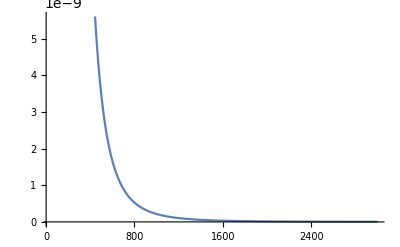

```mathematica
Plot[ (N@(TeV^-4 BRV[{"K0L","eμ"},parametrization->{I3,I3}])),{mU1,40,3000 },Plot]
```

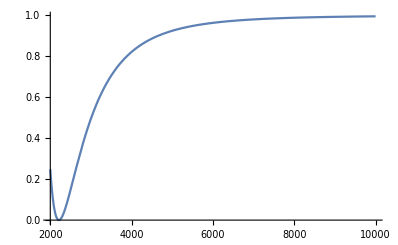

{8.22866×10^-26,{mU1→2212.72}}

8.22866×10^-26-1.03712×10^-15 (mU1-2212.72)+3.26788×10^-6 (mU1-2212.72)^2-7.38431×10^-9 (mU1-2212.72)^3+O[mU1-2212.72]^4

```mathematica
Plot[ ((BRexp[{"K0L","ee"}]-N@(TeV^-4 BRV[{"K0L","eμ"},parametrization->{I3,I3}]))/BRexp[{"K0L","ee"}])^2,{mU1,2000,10000 }]
FindMinimum[ ((BRexp[{"K0L","ee"}]-N@(TeV^-4 BRV[{"K0L","eμ"},parametrization->{I3,I3}]))/BRexp[{"K0L","ee"}])^2,mU1]
Series[ ((BRexp[{"K0L","ee"}]-N@(TeV^-4 BRV[{"K0L","eμ"},parametrization->{I3,I3}]))/BRexp[{"K0L","ee"}])^2,{mU1,First@Values[%⟦2⟧],3}]
```

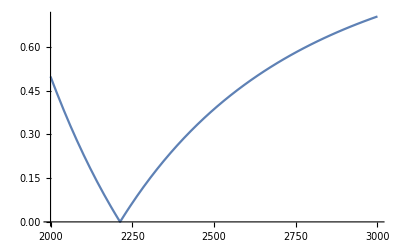

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
Plot[ Abs@((BRexp[{"K0L","ee"}]-N@(TeV^-4 BRV[{"K0L","eμ"},parametrization->{I3,I3}]))/BRexp[{"K0L","ee"}]),{mU1,2000,3000 }]
FindMinimum[ Abs@((BRexp[{"K0L","ee"}]-N@(TeV^-4 BRV[{"K0L","eμ"},parametrization->{I3,I3}]))/BRexp[{"K0L","ee"}]),mU1]
Series[ Abs@((BRexp[{"K0L","ee"}]-N@(TeV^-4 BRV[{"K0L","eμ"},parametrization->{I3,I3}]))/BRexp[{"K0L","ee"}]),{mU1,First@Values[%⟦2⟧],3}]
```

```mathematica
LQmassLimitSingleObs[{I3,I3},{"K0L","eμ"}]
With[{Ul=I3,Ur=I3,process={"K0L","eμ"}},
NMinimize[{(BRexp[process]-N@(TeV^-4 BRV[process,parametrization->{Ul,Ur}]))^2
,1.≤mU1≤5000.}
,mU1]
]
%⟦2⟧/.Rule[a_,b_]->Rule[a,b TeV]
Module[{Ul=I3,Ur=I3,process={"K0L","eμ"},mArbitrary=50*^3,mInit},
mInit=mArbitrary (BRflavio[process,{Ul,Ur,mArbitrary}]/BRexp[process])^(1/4);
NMinimize[{Abs[BRexp[process]-BRflavio[process,{Ul,Ur,mU1GeV}]],1.<mU1GeV<10^8}
,{mU1GeV},
AccuracyGoal->13
,StepMonitor:>Print["Step to mU1 = ",mU1GeV*10^-3," TeV; BRexp=",BRexp[process],"; BRflavio=",BRflavio[process,{Ul,Ur,mU1GeV}]]]
]
```

2602.93 TeV

Calculating β2[K0L,1,2] for given Options...

# Analytical analysis of the minimal model

## Predictions for unitary mixing matrices

### Mixing factors in Smirnov’s parametrization (comparison with his paper)

If calculation of all processes had not been done yet and the results were not loaded, the lenthy (few minutes) FullSimplification will be done during this chapter.

#### Kaon decays

```mathematica
decays[{"K0L"},leptonPairs[form->"numbers",chargeSum->True, sort->"prefferSymmetric"]]
β2viewList[%,smirnovOpts]/.shortCosSin
```

{{K0L,1,1},{K0L,2,2},{K0L,1,2}}

(β^2)_{K0L,1,1}→1/4 (Abs[ⅇ^(ⅈ (ε_L+ε_R)) c_(12 R) c_(13 R) (c_(23 L) s_(12 L)+ⅇ^(ⅈ δ_L) c_(12 L) s_(13 L) s_(23 L))+c_(12 L) c_(13 L) (c_(23 R) s_(12 R)+ⅇ^(-ⅈ δ_R) c_(12 R) s_(13 R) s_(23 R))]^2+Abs[c_(12 R) c_(13 R) (c_(23 L) s_(12 L)+ⅇ^(-ⅈ δ_L) c_(12 L) s_(13 L) s_(23 L))+ⅇ^(ⅈ (ε_L+ε_R)) c_(12 L) c_(13 L) (c_(23 R) s_(12 R)+ⅇ^(ⅈ δ_R) c_(12 R) s_(13 R) s_(23 R))]^2)
(β^2)_{K0L,2,2}→1/4 (Abs[ⅇ^(ⅈ (ε_L+ε_R)) c_(13 R) (c_(12 L) c_(23 L)-ⅇ^(ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L)) s_(12 R)+c_(13 L) s_(12 L) (c_(12 R) c_(23 R)-ⅇ^(-ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R))]^2+Abs[c_(13 R) (c_(12 L) c_(23 L)-ⅇ^(-ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L)) s_(12 R)+ⅇ^(ⅈ (ε_L+ε_R)) c_(13 L) s_(12 L) (c_(12 R) c_(23 R)-ⅇ^(ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R))]^2)
(β^2)_{K0L,1,2}→1/4 (Abs[c_(12 R) c_(13 R) (c_(12 L) c_(23 L)-ⅇ^(-ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L))-ⅇ^(ⅈ (ε_L+ε_R)) c_(13 L) s_(12 L) (c_(23 R) s_(12 R)+ⅇ^(ⅈ δ_R) c_(12 R) s_(13 R) s_(23 R))]^2+Abs[ⅇ^(ⅈ (ε_L+ε_R)) c_(13 R) (c_(23 L) s_(12 L)+ⅇ^(ⅈ δ_L) c_(12 L) s_(13 L) s_(23 L)) s_(12 R)-c_(12 L) c_(13 L) (c_(12 R) c_(23 R)-ⅇ^(-ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R))]^2)

Compare our results with the Smirnov’s formulas:

#### B0 decays

Decays to light leptons:

```mathematica
β2viewList[decays[{"B0"},leptonPairs[form-> "numbers",range->lightLeptons,sort->"prefferSymmetric"]],smirnovOpts]/.shortCosSin
```

(β^2)_{B0,1,1}→1/2 (c_(12 L)^2 c_(13 L)^2 Abs[ⅇ^(ⅈ δ_R) c_(12 R) c_(23 R) s_(13 R)-s_(12 R) s_(23 R)]^2+c_(12 R)^2 c_(13 R)^2 Abs[ⅇ^(ⅈ δ_L) c_(12 L) c_(23 L) s_(13 L)-s_(12 L) s_(23 L)]^2)
(β^2)_{B0,2,2}→1/2 (c_(13 L)^2 s_(12 L)^2 Abs[ⅇ^(ⅈ δ_R) c_(23 R) s_(12 R) s_(13 R)+c_(12 R) s_(23 R)]^2+c_(13 R)^2 s_(12 R)^2 Abs[ⅇ^(ⅈ δ_L) c_(23 L) s_(12 L) s_(13 L)+c_(12 L) s_(23 L)]^2)
(β^2)_{B0,1,2}→1/2 (c_(13 L)^2 s_(12 L)^2 Abs[ⅇ^(ⅈ δ_R) c_(12 R) c_(23 R) s_(13 R)-s_(12 R) s_(23 R)]^2+c_(13 R)^2 s_(12 R)^2 Abs[ⅇ^(ⅈ δ_L) c_(12 L) c_(23 L) s_(13 L)-s_(12 L) s_(23 L)]^2)
(β^2)_{B0,2,1}→1/2 (c_(12 L)^2 c_(13 L)^2 Abs[ⅇ^(ⅈ δ_R) c_(23 R) s_(12 R) s_(13 R)+c_(12 R) s_(23 R)]^2+c_(12 R)^2 c_(13 R)^2 Abs[ⅇ^(ⅈ δ_L) c_(23 L) s_(12 L) s_(13 L)+c_(12 L) s_(23 L)]^2)

Compare with Eqs in the article:

Decays to tauon and light lepton:

```mathematica
β2viewList[decays[{"B0"},{ {3,1},{3,2},{1,3},{2,3} } ],smirnovOpts]/.shortCosSin
```

(β^2)_{B0,3,1}→1/2 (c_(12 L)^2 c_(13 L)^2 Abs[ⅇ^(-ⅈ (ε_R-χ1_R)) c_(13 R) c_(23 R)-(ⅇ^(-ⅈ (ε_L-χ1_L)) m(τ) c_(13 L) c_(23 L))/(2 mbar(B0) RV(B0))]^2+c_(12 R)^2 c_(13 R)^2 Abs[ⅇ^(-ⅈ (ε_L-χ1_L)) c_(13 L) c_(23 L)-(ⅇ^(-ⅈ (ε_R-χ1_R)) m(τ) c_(13 R) c_(23 R))/(2 mbar(B0) RV(B0))]^2)
(β^2)_{B0,3,2}→1/2 (c_(13 L)^2 s_(12 L)^2 Abs[ⅇ^(-ⅈ (ε_R-χ1_R)) c_(13 R) c_(23 R)-(ⅇ^(-ⅈ (ε_L-χ1_L)) m(τ) c_(13 L) c_(23 L))/(2 mbar(B0) RV(B0))]^2+c_(13 R)^2 s_(12 R)^2 Abs[ⅇ^(-ⅈ (ε_L-χ1_L)) c_(13 L) c_(23 L)-(ⅇ^(-ⅈ (ε_R-χ1_R)) m(τ) c_(13 R) c_(23 R))/(2 mbar(B0) RV(B0))]^2)
(β^2)_{B0,1,3}→1/2 (Abs[ⅇ^(ⅈ δ_L) c_(12 L) c_(23 L) s_(13 L)-s_(12 L) s_(23 L)]^2 Abs[ⅇ^(-ⅈ χ2_R) s_(13 R)-(ⅇ^(-ⅈ χ2_L) m(τ) s_(13 L))/(2 mbar(B0) RV(B0))]^2+Abs[ⅇ^(ⅈ δ_R) c_(12 R) c_(23 R) s_(13 R)-s_(12 R) s_(23 R)]^2 Abs[ⅇ^(-ⅈ χ2_L) s_(13 L)-(ⅇ^(-ⅈ χ2_R) m(τ) s_(13 R))/(2 mbar(B0) RV(B0))]^2)
(β^2)_{B0,2,3}→1/2 (Abs[ⅇ^(ⅈ δ_L) c_(23 L) s_(12 L) s_(13 L)+c_(12 L) s_(23 L)]^2 Abs[ⅇ^(-ⅈ χ2_R) s_(13 R)-(ⅇ^(-ⅈ χ2_L) m(τ) s_(13 L))/(2 mbar(B0) RV(B0))]^2+Abs[ⅇ^(ⅈ δ_R) c_(23 R) s_(12 R) s_(13 R)+c_(12 R) s_(23 R)]^2 Abs[ⅇ^(-ⅈ χ2_L) s_(13 L)-(ⅇ^(-ⅈ χ2_R) m(τ) s_(13 R))/(2 mbar(B0) RV(B0))]^2)

This is to be compared with

I think it’s really the same.

#### Bs decays

Decays to light leptons:

```mathematica
decays[{"Bs"},leptonPairs[form-> "numbers",range->lightLeptons,sort->"prefferSymmetric"]]
β2viewList[%,smirnovOpts]/.shortCosSin
```

{{Bs,1,1},{Bs,2,2},{Bs,1,2},{Bs,2,1}}

(β^2)_{Bs,1,1}→1/2 (Abs[c_(23 L) s_(12 L)+ⅇ^(-ⅈ δ_L) c_(12 L) s_(13 L) s_(23 L)]^2 Abs[ⅇ^(ⅈ δ_R) c_(12 R) c_(23 R) s_(13 R)-s_(12 R) s_(23 R)]^2+Abs[ⅇ^(ⅈ δ_L) c_(12 L) c_(23 L) s_(13 L)-s_(12 L) s_(23 L)]^2 Abs[c_(23 R) s_(12 R)+ⅇ^(-ⅈ δ_R) c_(12 R) s_(13 R) s_(23 R)]^2)
(β^2)_{Bs,2,2}→1/2 (Abs[c_(12 L) c_(23 L)-ⅇ^(-ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L)]^2 Abs[ⅇ^(ⅈ δ_R) c_(23 R) s_(12 R) s_(13 R)+c_(12 R) s_(23 R)]^2+Abs[ⅇ^(ⅈ δ_L) c_(23 L) s_(12 L) s_(13 L)+c_(12 L) s_(23 L)]^2 Abs[c_(12 R) c_(23 R)-ⅇ^(-ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R)]^2)
(β^2)_{Bs,1,2}→1/2 (Abs[c_(12 L) c_(23 L)-ⅇ^(-ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L)]^2 Abs[ⅇ^(ⅈ δ_R) c_(12 R) c_(23 R) s_(13 R)-s_(12 R) s_(23 R)]^2+Abs[ⅇ^(ⅈ δ_L) c_(12 L) c_(23 L) s_(13 L)-s_(12 L) s_(23 L)]^2 Abs[c_(12 R) c_(23 R)-ⅇ^(-ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R)]^2)
(β^2)_{Bs,2,1}→1/2 (Abs[c_(23 L) s_(12 L)+ⅇ^(-ⅈ δ_L) c_(12 L) s_(13 L) s_(23 L)]^2 Abs[ⅇ^(ⅈ δ_R) c_(23 R) s_(12 R) s_(13 R)+c_(12 R) s_(23 R)]^2+Abs[ⅇ^(ⅈ δ_L) c_(23 L) s_(12 L) s_(13 L)+c_(12 L) s_(23 L)]^2 Abs[c_(23 R) s_(12 R)+ⅇ^(-ⅈ δ_R) c_(12 R) s_(13 R) s_(23 R)]^2)

```mathematica
-Graphics-
-Graphics-
```

Decays to tauon and light lepton:

```mathematica
decays[{"Bs"},{ {3,1},{3,2},{1,3},{2,3} } ]
β2viewList[%,smirnovOpts]/.shortCosSin
```

{{Bs,3,1},{Bs,3,2},{Bs,1,3},{Bs,2,3}}

(β^2)_{Bs,3,1}→1/2 (Abs[c_(23 L) s_(12 L)+ⅇ^(-ⅈ δ_L) c_(12 L) s_(13 L) s_(23 L)]^2 Abs[ⅇ^(-ⅈ (ε_R-χ1_R)) c_(13 R) c_(23 R)-(ⅇ^(-ⅈ (ε_L-χ1_L)) m(τ) c_(13 L) c_(23 L))/(2 mbar(Bs) RV(Bs))]^2+Abs[c_(23 R) s_(12 R)+ⅇ^(-ⅈ δ_R) c_(12 R) s_(13 R) s_(23 R)]^2 Abs[ⅇ^(-ⅈ (ε_L-χ1_L)) c_(13 L) c_(23 L)-(ⅇ^(-ⅈ (ε_R-χ1_R)) m(τ) c_(13 R) c_(23 R))/(2 mbar(Bs) RV(Bs))]^2)
(β^2)_{Bs,3,2}→1/2 (Abs[c_(12 L) c_(23 L)-ⅇ^(-ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L)]^2 Abs[ⅇ^(-ⅈ (ε_R-χ1_R)) c_(13 R) c_(23 R)-(ⅇ^(-ⅈ (ε_L-χ1_L)) m(τ) c_(13 L) c_(23 L))/(2 mbar(Bs) RV(Bs))]^2+Abs[c_(12 R) c_(23 R)-ⅇ^(-ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R)]^2 Abs[ⅇ^(-ⅈ (ε_L-χ1_L)) c_(13 L) c_(23 L)-(ⅇ^(-ⅈ (ε_R-χ1_R)) m(τ) c_(13 R) c_(23 R))/(2 mbar(Bs) RV(Bs))]^2)
(β^2)_{Bs,1,3}→1/2 (Abs[ⅇ^(ⅈ δ_L) c_(12 L) c_(23 L) s_(13 L)-s_(12 L) s_(23 L)]^2 Abs[ⅇ^(-ⅈ (δ_R+ε_R+χ2_R)) c_(13 R) s_(23 R)-(ⅇ^(-ⅈ (δ_L+ε_L+χ2_L)) m(τ) c_(13 L) s_(23 L))/(2 mbar(Bs) RV(Bs))]^2+Abs[ⅇ^(ⅈ δ_R) c_(12 R) c_(23 R) s_(13 R)-s_(12 R) s_(23 R)]^2 Abs[ⅇ^(-ⅈ (δ_L+ε_L+χ2_L)) c_(13 L) s_(23 L)-(ⅇ^(-ⅈ (δ_R+ε_R+χ2_R)) m(τ) c_(13 R) s_(23 R))/(2 mbar(Bs) RV(Bs))]^2)
(β^2)_{Bs,2,3}→1/2 (Abs[ⅇ^(ⅈ δ_L) c_(23 L) s_(12 L) s_(13 L)+c_(12 L) s_(23 L)]^2 Abs[ⅇ^(-ⅈ (δ_R+ε_R+χ2_R)) c_(13 R) s_(23 R)-(ⅇ^(-ⅈ (δ_L+ε_L+χ2_L)) m(τ) c_(13 L) s_(23 L))/(2 mbar(Bs) RV(Bs))]^2+Abs[ⅇ^(ⅈ δ_R) c_(23 R) s_(12 R) s_(13 R)+c_(12 R) s_(23 R)]^2 Abs[ⅇ^(-ⅈ (δ_L+ε_L+χ2_L)) c_(13 L) s_(23 L)-(ⅇ^(-ⅈ (δ_R+ε_R+χ2_R)) m(τ) c_(13 R) s_(23 R))/(2 mbar(Bs) RV(Bs))]^2)

The Bs-τ-τ vertex:

```mathematica
β2view["Bs",3,3,smirnovOpts]/.shortCosSin
```

(β^2)_{Bs,3,3}→1/2 (Abs[ⅇ^(-ⅈ (ε_L-χ1_L)) c_(13 L) c_(23 L)-(ⅇ^(-ⅈ (ε_R-χ1_R)) m(τ) c_(13 R) c_(23 R))/(2 mbar(Bs) RV(Bs))]^2 Abs[ⅇ^(-ⅈ (δ_R+ε_R+χ2_R)) c_(13 R) s_(23 R)-(ⅇ^(-ⅈ (δ_L+ε_L+χ2_L)) m(τ) c_(13 L) s_(23 L))/(2 mbar(Bs) RV(Bs))]^2+Abs[ⅇ^(-ⅈ (ε_R-χ1_R)) c_(13 R) c_(23 R)-(ⅇ^(-ⅈ (ε_L-χ1_L)) m(τ) c_(13 L) c_(23 L))/(2 mbar(Bs) RV(Bs))]^2 Abs[ⅇ^(-ⅈ (δ_L+ε_L+χ2_L)) c_(13 L) s_(23 L)-(ⅇ^(-ⅈ (δ_R+ε_R+χ2_R)) m(τ) c_(13 R) s_(23 R))/(2 mbar(Bs) RV(Bs))]^2)

I think it is not the same! But it is Smirnov who changed the convention, not me... ☺ I don’t care about Bs→ττ anyway...

## Finding nice parts of parameter space

## Phase alignment - Eqs. (42)

#### The equations

This is supposed to help with the decays involving τ-leptons. I don’t know why is it here at this moment.

```mathematica
-Graphics-
-Graphics-
-Graphics-
```

```mathematica
Eq42={ Subscript[χ1, "L"]-Subscript[ε, "L"]-Subscript[χ1, "R"]+Subscript[ε, "R"]==0, Subscript[χ2, "L"]-Subscript[χ2, "R"]==0, Subscript[δ, "L"]+Subscript[ε, "L"]-Subscript[δ, "R"]-Subscript[ε, "R"]==0};
TableForm@Eq42
```

-ε_L+ε_R+χ1_L-χ1_R==0
χ2_L-χ2_R==0
δ_L-δ_R+ε_L-ε_R==0

#### The solution

It is of course trivial to solve this set of quations, but to choose the best parameters to solve it for is not.
Using the experience from the future of this notebook, I decided for

```mathematica
Eq42sol=First@Solve[Eq42,{Subscript[χ2, "L"],Subscript[χ1, "L"],Subscript[ε, "L"]}];
TableForm@Eq42sol
```

χ2_L→χ2_R
χ1_L→-δ_L+δ_R+χ1_R
ε_L→-δ_L+δ_R+ε_R

#### Implications

As we can see, it simply maximizes the interference within the terms in the chirality-mixing absolute values. This, indeed, is a necessary condition for minimizing the expressions.

```mathematica
Assuming[Eq42,Simplify@
β2viewList[decays[{"B0" ,"Bs"},{ {3,1},{3,2},{1,3},{2,3} } ],smirnovOpts]
]/.shortCosSin
```

(β^2)_{B0,3,1}→1/8 (c_(12 L)^2 c_(13 L)^2 Abs[2 c_(13 R) c_(23 R)-(m(τ) c_(13 L) c_(23 L))/(mbar(B0) RV(B0))]^2+c_(12 R)^2 c_(13 R)^2 Abs[2 c_(13 L) c_(23 L)-(m(τ) c_(13 R) c_(23 R))/(mbar(B0) RV(B0))]^2)
(β^2)_{B0,3,2}→1/8 (c_(13 L)^2 s_(12 L)^2 Abs[2 c_(13 R) c_(23 R)-(m(τ) c_(13 L) c_(23 L))/(mbar(B0) RV(B0))]^2+c_(13 R)^2 s_(12 R)^2 Abs[2 c_(13 L) c_(23 L)-(m(τ) c_(13 R) c_(23 R))/(mbar(B0) RV(B0))]^2)
(β^2)_{B0,1,3}→1/8 (Abs[ⅇ^(ⅈ δ_L) c_(12 L) c_(23 L) s_(13 L)-s_(12 L) s_(23 L)]^2 Abs[(m(τ) s_(13 L))/(mbar(B0) RV(B0))-2 s_(13 R)]^2+Abs[ⅇ^(ⅈ δ_R) c_(12 R) c_(23 R) s_(13 R)-s_(12 R) s_(23 R)]^2 Abs[2 s_(13 L)-(m(τ) s_(13 R))/(mbar(B0) RV(B0))]^2)
(β^2)_{B0,2,3}→1/8 (Abs[ⅇ^(ⅈ δ_L) c_(23 L) s_(12 L) s_(13 L)+c_(12 L) s_(23 L)]^2 Abs[(m(τ) s_(13 L))/(mbar(B0) RV(B0))-2 s_(13 R)]^2+Abs[ⅇ^(ⅈ δ_R) c_(23 R) s_(12 R) s_(13 R)+c_(12 R) s_(23 R)]^2 Abs[2 s_(13 L)-(m(τ) s_(13 R))/(mbar(B0) RV(B0))]^2)
(β^2)_{Bs,3,1}→1/8 (Abs[c_(23 L) s_(12 L)+ⅇ^(-ⅈ δ_L) c_(12 L) s_(13 L) s_(23 L)]^2 Abs[2 c_(13 R) c_(23 R)-(m(τ) c_(13 L) c_(23 L))/(mbar(Bs) RV(Bs))]^2+Abs[c_(23 R) s_(12 R)+ⅇ^(-ⅈ δ_R) c_(12 R) s_(13 R) s_(23 R)]^2 Abs[2 c_(13 L) c_(23 L)-(m(τ) c_(13 R) c_(23 R))/(mbar(Bs) RV(Bs))]^2)
(β^2)_{Bs,3,2}→1/8 (Abs[c_(12 L) c_(23 L)-ⅇ^(-ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L)]^2 Abs[2 c_(13 R) c_(23 R)-(m(τ) c_(13 L) c_(23 L))/(mbar(Bs) RV(Bs))]^2+Abs[c_(12 R) c_(23 R)-ⅇ^(-ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R)]^2 Abs[2 c_(13 L) c_(23 L)-(m(τ) c_(13 R) c_(23 R))/(mbar(Bs) RV(Bs))]^2)
(β^2)_{Bs,1,3}→1/8 (Abs[ⅇ^(ⅈ δ_L) c_(12 L) c_(23 L) s_(13 L)-s_(12 L) s_(23 L)]^2 Abs[(m(τ) c_(13 L) s_(23 L))/(mbar(Bs) RV(Bs))-2 c_(13 R) s_(23 R)]^2+Abs[ⅇ^(ⅈ δ_R) c_(12 R) c_(23 R) s_(13 R)-s_(12 R) s_(23 R)]^2 Abs[2 c_(13 L) s_(23 L)-(m(τ) c_(13 R) s_(23 R))/(mbar(Bs) RV(Bs))]^2)
(β^2)_{Bs,2,3}→1/8 (Abs[ⅇ^(ⅈ δ_L) c_(23 L) s_(12 L) s_(13 L)+c_(12 L) s_(23 L)]^2 Abs[(m(τ) c_(13 L) s_(23 L))/(mbar(Bs) RV(Bs))-2 c_(13 R) s_(23 R)]^2+Abs[ⅇ^(ⅈ δ_R) c_(23 R) s_(12 R) s_(13 R)+c_(12 R) s_(23 R)]^2 Abs[2 c_(13 L) s_(23 L)-(m(τ) c_(13 R) s_(23 R))/(mbar(Bs) RV(Bs))]^2)

## Eliminating the K_L^0→ll’ decays - Eq. (43):

### The Equations (43)

```mathematica
β2K0LllList=Table[β2[Pij,smirnovOpts],{Pij,{{"K0L",1,1},{"K0L",2,2},{"K0L",1,2}}}];
Eq43 = Table[0==β2ll,{β2ll,β2K0LllList}];
Eq43/.shortCosSin//TableForm//TraditionalForm
```

0==1/4 (Abs[ⅇ^(ⅈ (ε_L+ε_R)) c_(12 R) c_(13 R) (c_(23 L) s_(12 L)+ⅇ^(ⅈ δ_L) c_(12 L) s_(13 L) s_(23 L))+c_(12 L) c_(13 L) (c_(23 R) s_(12 R)+ⅇ^(-ⅈ δ_R) c_(12 R) s_(13 R) s_(23 R))]^2+Abs[c_(12 R) c_(13 R) (c_(23 L) s_(12 L)+ⅇ^(-ⅈ δ_L) c_(12 L) s_(13 L) s_(23 L))+ⅇ^(ⅈ (ε_L+ε_R)) c_(12 L) c_(13 L) (c_(23 R) s_(12 R)+ⅇ^(ⅈ δ_R) c_(12 R) s_(13 R) s_(23 R))]^2)
0==1/4 (Abs[ⅇ^(ⅈ (ε_L+ε_R)) c_(13 R) (c_(12 L) c_(23 L)-ⅇ^(ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L)) s_(12 R)+c_(13 L) s_(12 L) (c_(12 R) c_(23 R)-ⅇ^(-ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R))]^2+Abs[c_(13 R) (c_(12 L) c_(23 L)-ⅇ^(-ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L)) s_(12 R)+ⅇ^(ⅈ (ε_L+ε_R)) c_(13 L) s_(12 L) (c_(12 R) c_(23 R)-ⅇ^(ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R))]^2)
0==1/4 (Abs[c_(12 R) c_(13 R) (c_(12 L) c_(23 L)-ⅇ^(-ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L))-ⅇ^(ⅈ (ε_L+ε_R)) c_(13 L) s_(12 L) (c_(23 R) s_(12 R)+ⅇ^(ⅈ δ_R) c_(12 R) s_(13 R) s_(23 R))]^2+Abs[ⅇ^(ⅈ (ε_L+ε_R)) c_(13 R) (c_(23 L) s_(12 L)+ⅇ^(ⅈ δ_L) c_(12 L) s_(13 L) s_(23 L)) s_(12 R)-c_(12 L) c_(13 L) (c_(12 R) c_(23 R)-ⅇ^(-ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R))]^2)

For the 3 elements to be zero, both absolute values in each of the 3 eqns must be zero:

```mathematica
Eq43v2= Reduce[Eq43];
Eq43v2/.shortCosSin
```

Abs[ⅇ^(ⅈ (ε_L+ε_R)) c_(12 R) c_(13 R) (c_(23 L) s_(12 L)+ⅇ^(ⅈ δ_L) c_(12 L) s_(13 L) s_(23 L))+c_(12 L) c_(13 L) (c_(23 R) s_(12 R)+ⅇ^(-ⅈ δ_R) c_(12 R) s_(13 R) s_(23 R))]==0&&Abs[c_(12 R) c_(13 R) (c_(23 L) s_(12 L)+ⅇ^(-ⅈ δ_L) c_(12 L) s_(13 L) s_(23 L))+ⅇ^(ⅈ (ε_L+ε_R)) c_(12 L) c_(13 L) (c_(23 R) s_(12 R)+ⅇ^(ⅈ δ_R) c_(12 R) s_(13 R) s_(23 R))]==0&&Abs[ⅇ^(ⅈ (ε_L+ε_R)) c_(13 R) (c_(12 L) c_(23 L)-ⅇ^(ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L)) s_(12 R)+c_(13 L) s_(12 L) (c_(12 R) c_(23 R)-ⅇ^(-ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R))]==0&&Abs[c_(13 R) (c_(12 L) c_(23 L)-ⅇ^(-ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L)) s_(12 R)+ⅇ^(ⅈ (ε_L+ε_R)) c_(13 L) s_(12 L) (c_(12 R) c_(23 R)-ⅇ^(ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R))]==0&&Abs[c_(12 R) c_(13 R) (c_(12 L) c_(23 L)-ⅇ^(-ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L))-ⅇ^(ⅈ (ε_L+ε_R)) c_(13 L) s_(12 L) (c_(23 R) s_(12 R)+ⅇ^(ⅈ δ_R) c_(12 R) s_(13 R) s_(23 R))]==0&&Abs[ⅇ^(ⅈ (ε_L+ε_R)) c_(13 R) (c_(23 L) s_(12 L)+ⅇ^(ⅈ δ_L) c_(12 L) s_(13 L) s_(23 L)) s_(12 R)-c_(12 L) c_(13 L) (c_(12 R) c_(23 R)-ⅇ^(-ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R))]==0

Within the given parametrization, it is quite hard to find all the solutions of those equations — it is not even clear for which parameters to solve the equations. 
Smirnov gives two sets of solutions, A and B.  I don’t even understand at the moment what is the intercestion of those two sets.

### Smirnov’s solutions (A and B)

```mathematica
Eq44c = Subscript[δ, "L"]+Subscript[ε, "L"]+Subscript[δ, "R"]+Subscript[ε, "R"]==π;
solutionA = {Subscript[θ, 23"L"]->π/2,Subscript[θ, 23"R"]->π/2,Subscript[θ, 13"L"]->Subscript[θ, 13],Subscript[θ, 13"R"]->Subscript[θ, 13],Solve[Eq44c,Subscript[ε, "L"]]⟦1,1⟧}
solutionB={Subscript[θ, 13"L"]->π/2,Subscript[θ, 13"R"]->π/2};
$Assumptions = $Assumptions∪{Subscript[θ, 13]∈Reals}   (* We've introduced a new parameter in Solution A ! *)
```

{θ_(23 L)→π/2,θ_(23 R)→π/2,θ_(13 L)→θ_13,θ_(13 R)→θ_13,ε_L→π-δ_L-δ_R-ε_R}

{δ_L∈ℝ,δ_R∈ℝ,ε_L∈ℝ,ε_R∈ℝ,θ_13∈ℝ,θ_(12 L)∈ℝ,θ_(13 L)∈ℝ,θ_(23 L)∈ℝ,θ_(12 R)∈ℝ,θ_(13 R)∈ℝ,θ_(23 R)∈ℝ,λ_(11 L)∈ℝ,λ_(12 L)∈ℝ,λ_(13 L)∈ℝ,λ_(14 L)∈ℝ,λ_(15 L)∈ℝ,λ_(16 L)∈ℝ,λ_(21 L)∈ℝ,λ_(22 L)∈ℝ,λ_(23 L)∈ℝ,λ_(24 L)∈ℝ,λ_(25 L)∈ℝ,λ_(26 L)∈ℝ,λ_(31 L)∈ℝ,λ_(32 L)∈ℝ,λ_(33 L)∈ℝ,λ_(34 L)∈ℝ,λ_(35 L)∈ℝ,λ_(36 L)∈ℝ,λ_(41 L)∈ℝ,λ_(42 L)∈ℝ,λ_(43 L)∈ℝ,λ_(44 L)∈ℝ,λ_(45 L)∈ℝ,λ_(46 L)∈ℝ,λ_(51 L)∈ℝ,λ_(52 L)∈ℝ,λ_(53 L)∈ℝ,λ_(54 L)∈ℝ,λ_(55 L)∈ℝ,λ_(56 L)∈ℝ,λ_(61 L)∈ℝ,λ_(62 L)∈ℝ,λ_(63 L)∈ℝ,λ_(64 L)∈ℝ,λ_(65 L)∈ℝ,λ_(66 L)∈ℝ,λ_(11 R)∈ℝ,λ_(12 R)∈ℝ,λ_(13 R)∈ℝ,λ_(14 R)∈ℝ,λ_(15 R)∈ℝ,λ_(16 R)∈ℝ,λ_(21 R)∈ℝ,λ_(22 R)∈ℝ,λ_(23 R)∈ℝ,λ_(24 R)∈ℝ,λ_(25 R)∈ℝ,λ_(26 R)∈ℝ,λ_(31 R)∈ℝ,λ_(32 R)∈ℝ,λ_(33 R)∈ℝ,λ_(34 R)∈ℝ,λ_(35 R)∈ℝ,λ_(36 R)∈ℝ,λ_(41 R)∈ℝ,λ_(42 R)∈ℝ,λ_(43 R)∈ℝ,λ_(44 R)∈ℝ,λ_(45 R)∈ℝ,λ_(46 R)∈ℝ,λ_(51 R)∈ℝ,λ_(52 R)∈ℝ,λ_(53 R)∈ℝ,λ_(54 R)∈ℝ,λ_(55 R)∈ℝ,λ_(56 R)∈ℝ,λ_(61 R)∈ℝ,λ_(62 R)∈ℝ,λ_(63 R)∈ℝ,λ_(64 R)∈ℝ,λ_(65 R)∈ℝ,λ_(66 R)∈ℝ,φ0_L∈ℝ,φ0_R∈ℝ,φ1_L∈ℝ,φ1_R∈ℝ,χ1_L∈ℝ,χ1_R∈ℝ,χ2_L∈ℝ,χ2_R∈ℝ}

Check that both prescriptions are really valid solutions:

```mathematica
TableForm[β2K0LllList/. {solutionA,solutionB}//FullSimplify,
TableHeadings->{{"solutionA","solutionB"}, {"β_(K0L, 11)","β_(K0L, 22)","β_(K0L, 12)"}}]
```

| β_(K0L, 11) | β_(K0L, 22) | β_(K0L, 12)
solutionA | 0 | 0 | 0
solutionB | 0 | 0 | 0

Indeed, it works!

What does it do with the mixing matrices?

### Inspecting Solution B (is easier)

```mathematica
solutionB
```

{θ_(13 L)→π/2,θ_(13 R)→π/2}

```mathematica
showULUR[solutionB]//FullSimplify
(* To find out WTF is  showULUR, type "?showULUR"<>. It is simply another shorthand, essentially MatrixForm/@{UL,UR}/.solutionB *)
```

(0 | 0 | ⅇ^(ⅈ χ2_L)
-ⅇ^(ⅈ (ε_L+φ0_L+φ1_L)) (c_(23 L) s_(12 L)+ⅇ^(ⅈ δ_L) c_(12 L) s_(23 L)) | ⅇ^(ⅈ (ε_L+2 φ0_L-φ1_L-χ1_L)) (c_(12 L) c_(23 L)-ⅇ^(ⅈ δ_L) s_(12 L) s_(23 L)) | 0
ⅇ^(-ⅈ (δ_L+ε_L-φ0_L-φ1_L-χ1_L+χ2_L)) (-ⅇ^(ⅈ δ_L) c_(12 L) c_(23 L)+s_(12 L) s_(23 L)) | ⅇ^(-ⅈ (δ_L+ε_L-2 φ0_L+φ1_L+χ2_L)) (-ⅇ^(ⅈ δ_L) c_(23 L) s_(12 L)-c_(12 L) s_(23 L)) | 0)
(0 | 0 | ⅇ^(ⅈ χ2_R)
-ⅇ^(ⅈ (ε_R+φ0_R+φ1_R)) (c_(23 R) s_(12 R)+ⅇ^(ⅈ δ_R) c_(12 R) s_(23 R)) | ⅇ^(ⅈ (ε_R+2 φ0_R-φ1_R-χ1_R)) (c_(12 R) c_(23 R)-ⅇ^(ⅈ δ_R) s_(12 R) s_(23 R)) | 0
ⅇ^(-ⅈ (δ_R+ε_R-φ0_R-φ1_R-χ1_R+χ2_R)) (-ⅇ^(ⅈ δ_R) c_(12 R) c_(23 R)+s_(12 R) s_(23 R)) | ⅇ^(-ⅈ (δ_R+ε_R-2 φ0_R+φ1_R+χ2_R)) (-ⅇ^(ⅈ δ_R) c_(23 R) s_(12 R)-c_(12 R) s_(23 R)) | 0)

```mathematica
?showULUR
```

The solution B does the job by eliminating the interaction od d-quark with both electrons and muons. Then, of course, K^0 cannot decay purely leptonically at the tree level.

Note that in the absence of phases, we’d have only one DOF for each matrix even though we have fixed just one. Thus,  3-1=1. ☺

```mathematica
showULUR[solutionB,Table[ϕ->0,{ϕ,phases}]]
```

(0 | 0 | 1
-Sin[θ_(12 L)+θ_(23 L)] | Cos[θ_(12 L)+θ_(23 L)] | 0
-Cos[θ_(12 L)+θ_(23 L)] | -Sin[θ_(12 L)+θ_(23 L)] | 0)
(0 | 0 | 1
-Sin[θ_(12 R)+θ_(23 R)] | Cos[θ_(12 R)+θ_(23 R)] | 0
-Cos[θ_(12 R)+θ_(23 R)] | -Sin[θ_(12 R)+θ_(23 R)] | 0)

### Inspecting Solution A

```mathematica
solutionA
```

{θ_(23 L)→π/2,θ_(23 R)→π/2,θ_(13 L)→θ_13,θ_(13 R)→θ_13,ε_L→π-δ_L-δ_R-ε_R}

This class of solutions fixes much more parameters than that solution B. 
Therefore, one might say that it defines much smaller part of the parameter space (even tough it has no measure).
On the other hand, as we have seen, SolutionB in the absence of thases also leaves less angles than solutionA.

```mathematica
showULUR[solutionA]
```

(ⅇ^(ⅈ (φ0_L+φ1_L)) c_13 c_(12 L) | ⅇ^(ⅈ (2 φ0_L-φ1_L-χ1_L)) c_13 s_(12 L) | ⅇ^(ⅈ χ2_L) s_13
ⅇ^(-ⅈ (δ_R+ε_R-φ0_L-φ1_L)) c_(12 L) s_13 | ⅇ^(-ⅈ (δ_R+ε_R-2 φ0_L+φ1_L+χ1_L)) s_13 s_(12 L) | -ⅇ^(-ⅈ (δ_R+ε_R-χ2_L)) c_13
-ⅇ^(ⅈ (δ_R+ε_R+φ0_L+φ1_L+χ1_L-χ2_L)) s_(12 L) | ⅇ^(ⅈ (δ_R+ε_R+2 φ0_L-φ1_L-χ2_L)) c_(12 L) | 0)
(ⅇ^(ⅈ (φ0_R+φ1_R)) c_13 c_(12 R) | ⅇ^(ⅈ (2 φ0_R-φ1_R-χ1_R)) c_13 s_(12 R) | ⅇ^(ⅈ χ2_R) s_13
-ⅇ^(ⅈ (δ_R+ε_R+φ0_R+φ1_R)) c_(12 R) s_13 | -ⅇ^(ⅈ (δ_R+ε_R+2 φ0_R-φ1_R-χ1_R)) s_13 s_(12 R) | ⅇ^(ⅈ (δ_R+ε_R+χ2_R)) c_13
ⅇ^(-ⅈ (δ_R+ε_R-φ0_R-φ1_R-χ1_R+χ2_R)) s_(12 R) | -ⅇ^(-ⅈ (δ_R+ε_R-2 φ0_R+φ1_R+χ2_R)) c_(12 R) | 0)

This is a pretty tricky solution: it doesn’t  send any of the interaction vertices to zero, 
but ensures 100% negative interference in parts of Eqs43:

∀i,j∈{1,2}    UL⟦2,i⟧ UR⟦1,j⟧*+UL⟦1,i⟧ UR⟦2,j⟧ ==0  .

#### It is the interferences!

To remind, these expressions inside the Absolute values (and their two parts) read :

```mathematica
expressions=Table[{Eq43v2⟦i,1⟧,Eq43v2⟦i,1⟧⟦1,1⟧,Eq43v2⟦i,1⟧⟦1,2⟧},{i,1,6}];
expressions/.shortCosSin//TableForm//TraditionalForm
```

Abs[c_(12 R) c_(13 R) ⅇ^(ⅈ (ε_L+ε_R)) (c_(23 L) s_(12 L)+c_(12 L) ⅇ^(ⅈ δ_L) s_(13 L) s_(23 L))+c_(12 L) c_(13 L) (c_(23 R) s_(12 R)+c_(12 R) ⅇ^(-ⅈ δ_R) s_(13 R) s_(23 R))] | c_(12 R) c_(13 R) ⅇ^(ⅈ (ε_L+ε_R)) (c_(23 L) s_(12 L)+c_(12 L) ⅇ^(ⅈ δ_L) s_(13 L) s_(23 L)) | c_(12 L) c_(13 L) (c_(23 R) s_(12 R)+c_(12 R) ⅇ^(-ⅈ δ_R) s_(13 R) s_(23 R))
Abs[c_(12 L) c_(13 L) ⅇ^(ⅈ (ε_L+ε_R)) (c_(23 R) s_(12 R)+c_(12 R) ⅇ^(ⅈ δ_R) s_(13 R) s_(23 R))+c_(12 R) c_(13 R) (c_(23 L) s_(12 L)+c_(12 L) ⅇ^(-ⅈ δ_L) s_(13 L) s_(23 L))] | c_(12 R) c_(13 R) (c_(23 L) s_(12 L)+c_(12 L) ⅇ^(-ⅈ δ_L) s_(13 L) s_(23 L)) | c_(12 L) c_(13 L) ⅇ^(ⅈ (ε_L+ε_R)) (c_(23 R) s_(12 R)+c_(12 R) ⅇ^(ⅈ δ_R) s_(13 R) s_(23 R))
Abs[c_(13 R) s_(12 R) ⅇ^(ⅈ (ε_L+ε_R)) (c_(12 L) c_(23 L)-ⅇ^(ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L))+c_(13 L) s_(12 L) (c_(12 R) c_(23 R)-ⅇ^(-ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R))] | c_(13 R) s_(12 R) ⅇ^(ⅈ (ε_L+ε_R)) (c_(12 L) c_(23 L)-ⅇ^(ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L)) | c_(13 L) s_(12 L) (c_(12 R) c_(23 R)-ⅇ^(-ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R))
Abs[c_(13 L) s_(12 L) ⅇ^(ⅈ (ε_L+ε_R)) (c_(12 R) c_(23 R)-ⅇ^(ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R))+c_(13 R) s_(12 R) (c_(12 L) c_(23 L)-ⅇ^(-ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L))] | c_(13 R) s_(12 R) (c_(12 L) c_(23 L)-ⅇ^(-ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L)) | c_(13 L) s_(12 L) ⅇ^(ⅈ (ε_L+ε_R)) (c_(12 R) c_(23 R)-ⅇ^(ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R))
Abs[c_(12 R) c_(13 R) (c_(12 L) c_(23 L)-ⅇ^(-ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L))-c_(13 L) s_(12 L) ⅇ^(ⅈ (ε_L+ε_R)) (c_(23 R) s_(12 R)+c_(12 R) ⅇ^(ⅈ δ_R) s_(13 R) s_(23 R))] | c_(12 R) c_(13 R) (c_(12 L) c_(23 L)-ⅇ^(-ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L)) | c_(13 L) s_(12 L) (-ⅇ^(ⅈ (ε_L+ε_R))) (c_(23 R) s_(12 R)+c_(12 R) ⅇ^(ⅈ δ_R) s_(13 R) s_(23 R))
Abs[c_(13 R) s_(12 R) ⅇ^(ⅈ (ε_L+ε_R)) (c_(23 L) s_(12 L)+c_(12 L) ⅇ^(ⅈ δ_L) s_(13 L) s_(23 L))-c_(12 L) c_(13 L) (c_(12 R) c_(23 R)-ⅇ^(-ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R))] | c_(13 R) s_(12 R) ⅇ^(ⅈ (ε_L+ε_R)) (c_(23 L) s_(12 L)+c_(12 L) ⅇ^(ⅈ δ_L) s_(13 L) s_(23 L)) | -c_(12 L) c_(13 L) (c_(12 R) c_(23 R)-ⅇ^(-ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R))

And what the solutionA makes with them: the sum of tho two terms vasishes while the indivual terms don’t.

```mathematica
Simplify[expressions/.solutionA]/.shortCosSin//TableForm//TraditionalForm
```

0 | -1/2 c_(12 L) c_(12 R) sin(2 θ_13) ⅇ^(-ⅈ δ_R) | c_13 s_13 c_(12 L) c_(12 R) ⅇ^(-ⅈ δ_R)
0 | c_13 s_13 c_(12 L) c_(12 R) ⅇ^(-ⅈ δ_L) | -1/2 c_(12 L) c_(12 R) sin(2 θ_13) ⅇ^(-ⅈ δ_L)
0 | 1/2 sin(2 θ_13) s_(12 L) ⅇ^(-ⅈ δ_R) s_(12 R) | -1/2 sin(2 θ_13) s_(12 L) ⅇ^(-ⅈ δ_R) s_(12 R)
0 | -1/2 sin(2 θ_13) ⅇ^(-ⅈ δ_L) s_(12 L) s_(12 R) | 1/2 sin(2 θ_13) ⅇ^(-ⅈ δ_L) s_(12 L) s_(12 R)
0 | -1/2 c_(12 R) sin(2 θ_13) ⅇ^(-ⅈ δ_L) s_(12 L) | 1/2 c_(12 R) sin(2 θ_13) ⅇ^(-ⅈ δ_L) s_(12 L)
0 | -1/2 c_(12 L) sin(2 θ_13) ⅇ^(-ⅈ δ_R) s_(12 R) | c_13 s_13 c_(12 L) ⅇ^(-ⅈ δ_R) s_(12 R)

### Interplay between (42) and (SolutionA of 43)

The two conditions  -- (42) from the previous chapter  and  SolutionA.c of (43) -- talk about the same parameters ε_(L,R) and δ_(L,R) , so we must take care of that!

```mathematica
TableForm[{Eq42,Eq44c}]
```

-ε_L+ε_R+χ1_L-χ1_R==0 | χ2_L-χ2_R==0 | δ_L-δ_R+ε_L-ε_R==0
δ_L+δ_R+ε_L+ε_R==π |  |

Not for all choices of 4 phases can this set of equations be solved!
And one needs to Solve those equations simultaneously!

```mathematica
solutionAand42 = solutionA⟦1;;4⟧~Join~
Solve[Append[Eq42,Eq44c],{Subscript[ε, "L"],Subscript[ε, "R"],Subscript[χ2, "L"],Subscript[χ1, "L"]}] ⟦1⟧
```

{θ_(23 L)→π/2,θ_(23 R)→π/2,θ_(13 L)→θ_13,θ_(13 R)→θ_13,ε_L→π/2-δ_L,ε_R→1/2 (π-2 δ_R),χ2_L→χ2_R,χ1_L→-δ_L+δ_R+χ1_R}

#### machrovinka

By the way, one could also let WM decide itself to choose a set of good variables, e.g.:

```mathematica
Reduce[Append[Eq42,Eq44c]]
%/.{{And->Sequence,Equal->Rule}}
```

χ2_L==χ2_R&&ε_L==ε_R+χ1_L-χ1_R&&δ_R==π/2-ε_R&&δ_L==π/2-ε_R-χ1_L+χ1_R

{χ2_L→χ2_R,ε_L→ε_R+χ1_L-χ1_R,δ_R→π/2-ε_R,δ_L→π/2-ε_R-χ1_L+χ1_R}

But the result may be rather unstable — I don’t know what criteria oit had used for determining the dependent variables.

### Hedvika’s solution

#### Irrelevant stuff (implemented by Matěj)

```mathematica
Eq43v2/.shortCosSin
```

Abs[ⅇ^(ⅈ (ε_L+ε_R)) c_(12 R) c_(13 R) (c_(23 L) s_(12 L)+ⅇ^(ⅈ δ_L) c_(12 L) s_(13 L) s_(23 L))+c_(12 L) c_(13 L) (c_(23 R) s_(12 R)+ⅇ^(-ⅈ δ_R) c_(12 R) s_(13 R) s_(23 R))]==0&&Abs[c_(12 R) c_(13 R) (c_(23 L) s_(12 L)+ⅇ^(-ⅈ δ_L) c_(12 L) s_(13 L) s_(23 L))+ⅇ^(ⅈ (ε_L+ε_R)) c_(12 L) c_(13 L) (c_(23 R) s_(12 R)+ⅇ^(ⅈ δ_R) c_(12 R) s_(13 R) s_(23 R))]==0&&Abs[ⅇ^(ⅈ (ε_L+ε_R)) c_(13 R) (c_(12 L) c_(23 L)-ⅇ^(ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L)) s_(12 R)+c_(13 L) s_(12 L) (c_(12 R) c_(23 R)-ⅇ^(-ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R))]==0&&Abs[c_(13 R) (c_(12 L) c_(23 L)-ⅇ^(-ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L)) s_(12 R)+ⅇ^(ⅈ (ε_L+ε_R)) c_(13 L) s_(12 L) (c_(12 R) c_(23 R)-ⅇ^(ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R))]==0&&Abs[c_(12 R) c_(13 R) (c_(12 L) c_(23 L)-ⅇ^(-ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L))-ⅇ^(ⅈ (ε_L+ε_R)) c_(13 L) s_(12 L) (c_(23 R) s_(12 R)+ⅇ^(ⅈ δ_R) c_(12 R) s_(13 R) s_(23 R))]==0&&Abs[ⅇ^(ⅈ (ε_L+ε_R)) c_(13 R) (c_(23 L) s_(12 L)+ⅇ^(ⅈ δ_L) c_(12 L) s_(13 L) s_(23 L)) s_(12 R)-c_(12 L) c_(13 L) (c_(12 R) c_(23 R)-ⅇ^(-ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R))]==0

The following corresponds to {Eq1 , ..., Eq6 }

```mathematica
Eq43LHS=Eq43v2/.{LHS_==0->LHS,And->List}/.Abs->Identity;
TableForm@%/.shortCosSin
```

ⅇ^(ⅈ (ε_L+ε_R)) c_(12 R) c_(13 R) (c_(23 L) s_(12 L)+ⅇ^(ⅈ δ_L) c_(12 L) s_(13 L) s_(23 L))+c_(12 L) c_(13 L) (c_(23 R) s_(12 R)+ⅇ^(-ⅈ δ_R) c_(12 R) s_(13 R) s_(23 R))
c_(12 R) c_(13 R) (c_(23 L) s_(12 L)+ⅇ^(-ⅈ δ_L) c_(12 L) s_(13 L) s_(23 L))+ⅇ^(ⅈ (ε_L+ε_R)) c_(12 L) c_(13 L) (c_(23 R) s_(12 R)+ⅇ^(ⅈ δ_R) c_(12 R) s_(13 R) s_(23 R))
ⅇ^(ⅈ (ε_L+ε_R)) c_(13 R) (c_(12 L) c_(23 L)-ⅇ^(ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L)) s_(12 R)+c_(13 L) s_(12 L) (c_(12 R) c_(23 R)-ⅇ^(-ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R))
c_(13 R) (c_(12 L) c_(23 L)-ⅇ^(-ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L)) s_(12 R)+ⅇ^(ⅈ (ε_L+ε_R)) c_(13 L) s_(12 L) (c_(12 R) c_(23 R)-ⅇ^(ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R))
c_(12 R) c_(13 R) (c_(12 L) c_(23 L)-ⅇ^(-ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L))-ⅇ^(ⅈ (ε_L+ε_R)) c_(13 L) s_(12 L) (c_(23 R) s_(12 R)+ⅇ^(ⅈ δ_R) c_(12 R) s_(13 R) s_(23 R))
ⅇ^(ⅈ (ε_L+ε_R)) c_(13 R) (c_(23 L) s_(12 L)+ⅇ^(ⅈ δ_L) c_(12 L) s_(13 L) s_(23 L)) s_(12 R)-c_(12 L) c_(13 L) (c_(12 R) c_(23 R)-ⅇ^(-ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R))

This way I get {XEq1  , ..., XEq6}:

```mathematica
Eq43LHSv2=ExpToTrig[ Eq43LHS];
%/.shortCosSin//TableForm
```

(Cos[ε_L+ε_R]+ⅈ Sin[ε_L+ε_R]) c_(12 R) c_(13 R) (c_(23 L) s_(12 L)+Cos[δ_L] c_(12 L) s_(13 L) s_(23 L)+ⅈ Sin[δ_L] c_(12 L) s_(13 L) s_(23 L))+c_(12 L) c_(13 L) c_(23 R) s_(12 R)+Cos[δ_R] c_(12 L) c_(13 L) c_(12 R) s_(13 R) s_(23 R)-ⅈ Sin[δ_R] c_(12 L) c_(13 L) c_(12 R) s_(13 R) s_(23 R)
c_(23 L) c_(12 R) c_(13 R) s_(12 L)+Cos[δ_L] c_(12 L) c_(12 R) c_(13 R) s_(13 L) s_(23 L)-ⅈ Sin[δ_L] c_(12 L) c_(12 R) c_(13 R) s_(13 L) s_(23 L)+(Cos[ε_L+ε_R]+ⅈ Sin[ε_L+ε_R]) c_(12 L) c_(13 L) (c_(23 R) s_(12 R)+Cos[δ_R] c_(12 R) s_(13 R) s_(23 R)+ⅈ Sin[δ_R] c_(12 R) s_(13 R) s_(23 R))
c_(13 L) c_(12 R) c_(23 R) s_(12 L)+(Cos[ε_L+ε_R]+ⅈ Sin[ε_L+ε_R]) c_(13 R) (c_(12 L) c_(23 L)-Cos[δ_L] s_(12 L) s_(13 L) s_(23 L)-ⅈ Sin[δ_L] s_(12 L) s_(13 L) s_(23 L)) s_(12 R)-Cos[δ_R] c_(13 L) s_(12 L) s_(12 R) s_(13 R) s_(23 R)+ⅈ Sin[δ_R] c_(13 L) s_(12 L) s_(12 R) s_(13 R) s_(23 R)
c_(12 L) c_(23 L) c_(13 R) s_(12 R)-Cos[δ_L] c_(13 R) s_(12 L) s_(13 L) s_(23 L) s_(12 R)+ⅈ Sin[δ_L] c_(13 R) s_(12 L) s_(13 L) s_(23 L) s_(12 R)+(Cos[ε_L+ε_R]+ⅈ Sin[ε_L+ε_R]) c_(13 L) s_(12 L) (c_(12 R) c_(23 R)-Cos[δ_R] s_(12 R) s_(13 R) s_(23 R)-ⅈ Sin[δ_R] s_(12 R) s_(13 R) s_(23 R))
c_(12 L) c_(23 L) c_(12 R) c_(13 R)-Cos[δ_L] c_(12 R) c_(13 R) s_(12 L) s_(13 L) s_(23 L)+ⅈ Sin[δ_L] c_(12 R) c_(13 R) s_(12 L) s_(13 L) s_(23 L)-(Cos[ε_L+ε_R]+ⅈ Sin[ε_L+ε_R]) c_(13 L) s_(12 L) (c_(23 R) s_(12 R)+Cos[δ_R] c_(12 R) s_(13 R) s_(23 R)+ⅈ Sin[δ_R] c_(12 R) s_(13 R) s_(23 R))
-c_(12 L) c_(13 L) c_(12 R) c_(23 R)+(Cos[ε_L+ε_R]+ⅈ Sin[ε_L+ε_R]) c_(13 R) (c_(23 L) s_(12 L)+Cos[δ_L] c_(12 L) s_(13 L) s_(23 L)+ⅈ Sin[δ_L] c_(12 L) s_(13 L) s_(23 L)) s_(12 R)+Cos[δ_R] c_(12 L) c_(13 L) s_(12 R) s_(13 R) s_(23 R)-ⅈ Sin[δ_R] c_(12 L) c_(13 L) s_(12 R) s_(13 R) s_(23 R)

Real and Imaginary parts

Now we need to take Real an Imaginary parts of these formulas. Unfortunately, the WM functions do not work, even though we have all the assumptions:

```mathematica
$Assumptions
Eq43LHSv2⟦2⟧/.shortCosSin
FullSimplify@Re@Eq43LHSv2⟦2⟧/.shortCosSin
```

{δ_L∈ℝ,δ_R∈ℝ,ε_L∈ℝ,ε_R∈ℝ,θ_13∈ℝ,θ_(12 L)∈ℝ,θ_(13 L)∈ℝ,θ_(23 L)∈ℝ,θ_(12 R)∈ℝ,θ_(13 R)∈ℝ,θ_(23 R)∈ℝ,φ0_L∈ℝ,φ0_R∈ℝ,φ1_L∈ℝ,φ1_R∈ℝ,χ1_L∈ℝ,χ1_R∈ℝ,χ2_L∈ℝ,χ2_R∈ℝ}

c_(23 L) c_(12 R) c_(13 R) s_(12 L)+Cos[δ_L] c_(12 L) c_(12 R) c_(13 R) s_(13 L) s_(23 L)-ⅈ Sin[δ_L] c_(12 L) c_(12 R) c_(13 R) s_(13 L) s_(23 L)+(Cos[ε_L+ε_R]+ⅈ Sin[ε_L+ε_R]) c_(12 L) c_(13 L) (c_(23 R) s_(12 R)+Cos[δ_R] c_(12 R) s_(13 R) s_(23 R)+ⅈ Sin[δ_R] c_(12 R) s_(13 R) s_(23 R))

Re[ⅇ^(ⅈ (ε_L+ε_R)) c_(12 L) c_(13 L) (c_(23 R) s_(12 R)+ⅇ^(ⅈ δ_R) c_(12 R) s_(13 R) s_(23 R))]+c_(12 R) c_(13 R) (c_(23 L) s_(12 L)+Cos[δ_L] c_(12 L) s_(13 L) s_(23 L))

So I will define my own re and im functions. They use the standard formulas using complex-conjugation and then help the kernel distribute the c-conjugation.

```mathematica
re[X_]:=Simplify[(X+X*)/2//.{Conjugate@t_Times:>Conjugate/@t,Conjugate@p_Plus:>Conjugate/@p}]
im[X_]:=Simplify[(X-X*)/(2ⅈ)//.{Conjugate@t_Times:>Conjugate/@t,Conjugate@p_Plus:>Conjugate/@p}]
```

I guess I should take real and imaginary parts of the LHS of Eqns43:

```mathematica
reEq43LHS=re/@Eq43LHSv2;
imEq43LHS=im/@Eq43LHSv2;
TableForm/@{reEq43LHS,imEq43LHS}/.shortCosSin
```

{Cos[ε_L+ε_R] c_(12 R) c_(13 R) (c_(23 L) s_(12 L)+Cos[δ_L] c_(12 L) s_(13 L) s_(23 L))+c_(12 L) (c_(13 L) c_(23 R) s_(12 R)+c_(12 R) (-Sin[δ_L] Sin[ε_L+ε_R] c_(13 R) s_(13 L) s_(23 L)+Cos[δ_R] c_(13 L) s_(13 R) s_(23 R)))
c_(23 L) c_(12 R) c_(13 R) s_(12 L)+c_(12 L) (Cos[δ_L] c_(12 R) c_(13 R) s_(13 L) s_(23 L)+c_(13 L) (-Sin[δ_R] Sin[ε_L+ε_R] c_(12 R) s_(13 R) s_(23 R)+Cos[ε_L+ε_R] (c_(23 R) s_(12 R)+Cos[δ_R] c_(12 R) s_(13 R) s_(23 R))))
c_(13 R) (Sin[δ_L] Sin[ε_L+ε_R] s_(12 L) s_(13 L) s_(23 L)+Cos[ε_L+ε_R] (c_(12 L) c_(23 L)-Cos[δ_L] s_(12 L) s_(13 L) s_(23 L))) s_(12 R)+c_(13 L) s_(12 L) (c_(12 R) c_(23 R)-Cos[δ_R] s_(12 R) s_(13 R) s_(23 R))
Cos[ε_L+ε_R] c_(13 L) s_(12 L) (c_(12 R) c_(23 R)-Cos[δ_R] s_(12 R) s_(13 R) s_(23 R))+s_(12 R) (c_(12 L) c_(23 L) c_(13 R)+s_(12 L) (-Cos[δ_L] c_(13 R) s_(13 L) s_(23 L)+Sin[δ_R] Sin[ε_L+ε_R] c_(13 L) s_(13 R) s_(23 R)))
c_(12 L) c_(23 L) c_(12 R) c_(13 R)-s_(12 L) (Cos[δ_L] c_(12 R) c_(13 R) s_(13 L) s_(23 L)+c_(13 L) (-Sin[δ_R] Sin[ε_L+ε_R] c_(12 R) s_(13 R) s_(23 R)+Cos[ε_L+ε_R] (c_(23 R) s_(12 R)+Cos[δ_R] c_(12 R) s_(13 R) s_(23 R))))
Cos[ε_L+ε_R] c_(23 L) c_(13 R) s_(12 L) s_(12 R)+c_(12 L) (Cos[δ_L+ε_L+ε_R] c_(13 R) s_(13 L) s_(23 L) s_(12 R)+c_(13 L) (-c_(12 R) c_(23 R)+Cos[δ_R] s_(12 R) s_(13 R) s_(23 R))),c_(12 R) (Sin[ε_L+ε_R] c_(23 L) c_(13 R) s_(12 L)+c_(12 L) (Cos[ε_L+ε_R] Sin[δ_L] c_(13 R) s_(13 L) s_(23 L)+Cos[δ_L] Sin[ε_L+ε_R] c_(13 R) s_(13 L) s_(23 L)-Sin[δ_R] c_(13 L) s_(13 R) s_(23 R)))
c_(12 L) (Sin[ε_L+ε_R] c_(13 L) c_(23 R) s_(12 R)+c_(12 R) (-Sin[δ_L] c_(13 R) s_(13 L) s_(23 L)+Sin[δ_R+ε_L+ε_R] c_(13 L) s_(13 R) s_(23 R)))
s_(12 R) (Sin[ε_L+ε_R] c_(12 L) c_(23 L) c_(13 R)-s_(12 L) (Cos[ε_L+ε_R] Sin[δ_L] c_(13 R) s_(13 L) s_(23 L)+Cos[δ_L] Sin[ε_L+ε_R] c_(13 R) s_(13 L) s_(23 L)-Sin[δ_R] c_(13 L) s_(13 R) s_(23 R)))
s_(12 L) (Sin[δ_L] c_(13 R) s_(13 L) s_(23 L) s_(12 R)+c_(13 L) (Sin[ε_L+ε_R] c_(12 R) c_(23 R)-Sin[δ_R+ε_L+ε_R] s_(12 R) s_(13 R) s_(23 R)))
s_(12 L) (-Sin[ε_L+ε_R] c_(13 L) c_(23 R) s_(12 R)+c_(12 R) (Sin[δ_L] c_(13 R) s_(13 L) s_(23 L)-Sin[δ_R+ε_L+ε_R] c_(13 L) s_(13 R) s_(23 R)))
s_(12 R) (Sin[ε_L+ε_R] c_(23 L) c_(13 R) s_(12 L)+c_(12 L) (Cos[ε_L+ε_R] Sin[δ_L] c_(13 R) s_(13 L) s_(23 L)+Cos[δ_L] Sin[ε_L+ε_R] c_(13 R) s_(13 L) s_(23 L)-Sin[δ_R] c_(13 L) s_(13 R) s_(23 R)))}

Where those Eqns come from???

```mathematica
EqX=Cos[Subscript[θ, 23 "L"]] Cos[Subscript[θ, 13 "R"]] Sin[Subscript[ε, "L"]+Subscript[ε, "R"]]==0;
EqY=-Cos[Subscript[θ, 13 "R"]] Sin[Subscript[δ, "L"]+Subscript[ε, "L"]+Subscript[ε, "R"]] Sin[Subscript[θ, 13 "L"]] Sin[Subscript[θ, 23 "L"]]+Cos[Subscript[θ, 13 "L"]] Sin[Subscript[δ, "R"]] Sin[Subscript[θ, 13 "R"]] Sin[Subscript[θ, 23 "R"]]==0;
EqU= Cos[Subscript[θ, 13 "L"]] Cos[Subscript[θ, 23 "R"]] Sin[Subscript[ε, "L"]+Subscript[ε, "R"]]==0;
EqV=-Cos[Subscript[θ, 13 "R"]] Sin[Subscript[δ, "L"]] Sin[Subscript[θ, 13 "L"]] Sin[Subscript[θ, 23 "L"]]+Cos[Subscript[θ, 13 "L"]] Sin[Subscript[δ, "R"]+Subscript[ε, "L"]+Subscript[ε, "R"]] Sin[Subscript[θ, 13 "R"]] Sin[Subscript[θ, 23 "R"]]==0;
```

Now what Hedvika calls {Eq1A, …, Eq6A}:

```mathematica
Eq43lhsA=FullSimplify[Eq43LHS/.{Subscript[ε, "L"]->-Subscript[ε, "R"]}];
%/.shortCosSin//TableForm
```

c_(12 R) c_(13 R) (c_(23 L) s_(12 L)+ⅇ^(ⅈ δ_L) c_(12 L) s_(13 L) s_(23 L))+c_(12 L) c_(13 L) (c_(23 R) s_(12 R)+ⅇ^(-ⅈ δ_R) c_(12 R) s_(13 R) s_(23 R))
c_(12 R) c_(13 R) (c_(23 L) s_(12 L)+ⅇ^(-ⅈ δ_L) c_(12 L) s_(13 L) s_(23 L))+c_(12 L) c_(13 L) (c_(23 R) s_(12 R)+ⅇ^(ⅈ δ_R) c_(12 R) s_(13 R) s_(23 R))
c_(13 R) (c_(12 L) c_(23 L)-ⅇ^(ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L)) s_(12 R)+c_(13 L) s_(12 L) (c_(12 R) c_(23 R)-ⅇ^(-ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R))
c_(13 R) (c_(12 L) c_(23 L)-ⅇ^(-ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L)) s_(12 R)+c_(13 L) s_(12 L) (c_(12 R) c_(23 R)-ⅇ^(ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R))
c_(12 R) c_(13 R) (c_(12 L) c_(23 L)-ⅇ^(-ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L))-c_(13 L) s_(12 L) (c_(23 R) s_(12 R)+ⅇ^(ⅈ δ_R) c_(12 R) s_(13 R) s_(23 R))
c_(13 R) (c_(23 L) s_(12 L)+ⅇ^(ⅈ δ_L) c_(12 L) s_(13 L) s_(23 L)) s_(12 R)-c_(12 L) c_(13 L) (c_(12 R) c_(23 R)-ⅇ^(-ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R))

Now what Hedvika calls {IEq1A, …, IEq6A} :

```mathematica
imEq43lhsA=FullSimplify[im/@Eq43lhsA];
%/.shortCosSin//TableForm
```

c_(12 L) c_(12 R) (Sin[δ_L] c_(13 R) s_(13 L) s_(23 L)-Sin[δ_R] c_(13 L) s_(13 R) s_(23 R))
c_(12 L) c_(12 R) (-Sin[δ_L] c_(13 R) s_(13 L) s_(23 L)+Sin[δ_R] c_(13 L) s_(13 R) s_(23 R))
s_(12 L) s_(12 R) (-Sin[δ_L] c_(13 R) s_(13 L) s_(23 L)+Sin[δ_R] c_(13 L) s_(13 R) s_(23 R))
s_(12 L) s_(12 R) (Sin[δ_L] c_(13 R) s_(13 L) s_(23 L)-Sin[δ_R] c_(13 L) s_(13 R) s_(23 R))
c_(12 R) s_(12 L) (Sin[δ_L] c_(13 R) s_(13 L) s_(23 L)-Sin[δ_R] c_(13 L) s_(13 R) s_(23 R))
c_(12 L) s_(12 R) (Sin[δ_L] c_(13 R) s_(13 L) s_(23 L)-Sin[δ_R] c_(13 L) s_(13 R) s_(23 R))

... and of course {REq1A, …, REq6A} :

```mathematica
reEq43lhsA=FullSimplify[re/@Eq43lhsA];
%/.shortCosSin//TableForm
```

c_(23 L) c_(12 R) c_(13 R) s_(12 L)+c_(12 L) (Cos[δ_L] c_(12 R) c_(13 R) s_(13 L) s_(23 L)+c_(13 L) (c_(23 R) s_(12 R)+Cos[δ_R] c_(12 R) s_(13 R) s_(23 R)))
c_(23 L) c_(12 R) c_(13 R) s_(12 L)+c_(12 L) (Cos[δ_L] c_(12 R) c_(13 R) s_(13 L) s_(23 L)+c_(13 L) (c_(23 R) s_(12 R)+Cos[δ_R] c_(12 R) s_(13 R) s_(23 R)))
c_(13 R) (c_(12 L) c_(23 L)-Cos[δ_L] s_(12 L) s_(13 L) s_(23 L)) s_(12 R)+c_(13 L) s_(12 L) (c_(12 R) c_(23 R)-Cos[δ_R] s_(12 R) s_(13 R) s_(23 R))
c_(13 R) (c_(12 L) c_(23 L)-Cos[δ_L] s_(12 L) s_(13 L) s_(23 L)) s_(12 R)+c_(13 L) s_(12 L) (c_(12 R) c_(23 R)-Cos[δ_R] s_(12 R) s_(13 R) s_(23 R))
c_(12 L) c_(23 L) c_(12 R) c_(13 R)-s_(12 L) (Cos[δ_L] c_(12 R) c_(13 R) s_(13 L) s_(23 L)+c_(13 L) (c_(23 R) s_(12 R)+Cos[δ_R] c_(12 R) s_(13 R) s_(23 R)))
c_(23 L) c_(13 R) s_(12 L) s_(12 R)+c_(12 L) (Cos[δ_L] c_(13 R) s_(13 L) s_(23 L) s_(12 R)+c_(13 L) (-c_(12 R) c_(23 R)+Cos[δ_R] s_(12 R) s_(13 R) s_(23 R)))

```mathematica
imEq43lhsA⟦6⟧
```

#### logical tree

#### Výsledek

```mathematica
HedvikaSols=
{
(*sada typu 1 = Smirnov je cerveny, solutionB*)
{Subscript[θ, 13 "R"]->π/2,Subscript[θ, 13 "L"]->π/2},

(*Nove!!! sada typu 2 - je jich  4*)
{Subscript[θ, 23 "L"]->π/2,Subscript[θ, 23 "R"]->π/2,Subscript[θ, 13 "R"]->0,Subscript[θ, 13 "L"]->0},
{Subscript[θ, 23 "L"]->π/2,Subscript[θ, 23 "R"]->π/2,Subscript[θ, 13 "R"]->0,Subscript[θ, 13 "L"]->π},
{Subscript[θ, 23 "L"]->π/2,Subscript[θ, 23 "R"]->π/2,Subscript[θ, 13 "R"]->π,Subscript[θ, 13 "L"]->0},
{Subscript[θ, 23 "L"]->π/2,Subscript[θ, 23 "R"]->π/2,Subscript[θ, 13 "R"]->π,Subscript[θ, 13 "L"]->π},

(* cervene je Smirnov, solution A*)
{Subscript[θ, 23 "L"]->π/2,Subscript[θ, 23 "R"]->π/2,Subscript[δ, "L"]+Subscript[δ, "R"]+Subscript[ε, "L"]+Subscript[ε, "R"]->0,Subscript[θ, 13 "L"]->π-Subscript[θ, 13 "R"]},
{Subscript[θ, 23 "L"]->π/2,Subscript[θ, 23 "R"]->π/2,Subscript[δ, "L"]+Subscript[δ, "R"]+Subscript[ε, "L"]+Subscript[ε, "R"]->π,Subscript[θ, 13 "L"]->Subscript[θ, 13 "R"]}
}/.Rule[rule__]:>First@First@Solve@Equal[rule] (* Tohle je opravení těch fází, nahrazovat součet je nestabilní. *)
```

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

{{θ_(13 R)→π/2,θ_(13 L)→π/2},{θ_(23 L)→π/2,θ_(23 R)→π/2,θ_(13 R)→0,θ_(13 L)→0},{θ_(23 L)→π/2,θ_(23 R)→π/2,θ_(13 R)→0,θ_(13 L)→π},{θ_(23 L)→π/2,θ_(23 R)→π/2,θ_(13 R)→π,θ_(13 L)→0},{θ_(23 L)→π/2,θ_(23 R)→π/2,θ_(13 R)→π,θ_(13 L)→π},{θ_(23 L)→π/2,θ_(23 R)→π/2,ε_R→-δ_L-δ_R-ε_L,θ_(13 R)→π-θ_(13 L)},{θ_(23 L)→π/2,θ_(23 R)→π/2,ε_R→π-δ_L-δ_R-ε_L,θ_(13 R)→θ_(13 L)}}

```mathematica
Subscript[θ, 23 "L"]->π/2//FullForm
```

Rule[Subscript[\[Theta],Times[23,"L"]],Times[Rational[1,2],Pi]]

```mathematica
Eq43/.HedvikaSols//Simplify//TableForm
```

True | True | True
True | True | True
True | True | True
True | True | True
True | True | True
True | True | True
True | True | True

For a discussion of relevance of the new Solutions, see the next subsection.

### Matěj’s solution

#### Solve necesarry conditions in Smirnov parametrization

Let’s calculate those subdeterminants in the Smirnov parametrization.

```mathematica
{UL⟦1;;2,1;;2⟧,UR⟦1;;2,1;;2⟧};
MatrixForm/@%/.shortCosSin//TraditionalForm
subDeterminants=Det/@%%//Simplify
```

{(ⅇ^(ⅈ (φ0_L+φ1_L)) c_(12 L) c_(13 L) | ⅇ^(ⅈ (2 φ0_L-φ1_L-χ1_L)) c_(13 L) s_(12 L)
ⅇ^(ⅈ (ε_L+φ0_L+φ1_L)) (-c_(23 L) s_(12 L)-ⅇ^(ⅈ δ_L) c_(12 L) s_(13 L) s_(23 L)) | ⅇ^(ⅈ (ε_L+2 φ0_L-φ1_L-χ1_L)) (c_(12 L) c_(23 L)-ⅇ^(ⅈ δ_L) s_(12 L) s_(13 L) s_(23 L))),(ⅇ^(ⅈ (φ0_R+φ1_R)) c_(12 R) c_(13 R) | ⅇ^(ⅈ (2 φ0_R-φ1_R-χ1_R)) c_(13 R) s_(12 R)
ⅇ^(ⅈ (ε_R+φ0_R+φ1_R)) (-c_(23 R) s_(12 R)-ⅇ^(ⅈ δ_R) c_(12 R) s_(13 R) s_(23 R)) | ⅇ^(ⅈ (ε_R+2 φ0_R-φ1_R-χ1_R)) (c_(12 R) c_(23 R)-ⅇ^(ⅈ δ_R) s_(12 R) s_(13 R) s_(23 R)))}

{ⅇ^(ⅈ (ε_L+3 φ0_L-χ1_L)) Cos[θ_(13 L)] Cos[θ_(23 L)],ⅇ^(ⅈ (ε_R+3 φ0_R-χ1_R)) Cos[θ_(13 R)] Cos[θ_(23 R)]}

Check immediately that Smirnov's indeed solutions make those determinants vanish:

```mathematica
subDeterminants/.{solutionA,solutionB}//Simplify
```

{{0,0},{0,0}}

Once again, all the solutions must fulfill the following:

```mathematica
necessaryConditions=Simplify[(#==0)&/@subDeterminants];
TableForm@%
```

Cos[θ_(13 L)] Cos[θ_(23 L)]==0
Cos[θ_(13 R)] Cos[θ_(23 R)]==0

I'm not sure about the minimal parameter ranges which cover the whole U(3) but for sure the angle ranges are subsets or equal to:

```mathematica
{0≤Subscript[θ, 23]<2π,0≤Subscript[θ, 13]≤π,0≤Subscript[θ, 12]<2π}/.distributeLR//Flatten
```

{0≤θ_(23 L)<2 π,0≤θ_(13 L)≤π,0≤θ_(12 L)<2 π,0≤θ_(23 R)<2 π,0≤θ_(13 R)≤π,0≤θ_(12 R)<2 π}

... which are the ranges of angles in x-y-z parametrization of SO(3). Nevetrheless, for SU(3) the ranges may be smaller since the signs of sices and cosines can be taen care of by the phases.
In what follows I will assume that also θ_23 ranges only from 0 to π.

This is the first time I solve something by hand. 
The two euqations (necessaryConditions) are, of course, independend, so we Solve each separately and then cartesian-multiply the solutions.
In the last line I chech that these are valid solutions of the necessaryConditions.

```mathematica
{necCondSolsL,necCondSolsR}={Subscript[θ, 13]->π/2,Subscript[θ, 23]->π/2(*,Subscript[θ, 23]->3π/2*)}/.distributeLR
necCondSols=Tuples[{necCondSolsL,necCondSolsR}];
TableForm@%
necessaryConditions/.necCondSols
```

{{θ_(13 L)→π/2,θ_(23 L)→π/2},{θ_(13 R)→π/2,θ_(23 R)→π/2}}

θ_(13 L)→π/2 | θ_(13 R)→π/2
θ_(13 L)→π/2 | θ_(23 R)→π/2
θ_(23 L)→π/2 | θ_(13 R)→π/2
θ_(23 L)→π/2 | θ_(23 R)→π/2

{{True,True},{True,True},{True,True},{True,True}}

#### Are necessary conditions sufficient? Sometimes - depends on the branch chosen

Above, we have found 4 classes of solutions of necessary conditions.
Now, for each class I check if we need to do some extra constraints to Solve the equations.

```mathematica
Eq43v4smirnPar/.necCondSols//Simplify;
%/.shortCosSin//TableForm
mySols={};
```

True | True | True | True
c_(12 R) c_(13 R) (c_(23 L) s_(12 L)+ⅇ^(ⅈ δ_L) c_(12 L) s_(23 L))==0 | c_(13 R) (c_(12 L) c_(23 L)-ⅇ^(ⅈ δ_L) s_(12 L) s_(23 L)) s_(12 R)==0 | c_(13 R) (c_(23 L) s_(12 L)+ⅇ^(ⅈ δ_L) c_(12 L) s_(23 L)) s_(12 R)==0 | c_(12 R) c_(13 R) (c_(12 L) c_(23 L)-ⅇ^(ⅈ δ_L) s_(12 L) s_(23 L))==0
c_(12 L) c_(13 L) (ⅇ^(ⅈ δ_R) c_(23 R) s_(12 R)+c_(12 R) s_(23 R))==0 | c_(13 L) s_(12 L) (ⅇ^(ⅈ δ_R) c_(12 R) c_(23 R)-s_(12 R) s_(23 R))==0 | c_(12 L) c_(13 L) (ⅇ^(ⅈ δ_R) c_(12 R) c_(23 R)-s_(12 R) s_(23 R))==0 | c_(13 L) s_(12 L) (ⅇ^(ⅈ δ_R) c_(23 R) s_(12 R)+c_(12 R) s_(23 R))==0
c_(12 L) c_(12 R) (ⅇ^(ⅈ (δ_L+δ_R+ε_L+ε_R)) c_(13 R) s_(13 L)+c_(13 L) s_(13 R))==0 | s_(12 L) s_(12 R) (ⅇ^(ⅈ (δ_L+δ_R+ε_L+ε_R)) c_(13 R) s_(13 L)+c_(13 L) s_(13 R))==0 | c_(12 L) s_(12 R) (ⅇ^(ⅈ (δ_L+δ_R+ε_L+ε_R)) c_(13 R) s_(13 L)+c_(13 L) s_(13 R))==0 | c_(12 R) s_(12 L) (ⅇ^(ⅈ (δ_L+δ_R+ε_L+ε_R)) c_(13 R) s_(13 L)+c_(13 L) s_(13 R))==0

#### First branch: SolutionB rediscovered

As we can see, the first combination is already a solution of the whole set of Eqns. Indeed, it is Smirnov’s solutionB!

```mathematica
Eq43v4smirnPar/.necCondSols⟦1⟧
necCondSols⟦1⟧
solutionB==necCondSols⟦1⟧
mySols=mySols∪{necCondSols⟦1⟧}
```

{True,True,True,True}

{θ_(13 L)→π/2,θ_(13 R)→π/2}

True

{{θ_(13 L)→π/2,θ_(13 R)→π/2}}

#### The other two branches (give nothing new)

Second branch:

```mathematica
necCondSols⟦2⟧
Eq43v4smirnPar/.necCondSols⟦2⟧;
%/.shortCosSin//TableForm
Reduce[%%]//FullSimplify
Solve[%]/.C[1]->0
Join[#,necCondSols⟦2⟧]&/@%
mySols=mySols∪%;
```

{θ_(13 L)→π/2,θ_(23 R)→π/2}

ⅇ^(ⅈ (δ_R+ε_L+ε_R)) c_(23 L) c_(12 R) c_(13 R) s_(12 L)+ⅇ^(ⅈ (δ_L+δ_R+ε_L+ε_R)) c_(12 L) c_(12 R) c_(13 R) s_(23 L)==0
ⅇ^(ⅈ (δ_R+ε_L+ε_R)) c_(13 R) (c_(12 L) c_(23 L)-ⅇ^(ⅈ δ_L) s_(12 L) s_(23 L)) s_(12 R)==0
-ⅇ^(ⅈ (δ_L+δ_R+ε_L+ε_R)) c_(12 L) c_(13 R) s_(23 L) s_(12 R)==ⅇ^(ⅈ (δ_R+ε_L+ε_R)) c_(23 L) c_(13 R) s_(12 L) s_(12 R)
ⅇ^(ⅈ (δ_R+ε_L+ε_R)) c_(12 L) c_(23 L) c_(12 R) c_(13 R)==ⅇ^(ⅈ (δ_L+δ_R+ε_L+ε_R)) c_(12 R) c_(13 R) s_(12 L) s_(23 L)

(Cos[θ_(12 L)]==0&&Sin[θ_(12 L)]==0)||(Cos[θ_(23 L)]==0&&Sin[θ_(23 L)]==0)||(Cos[θ_(12 R)]==0&&Sin[θ_(12 R)]==0)||Cos[θ_(13 R)]==0

{{θ_(13 R)→-π/2},{θ_(13 R)→π/2}}

{{θ_(13 R)→-π/2,θ_(13 L)→π/2,θ_(23 R)→π/2},{θ_(13 R)→π/2,θ_(13 L)→π/2,θ_(23 R)→π/2}}

Formally, I found a solution, but the obtained extra condition makes this solution just a special version of the previous case.

Third branch

```mathematica
necCondSols⟦3⟧
Eq43v4smirnPar/.necCondSols⟦3⟧;
%/.shortCosSin//TableForm
Reduce[%%]//FullSimplify
Solve[%]/.C[1]->0
Join[#,necCondSols⟦3⟧]&/@%
mySols=mySols∪%;
```

{θ_(23 L)→π/2,θ_(13 R)→π/2}

c_(12 L) (ⅇ^(ⅈ δ_R) c_(13 L) c_(23 R) s_(12 R)+c_(13 L) c_(12 R) s_(23 R))==0
c_(13 L) s_(12 L) (ⅇ^(ⅈ δ_R) c_(12 R) c_(23 R)-s_(12 R) s_(23 R))==0
c_(12 L) c_(13 L) (ⅇ^(ⅈ δ_R) c_(12 R) c_(23 R)-s_(12 R) s_(23 R))==0
0==s_(12 L) (ⅇ^(ⅈ δ_R) c_(13 L) c_(23 R) s_(12 R)+c_(13 L) c_(12 R) s_(23 R))

(Cos[θ_(12 L)]==0&&Sin[θ_(12 L)]==0)||Cos[θ_(13 L)]==0||(Cos[θ_(12 R)]==0&&Sin[θ_(12 R)]==0)||(Cos[θ_(23 R)]==0&&Sin[θ_(23 R)]==0)

{{θ_(13 L)→-π/2},{θ_(13 L)→π/2}}

{{θ_(13 L)→-π/2,θ_(23 L)→π/2,θ_(13 R)→π/2},{θ_(13 L)→π/2,θ_(23 L)→π/2,θ_(13 R)→π/2}}

Like in the previous case, we again only obtained a special form of the first solution.

#### 4th branch

The last alternative does not yet solve the equations fully

```mathematica
necCondSols⟦4⟧
Simplify[Eq43v4smirnPar/.necCondSols⟦4⟧]/.shortCosSin//TableForm
```

{θ_(23 L)→π/2,θ_(23 R)→π/2}

c_(12 L) c_(12 R) (ⅇ^(ⅈ (δ_L+δ_R+ε_L+ε_R)) c_(13 R) s_(13 L)+c_(13 L) s_(13 R))==0
s_(12 L) s_(12 R) (ⅇ^(ⅈ (δ_L+δ_R+ε_L+ε_R)) c_(13 R) s_(13 L)+c_(13 L) s_(13 R))==0
c_(12 L) s_(12 R) (ⅇ^(ⅈ (δ_L+δ_R+ε_L+ε_R)) c_(13 R) s_(13 L)+c_(13 L) s_(13 R))==0
c_(12 R) s_(12 L) (ⅇ^(ⅈ (δ_L+δ_R+ε_L+ε_R)) c_(13 R) s_(13 L)+c_(13 L) s_(13 R))==0

Apparently, either the long bracket is zero, or the four combinations of products are zero. 
The secnd line forces the inconsistent conditions to disappear (It cannot happen that Sin and Cos yield both zero -- I don’t understand why WM doesn’t know it).

```mathematica
Reduce[Eq43v4smirnPar/.necCondSols⟦4⟧]//FullSimplify
Eq43X4reduced=%/.{(Cos[X_]==0&&Sin[X_]==0)->False}//FullSimplify
```

(ⅇ^(ⅈ (δ_L+δ_R+ε_L+ε_R))+Cot[θ_(13 L)] Tan[θ_(13 R)]==0&&Cos[θ_(13 R)] Sin[θ_(13 L)]≠0)||(Cos[θ_(12 L)]==0&&Sin[θ_(12 L)]==0)||((Cos[θ_(13 R)]==0||Sin[θ_(13 L)]==0)&&(Cos[θ_(13 L)]==0||Sin[θ_(13 R)]==0))||(Cos[θ_(12 R)]==0&&Sin[θ_(12 R)]==0)

(ⅇ^(ⅈ (δ_L+δ_R+ε_L+ε_R))+Cot[θ_(13 L)] Tan[θ_(13 R)]==0&&Cos[θ_(13 R)] Sin[θ_(13 L)]≠0)||((Cos[θ_(13 R)]==0||Sin[θ_(13 L)]==0)&&(Cos[θ_(13 L)]==0||Sin[θ_(13 R)]==0))

First, I will Solve the “trivial” variant, in which the prefactors should be zero.

```mathematica
Eq43X4reduced⟦2⟧
%//LogicalExpand
%/.{(Cos[X_]==0&&Sin[X_]==0)->False}
Table[Flatten@Solve[eqs&&0≤Subscript[θ, 13 "L"]<π&&0≤Subscript[θ, 13 "R"]<π],{eqs,%/.Or->List}]
Join[#,necCondSols⟦4⟧]&/@%
mySols=mySols∪%;
```

(Cos[θ_(13 R)]==0||Sin[θ_(13 L)]==0)&&(Cos[θ_(13 L)]==0||Sin[θ_(13 R)]==0)

(Cos[θ_(13 L)]==0&&Cos[θ_(13 R)]==0)||(Cos[θ_(13 L)]==0&&Sin[θ_(13 L)]==0)||(Cos[θ_(13 R)]==0&&Sin[θ_(13 R)]==0)||(Sin[θ_(13 L)]==0&&Sin[θ_(13 R)]==0)

(Cos[θ_(13 L)]==0&&Cos[θ_(13 R)]==0)||(Sin[θ_(13 L)]==0&&Sin[θ_(13 R)]==0)

{{θ_(13 L)→π/2,θ_(13 R)→π/2},{θ_(13 L)→0,θ_(13 R)→0}}

{{θ_(13 L)→π/2,θ_(13 R)→π/2,θ_(23 L)→π/2,θ_(23 R)→π/2},{θ_(13 L)→0,θ_(13 R)→0,θ_(23 L)→π/2,θ_(23 R)→π/2}}

I arrived at two options. The first one is again just a special case of solutionB but the second looks new!

Now we will investigate the case of the long bracket vanishing.
Apparently, the exponential is real and thus the phases must align:

```mathematica
Eq43X4reduced⟦1⟧
Solve[Append[$Assumptions,Im[%⟦1,1⟧]==0],Subscript[ε, "L"]]
myPhaseAlignment=First[%]/.{{C[_]->0},{C[_]->1}}/.ConditionalExpression[expr_,cond_]->expr
```

ⅇ^(ⅈ (δ_L+δ_R+ε_L+ε_R))+Cot[θ_(13 L)] Tan[θ_(13 R)]==0&&Cos[θ_(13 R)] Sin[θ_(13 L)]≠0

{{ε_L→ConditionalExpression[π C[1]-δ_L-δ_R-ε_R, ]}}

{{ε_L→-δ_L-δ_R-ε_R},{ε_L→π-δ_L-δ_R-ε_R}}

For both options of myPhaseALignment, I solve the equation.

```mathematica
Eq43X4reduced⟦1⟧/.myPhaseAlignment//TableForm
(Eq43X4reduced⟦1⟧/.myPhaseAlignment)⟦All,1⟧/.(A_+B_==0  ->  A==-B)//TableForm
(Flatten@Solve[#,Subscript[θ, 13"L"]])&/@%
%/.{ArcCot[Cot[x_]]->x}
{%⟦1⟧/.C[_]->1,%⟦2⟧/.C[_]->0}
Table[Join[necCondSols⟦4⟧,myPhaseAlignment⟦i⟧,%⟦i⟧],{i,1,2}]
mySols=mySols∪%;
```

1+Cot[θ_(13 L)] Tan[θ_(13 R)]==0&&Cos[θ_(13 R)] Sin[θ_(13 L)]≠0
-1+Cot[θ_(13 L)] Tan[θ_(13 R)]==0&&Cos[θ_(13 R)] Sin[θ_(13 L)]≠0

1==-Cot[θ_(13 L)] Tan[θ_(13 R)]
-1==-Cot[θ_(13 L)] Tan[θ_(13 R)]

{{θ_(13 L)→ConditionalExpression[-ArcCot[Cot[θ_(13 R)]]+π C[1], C[1]∈ℤ]},{θ_(13 L)→ConditionalExpression[ArcCot[Cot[θ_(13 R)]]+π C[1], C[1]∈ℤ]}}

{{θ_(13 L)→ConditionalExpression[π C[1]-θ_(13 R), C[1]∈ℤ]},{θ_(13 L)→ConditionalExpression[π C[1]+θ_(13 R), C[1]∈ℤ]}}

{{θ_(13 L)→π-θ_(13 R)},{θ_(13 L)→θ_(13 R)}}

{{θ_(23 L)→π/2,θ_(23 R)→π/2,ε_L→-δ_L-δ_R-ε_R,θ_(13 L)→π-θ_(13 R)},{θ_(23 L)→π/2,θ_(23 R)→π/2,ε_L→π-δ_L-δ_R-ε_R,θ_(13 L)→θ_(13 R)}}

Looks like I rediscovered solutionA and found one more similar solution.

#### Critical look at the mySols

Overall, I have found the following solutions:

```mathematica
mySols//TableForm
```

θ_(13 L)→π/2 | θ_(13 R)→π/2 |  | 
θ_(13 L)→-π/2 | θ_(23 L)→π/2 | θ_(13 R)→π/2 | 
θ_(13 L)→π/2 | θ_(23 L)→π/2 | θ_(13 R)→π/2 | 
θ_(13 R)→-π/2 | θ_(13 L)→π/2 | θ_(23 R)→π/2 | 
θ_(13 R)→π/2 | θ_(13 L)→π/2 | θ_(23 R)→π/2 | 
θ_(13 L)→0 | θ_(13 R)→0 | θ_(23 L)→π/2 | θ_(23 R)→π/2
θ_(13 L)→π/2 | θ_(13 R)→π/2 | θ_(23 L)→π/2 | θ_(23 R)→π/2
θ_(23 L)→π/2 | θ_(23 R)→π/2 | ε_L→-δ_L-δ_R-ε_R | θ_(13 L)→π-θ_(13 R)
θ_(23 L)→π/2 | θ_(23 R)→π/2 | ε_L→π-δ_L-δ_R-ε_R | θ_(13 L)→θ_(13 R)

I will remove those which:
- give angle values outside of their definition range (negative)
- are just special cases of others

```mathematica
Select[mySols,(!MatchQ[# ,KeyValuePattern[_->_?Negative]]&)];
Sort@Select[%,(Count[Table[ContainsAll[#,e1],{e1,%}],True]==1)&];
mySolsV2=Permute[%,{2,4,3,1}];
%//TableForm
```

θ_(23 L)→π/2 | θ_(23 R)→π/2 | ε_L→π-δ_L-δ_R-ε_R | θ_(13 L)→θ_(13 R)
θ_(13 L)→π/2 | θ_(13 R)→π/2 |  | 
θ_(23 L)→π/2 | θ_(23 R)→π/2 | ε_L→-δ_L-δ_R-ε_R | θ_(13 L)→π-θ_(13 R)
θ_(13 L)→0 | θ_(13 R)→0 | θ_(23 L)→π/2 | θ_(23 R)→π/2

```mathematica
{mySolutionA,mySolutionB,mySolutionC,mySolutionD}=mySolsV2;
```

What remained are the two solutions of Smirnov and two more, which I will investigate now. 
First, I will just check one more time that they are indeed valid solutions:

```mathematica
Eq43/.mySolsV2//Simplify
```

{{True,True,True},{True,True,True},{True,True,True},{True,True,True}}

mySolutionC covers the the same set of possible mixing matrices UL, UR as solutionA, with the mutual mapping being the change of φ1_("L"):

```mathematica
mySolutionC
Simplify[
({UL,UR}/.mySolutionC/.{Subscript[φ1, "L"]->Subscript[φ1, "L"]+π})=={UL,UR}/.mySolutionA
]
```

{θ_(23 L)→π/2,θ_(23 R)→π/2,ε_L→-δ_L-δ_R-ε_R,θ_(13 L)→π-θ_(13 R)}

True

This indicates that this solution is not valid and because the range of θ_13 can be actually chosen even smaller: ⟨0, π/2⟩.  Indeed, for any θ_13 > π/2  we can take  π -θ_13 and change the phase φ1 accordingly. 
Indeed:

```mathematica
{UL,UR}=={UL,UR}/.{Subscript[θ, 13 "L"]->π-Subscript[θ, 13"L"],Subscript[φ1, "L"]->Subscript[φ1, "L"]+π}//Simplify
```

True

mySolutionD seems to be a new branch:

```mathematica
showULUR[mySolutionD]
```

(ⅇ^(ⅈ (φ0_L+φ1_L)) c_(12 L) | ⅇ^(ⅈ (2 φ0_L-φ1_L-χ1_L)) s_(12 L) | 0
0 | 0 | ⅇ^(ⅈ (δ_L+ε_L+χ2_L))
ⅇ^(-ⅈ (δ_L+ε_L-φ0_L-φ1_L-χ1_L+χ2_L)) s_(12 L) | -ⅇ^(-ⅈ (δ_L+ε_L-2 φ0_L+φ1_L+χ2_L)) c_(12 L) | 0)
(ⅇ^(ⅈ (φ0_R+φ1_R)) c_(12 R) | ⅇ^(ⅈ (2 φ0_R-φ1_R-χ1_R)) s_(12 R) | 0
0 | 0 | ⅇ^(ⅈ (δ_R+ε_R+χ2_R))
ⅇ^(-ⅈ (δ_R+ε_R-φ0_R-φ1_R-χ1_R+χ2_R)) s_(12 R) | -ⅇ^(-ⅈ (δ_R+ε_R-2 φ0_R+φ1_R+χ2_R)) c_(12 R) | 0)

It seems not bo be a special version of SolutionA since it leaves the phase ε_L free. 
Hovever, as the number of nonzero elements in UL is small,  the freedom in other phases always allows one to obtain whatever phase we want even fith ε_L fixed. 
Thus mySolutionD is only a tricky special case of solutionA.
Here I show that when propetly choosing the remaining phases in solutionA, I can obtain the pattern from [ mySolutionD with any values of ε_L ]  by properly setting χ2_L.

```mathematica
showULUR[mySolutionA,Subscript[θ, 13"L"]->0,Subscript[θ, 13"R"]->0]/.{Subscript[χ2, "L"]->-π+Subscript[δ, "L"]+Subscript[δ, "R"]+Subscript[ε, "L"]+Subscript[ε, "R"]+Subscript[χ2, "L"]}//Simplify
({UL,UR}/.mySolutionA/.{Subscript[θ, 13"L"]->0,Subscript[θ, 13"R"]->0,Subscript[χ2, "L"]->-π+Subscript[δ, "L"]+Subscript[δ, "R"]+Subscript[ε, "L"]+Subscript[ε, "R"]+Subscript[χ2, "L"]})=={UL,UR}/.mySolutionD//Simplify
```

(ⅇ^(ⅈ (φ0_L+φ1_L)) c_(12 L) | ⅇ^(ⅈ (2 φ0_L-φ1_L-χ1_L)) s_(12 L) | 0
0 | 0 | ⅇ^(ⅈ (δ_L+ε_L+χ2_L))
ⅇ^(-ⅈ (δ_L+ε_L-φ0_L-φ1_L-χ1_L+χ2_L)) s_(12 L) | -ⅇ^(-ⅈ (δ_L+ε_L-2 φ0_L+φ1_L+χ2_L)) c_(12 L) | 0)
(ⅇ^(ⅈ (φ0_R+φ1_R)) c_(12 R) | ⅇ^(ⅈ (2 φ0_R-φ1_R-χ1_R)) s_(12 R) | 0
0 | 0 | ⅇ^(ⅈ (δ_R+ε_R+χ2_R))
ⅇ^(-ⅈ (δ_R+ε_R-φ0_R-φ1_R-χ1_R+χ2_R)) s_(12 R) | -ⅇ^(-ⅈ (δ_R+ε_R-2 φ0_R+φ1_R+χ2_R)) c_(12 R) | 0)

True

```mathematica
Solve[(π-Subscript[δ, "R"]-Subscript[ε, "R"]+Subscript[χ2, "LA"])==(Subscript[δ, "L"]+Subscript[ε, "L"]+Subscript[χ2, "L"]),Subscript[χ2, "LA"]]
```

{{χ2_LA→-π+δ_L+δ_R+ε_L+ε_R+χ2_L}}

#### Conclusion

```mathematica
{solutionA,solutionB}//TableForm
```

θ_(23 L)→π/2 | θ_(23 R)→π/2 | θ_(13 L)→θ_13 | θ_(13 R)→θ_13 | ε_L→π-δ_L-δ_R-ε_R
θ_(13 L)→π/2 | θ_(13 R)→π/2 |  |  |

```mathematica
showULUR/@{solutionA,solutionB}
```

{(ⅇ^(ⅈ (φ0_L+φ1_L)) c_13 c_(12 L) | ⅇ^(ⅈ (2 φ0_L-φ1_L-χ1_L)) c_13 s_(12 L) | ⅇ^(ⅈ χ2_L) s_13
ⅇ^(-ⅈ (δ_R+ε_R-φ0_L-φ1_L)) c_(12 L) s_13 | ⅇ^(-ⅈ (δ_R+ε_R-2 φ0_L+φ1_L+χ1_L)) s_13 s_(12 L) | -ⅇ^(-ⅈ (δ_R+ε_R-χ2_L)) c_13
-ⅇ^(ⅈ (δ_R+ε_R+φ0_L+φ1_L+χ1_L-χ2_L)) s_(12 L) | ⅇ^(ⅈ (δ_R+ε_R+2 φ0_L-φ1_L-χ2_L)) c_(12 L) | 0)
(ⅇ^(ⅈ (φ0_R+φ1_R)) c_13 c_(12 R) | ⅇ^(ⅈ (2 φ0_R-φ1_R-χ1_R)) c_13 s_(12 R) | ⅇ^(ⅈ χ2_R) s_13
-ⅇ^(ⅈ (δ_R+ε_R+φ0_R+φ1_R)) c_(12 R) s_13 | -ⅇ^(ⅈ (δ_R+ε_R+2 φ0_R-φ1_R-χ1_R)) s_13 s_(12 R) | ⅇ^(ⅈ (δ_R+ε_R+χ2_R)) c_13
ⅇ^(-ⅈ (δ_R+ε_R-φ0_R-φ1_R-χ1_R+χ2_R)) s_(12 R) | -ⅇ^(-ⅈ (δ_R+ε_R-2 φ0_R+φ1_R+χ2_R)) c_(12 R) | 0),(0 | 0 | ⅇ^(ⅈ χ2_L)
-ⅇ^(ⅈ (ε_L+φ0_L+φ1_L)) (c_(23 L) s_(12 L)+ⅇ^(ⅈ δ_L) c_(12 L) s_(23 L)) | ⅇ^(ⅈ (ε_L+2 φ0_L-φ1_L-χ1_L)) (c_(12 L) c_(23 L)-ⅇ^(ⅈ δ_L) s_(12 L) s_(23 L)) | 0
ⅇ^(-ⅈ (δ_L+ε_L-φ0_L-φ1_L-χ1_L+χ2_L)) (-ⅇ^(ⅈ δ_L) c_(12 L) c_(23 L)+s_(12 L) s_(23 L)) | ⅇ^(-ⅈ (δ_L+ε_L-2 φ0_L+φ1_L+χ2_L)) (-ⅇ^(ⅈ δ_L) c_(23 L) s_(12 L)-c_(12 L) s_(23 L)) | 0)
(0 | 0 | ⅇ^(ⅈ χ2_R)
-ⅇ^(ⅈ (ε_R+φ0_R+φ1_R)) (c_(23 R) s_(12 R)+ⅇ^(ⅈ δ_R) c_(12 R) s_(23 R)) | ⅇ^(ⅈ (ε_R+2 φ0_R-φ1_R-χ1_R)) (c_(12 R) c_(23 R)-ⅇ^(ⅈ δ_R) s_(12 R) s_(23 R)) | 0
ⅇ^(-ⅈ (δ_R+ε_R-φ0_R-φ1_R-χ1_R+χ2_R)) (-ⅇ^(ⅈ δ_R) c_(12 R) c_(23 R)+s_(12 R) s_(23 R)) | ⅇ^(-ⅈ (δ_R+ε_R-2 φ0_R+φ1_R+χ2_R)) (-ⅇ^(ⅈ δ_R) c_(23 R) s_(12 R)-c_(12 R) s_(23 R)) | 0)}

```mathematica
showULUR[solutionA,Subscript[θ, 13]->π/2]
```

(0 | 0 | ⅇ^(ⅈ χ2_L)
ⅇ^(-ⅈ (δ_R+ε_R-φ0_L-φ1_L)) c_(12 L) | ⅇ^(-ⅈ (δ_R+ε_R-2 φ0_L+φ1_L+χ1_L)) s_(12 L) | 0
-ⅇ^(ⅈ (δ_R+ε_R+φ0_L+φ1_L+χ1_L-χ2_L)) s_(12 L) | ⅇ^(ⅈ (δ_R+ε_R+2 φ0_L-φ1_L-χ2_L)) c_(12 L) | 0)
(0 | 0 | ⅇ^(ⅈ χ2_R)
-ⅇ^(ⅈ (δ_R+ε_R+φ0_R+φ1_R)) c_(12 R) | -ⅇ^(ⅈ (δ_R+ε_R+2 φ0_R-φ1_R-χ1_R)) s_(12 R) | 0
ⅇ^(-ⅈ (δ_R+ε_R-φ0_R-φ1_R-χ1_R+χ2_R)) s_(12 R) | -ⅇ^(-ⅈ (δ_R+ε_R-2 φ0_R+φ1_R+χ2_R)) c_(12 R) | 0)

```mathematica
showULUR[solutionA,Subscript[θ, 13]->π/2]
```

## Smirnov’s sweet spot (SSS) region

Jumping forward for the moment, Smirnov claims that the ideal parameters configuration is solutionA + Eq42 (PhaseALignment)  and the following:

I hope this means that either θ_(12L)∈(0.00, 0.763) &&  θ_(12R)∈(0.81, π/2)     or  θ_(12R)∈(0.00, 0.763) &&  θ_(12L)∈(0.81, π/2)  .

## Predictions for Smirnov’s solutions ( = nice parts of parameter space)

## There are no B_(d,s)→ττ decays

I haven’t implemented the formulas for ττ final state correctly but I can see it from the shapes of UL and UR: the b-τ vertex is always zero:

```mathematica
showULUR[{solutionA,solutionB}]//TraditionalForm
```

(c_13 c_(12 L) ⅇ^(ⅈ (φ0_L+φ1_L)) | c_13 s_(12 L) ⅇ^(ⅈ (2 φ0_L-φ1_L-χ1_L)) | s_13 ⅇ^(ⅈ χ2_L)
s_13 c_(12 L) ⅇ^(-ⅈ (-φ0_L-φ1_L+δ_R+ε_R)) | s_13 s_(12 L) ⅇ^(-ⅈ (-2 φ0_L+φ1_L+χ1_L+δ_R+ε_R)) | c_13 (-ⅇ^(-ⅈ (-χ2_L+δ_R+ε_R)))
s_(12 L) (-ⅇ^(ⅈ (φ0_L+φ1_L+χ1_L-χ2_L+δ_R+ε_R))) | c_(12 L) ⅇ^(ⅈ (2 φ0_L-φ1_L-χ2_L+δ_R+ε_R)) | 0) | (c_13 c_(12 R) ⅇ^(ⅈ (φ0_R+φ1_R)) | c_13 s_(12 R) ⅇ^(ⅈ (2 φ0_R-φ1_R-χ1_R)) | s_13 ⅇ^(ⅈ χ2_R)
s_13 c_(12 R) (-ⅇ^(ⅈ (δ_R+ε_R+φ0_R+φ1_R))) | s_13 s_(12 R) (-ⅇ^(ⅈ (δ_R+ε_R+2 φ0_R-φ1_R-χ1_R))) | c_13 ⅇ^(ⅈ (δ_R+ε_R+χ2_R))
s_(12 R) ⅇ^(-ⅈ (δ_R+ε_R-φ0_R-φ1_R-χ1_R+χ2_R)) | c_(12 R) (-ⅇ^(-ⅈ (δ_R+ε_R-2 φ0_R+φ1_R+χ2_R))) | 0)
(0 | 0 | ⅇ^(ⅈ χ2_L)
(c_(23 L) s_(12 L)+c_(12 L) ⅇ^(ⅈ δ_L) s_(23 L)) (-ⅇ^(ⅈ (ε_L+φ0_L+φ1_L))) | (c_(12 L) c_(23 L)-ⅇ^(ⅈ δ_L) s_(12 L) s_(23 L)) ⅇ^(ⅈ (ε_L+2 φ0_L-φ1_L-χ1_L)) | 0
(s_(12 L) s_(23 L)-c_(12 L) c_(23 L) ⅇ^(ⅈ δ_L)) ⅇ^(-ⅈ (δ_L+ε_L-φ0_L-φ1_L-χ1_L+χ2_L)) | (-c_(12 L) s_(23 L)+c_(23 L) (-ⅇ^(ⅈ δ_L)) s_(12 L)) ⅇ^(-ⅈ (δ_L+ε_L-2 φ0_L+φ1_L+χ2_L)) | 0) | (0 | 0 | ⅇ^(ⅈ χ2_R)
(c_(23 R) s_(12 R)+c_(12 R) ⅇ^(ⅈ δ_R) s_(23 R)) (-ⅇ^(ⅈ (ε_R+φ0_R+φ1_R))) | (c_(12 R) c_(23 R)-ⅇ^(ⅈ δ_R) s_(12 R) s_(23 R)) ⅇ^(ⅈ (ε_R+2 φ0_R-φ1_R-χ1_R)) | 0
(s_(12 R) s_(23 R)-c_(12 R) c_(23 R) ⅇ^(ⅈ δ_R)) ⅇ^(-ⅈ (δ_R+ε_R-φ0_R-φ1_R-χ1_R+χ2_R)) | (-c_(12 R) s_(23 R)+c_(23 R) (-ⅇ^(ⅈ δ_R)) s_(12 R)) ⅇ^(-ⅈ (δ_R+ε_R-2 φ0_R+φ1_R+χ2_R)) | 0)

## Solution A && PhaseAssumptions

### Mixing parameters for B_(d,s) decays

#### B0 decays (46) - (49)

```mathematica
decays[{"B0"},leptonPairsObservables]
(β2viewList[%,smirnovOpts]/.solutionAand42//Simplify)/.shortCosSin
```

{{B0,ee},{B0,μμ},{B0,eμ},{B0,eτ},{B0,μτ},{B0,ττ}}

(β^2)_{B0,ee}→1/2 c_13^2 (c_(12 R)^2 s_(12 L)^2+c_(12 L)^2 s_(12 R)^2)
(β^2)_{B0,μμ}→1/2 c_13^2 (c_(12 R)^2 s_(12 L)^2+c_(12 L)^2 s_(12 R)^2)
(β^2)_{B0,eμ}→c_13^2 (c_(12 L)^2 c_(12 R)^2+s_(12 L)^2 s_(12 R)^2)
(β^2)_{B0,eτ}→1/8 (s_(12 L)^2+s_(12 R)^2) Abs[((m(τ)-2 mbar(B0) RV(B0)) s_13)/(mbar(B0) RV(B0))]^2
(β^2)_{B0,μτ}→1/8 (c_(12 L)^2+c_(12 R)^2) Abs[((m(τ)-2 mbar(B0) RV(B0)) s_13)/(mbar(B0) RV(B0))]^2
(β^2)_{B0,ττ}→0

```mathematica
(β2viewList[decays[{"B0"},leptonPairsObservables],smirnovOpts]/.solutionAand42//FullSimplify)/.shortCosSin
```

(β^2)_{B0,ee}→-1/4 c_13^2 (cos(2 θ_(12 L)) cos(2 θ_(12 R))-1)
(β^2)_{B0,μμ}→-1/4 c_13^2 (cos(2 θ_(12 L)) cos(2 θ_(12 R))-1)
(β^2)_{B0,eμ}→1/2 c_13^2 (cos(2 θ_(12 L)) cos(2 θ_(12 R))+1)
(β^2)_{B0,eτ}→1/8 (s_(12 L)^2+s_(12 R)^2) Abs[((m(τ)-2 mbar(B0) RV(B0)) s_13)/(mbar(B0) RV(B0))]^2
(β^2)_{B0,μτ}→1/8 (c_(12 L)^2+c_(12 R)^2) Abs[((m(τ)-2 mbar(B0) RV(B0)) s_13)/(mbar(B0) RV(B0))]^2
(β^2)_{B0,ττ}→0

#### Bs decays (50) - (53)

```mathematica
decays[{"Bs"},leptonPairsObservables]
Simplify[β2viewList[%,smirnovOpts]/.solutionAand42]/.shortCosSin
FullSimplify[β2viewList[%%,smirnovOpts]/.solutionAand42]/.shortCosSin
```

{{Bs,ee},{Bs,μμ},{Bs,eμ},{Bs,eτ},{Bs,μτ},{Bs,ττ}}

(β^2)_{Bs,ee}→1/2 s_13^2 (c_(12 R)^2 s_(12 L)^2+c_(12 L)^2 s_(12 R)^2)
(β^2)_{Bs,μμ}→1/2 s_13^2 (c_(12 R)^2 s_(12 L)^2+c_(12 L)^2 s_(12 R)^2)
(β^2)_{Bs,eμ}→s_13^2 (c_(12 L)^2 c_(12 R)^2+s_(12 L)^2 s_(12 R)^2)
(β^2)_{Bs,eτ}→-1/16 (cos(2 θ_(12 L))+cos(2 θ_(12 R))-2) Abs[((m(τ)-2 mbar(Bs) RV(Bs)) c_13)/(mbar(Bs) RV(Bs))]^2
(β^2)_{Bs,μτ}→1/16 (cos(2 θ_(12 L))+cos(2 θ_(12 R))+2) Abs[((m(τ)-2 mbar(Bs) RV(Bs)) c_13)/(mbar(Bs) RV(Bs))]^2
(β^2)_{Bs,ττ}→0

(β^2)_{Bs,ee}→-1/4 s_13^2 (cos(2 θ_(12 L)) cos(2 θ_(12 R))-1)
(β^2)_{Bs,μμ}→-1/4 s_13^2 (cos(2 θ_(12 L)) cos(2 θ_(12 R))-1)
(β^2)_{Bs,eμ}→1/2 s_13^2 (cos(2 θ_(12 L)) cos(2 θ_(12 R))+1)
(β^2)_{Bs,eτ}→-1/16 (cos(2 θ_(12 L))+cos(2 θ_(12 R))-2) Abs[((m(τ)-2 mbar(Bs) RV(Bs)) c_13)/(mbar(Bs) RV(Bs))]^2
(β^2)_{Bs,μτ}→1/16 (cos(2 θ_(12 L))+cos(2 θ_(12 R))+2) Abs[((m(τ)-2 mbar(Bs) RV(Bs)) c_13)/(mbar(Bs) RV(Bs))]^2
(β^2)_{Bs,ττ}→0

### The remaining parameters in the mixing factors

#### Look at them

```mathematica
decays[mesons,leptonPairs[chargeSum->True]];
Table[N[β2[Pij]/.solutionAand42]//FullSimplify,{Pij,%}]//TableForm
```

7.4988×10^-33 Abs[Cos[θ_13] Cos[θ_(12 L)] Cos[θ_(12 R)] Sin[θ_13]]^2
-3.7494×10^-33 Cos[θ_13]^2 Cos[2 θ_(12 L)] Cos[2 θ_(12 R)] Sin[θ_13]^2
1.8747×10^-33 Abs[Sin[2 θ_13] Sin[θ_(12 L)] Sin[θ_(12 R)]]^2
-0.25 Cos[θ_13]^2 (-1.+Cos[2 θ_(12 L)] Cos[2 θ_(12 R)])
Cos[θ_13]^2 (0.5+0.5 Cos[2 θ_(12 L)] Cos[2 θ_(12 R)])
Abs[((-0.134045+RV[B0]) Sin[θ_13])/RV[B0]]^2 (0.5 Sin[θ_(12 L)]^2+0.5 Sin[θ_(12 R)]^2)
-0.25 Cos[θ_13]^2 (-1.+Cos[2 θ_(12 L)] Cos[2 θ_(12 R)])
0.5 Abs[((-0.134045+RV[B0]) Sin[θ_13])/RV[B0]]^2 (Cos[θ_(12 L)]^2+Cos[θ_(12 R)]^2)
0.5 (Abs[ampLR[B0,3.,3.]]^2+Abs[ampRL[B0,3.,3.]]^2)
(0.25-0.25 Cos[2 θ_(12 L)] Cos[2 θ_(12 R)]) Sin[θ_13]^2
(0.5+0.5 Cos[2 θ_(12 L)] Cos[2 θ_(12 R)]) Sin[θ_13]^2
Abs[(Cos[θ_13] (-0.132457+RV[Bs]))/RV[Bs]]^2 (0.5 Sin[θ_(12 L)]^2+0.5 Sin[θ_(12 R)]^2)
(0.25-0.25 Cos[2 θ_(12 L)] Cos[2 θ_(12 R)]) Sin[θ_13]^2
Abs[(Cos[θ_13] (-0.132457+RV[Bs]))/RV[Bs]]^2 (0.5 Cos[θ_(12 L)]^2+0.5 Cos[θ_(12 R)]^2)
0.5 (Abs[ampLR[Bs,3.,3.]]^2+Abs[ampRL[Bs,3.,3.]]^2)

#### Conclude

3 angles, of course. Nothing else! (Unfixed phases disappeared!)

0 phases, although we’ve only fixed three of them in Eq42.

## Solution B = (45) && PhaseAssumptions(42)

### Claculate the β^2’s

```mathematica
β2viewList[decays[bottomMesons,leptonPairsObservables],smirnovOpts]/.solutionB/.Eq42sol/.shortCosSin
```

(β^2)_{B0,ee}→0
(β^2)_{B0,μμ}→0
(β^2)_{B0,eμ}→0
(β^2)_{B0,eτ}→1/2 (Abs[ⅇ^(ⅈ δ_L) c_(12 L) c_(23 L)-s_(12 L) s_(23 L)]^2 Abs[ⅇ^(-ⅈ χ2_R)-(ⅇ^(-ⅈ χ2_R) m(τ))/(2 mbar(B0) RV(B0))]^2+Abs[ⅇ^(ⅈ δ_R) c_(12 R) c_(23 R)-s_(12 R) s_(23 R)]^2 Abs[ⅇ^(-ⅈ χ2_R)-(ⅇ^(-ⅈ χ2_R) m(τ))/(2 mbar(B0) RV(B0))]^2)
(β^2)_{B0,μτ}→1/2 (Abs[ⅇ^(ⅈ δ_L) c_(23 L) s_(12 L)+c_(12 L) s_(23 L)]^2 Abs[ⅇ^(-ⅈ χ2_R)-(ⅇ^(-ⅈ χ2_R) m(τ))/(2 mbar(B0) RV(B0))]^2+Abs[ⅇ^(ⅈ δ_R) c_(23 R) s_(12 R)+c_(12 R) s_(23 R)]^2 Abs[ⅇ^(-ⅈ χ2_R)-(ⅇ^(-ⅈ χ2_R) m(τ))/(2 mbar(B0) RV(B0))]^2)
(β^2)_{B0,ττ}→0
(β^2)_{Bs,ee}→1/2 (Abs[ⅇ^(ⅈ δ_L) c_(12 L) c_(23 L)-s_(12 L) s_(23 L)]^2 Abs[c_(23 R) s_(12 R)+ⅇ^(-ⅈ δ_R) c_(12 R) s_(23 R)]^2+Abs[c_(23 L) s_(12 L)+ⅇ^(-ⅈ δ_L) c_(12 L) s_(23 L)]^2 Abs[ⅇ^(ⅈ δ_R) c_(12 R) c_(23 R)-s_(12 R) s_(23 R)]^2)
(β^2)_{Bs,μμ}→1/2 (Abs[c_(12 L) c_(23 L)-ⅇ^(-ⅈ δ_L) s_(12 L) s_(23 L)]^2 Abs[ⅇ^(ⅈ δ_R) c_(23 R) s_(12 R)+c_(12 R) s_(23 R)]^2+Abs[ⅇ^(ⅈ δ_L) c_(23 L) s_(12 L)+c_(12 L) s_(23 L)]^2 Abs[c_(12 R) c_(23 R)-ⅇ^(-ⅈ δ_R) s_(12 R) s_(23 R)]^2)
(β^2)_{Bs,eμ}→1/2 (Abs[c_(23 L) s_(12 L)+ⅇ^(-ⅈ δ_L) c_(12 L) s_(23 L)]^2 Abs[ⅇ^(ⅈ δ_R) c_(23 R) s_(12 R)+c_(12 R) s_(23 R)]^2+Abs[ⅇ^(ⅈ δ_L) c_(23 L) s_(12 L)+c_(12 L) s_(23 L)]^2 Abs[c_(23 R) s_(12 R)+ⅇ^(-ⅈ δ_R) c_(12 R) s_(23 R)]^2)+1/2 (Abs[c_(12 L) c_(23 L)-ⅇ^(-ⅈ δ_L) s_(12 L) s_(23 L)]^2 Abs[ⅇ^(ⅈ δ_R) c_(12 R) c_(23 R)-s_(12 R) s_(23 R)]^2+Abs[ⅇ^(ⅈ δ_L) c_(12 L) c_(23 L)-s_(12 L) s_(23 L)]^2 Abs[c_(12 R) c_(23 R)-ⅇ^(-ⅈ δ_R) s_(12 R) s_(23 R)]^2)
(β^2)_{Bs,eτ}→0
(β^2)_{Bs,μτ}→0
(β^2)_{Bs,ττ}→0

### Relation to solution A

It’s hard to make substitutions like ⅇ^(ⅈ δ_("L")) c_(12 "L") c_(23 "L")-s_(12 "L") s_(23 "L")→ ⅇ^(ⅈ δ_("L"))Sin[θ̄], but I can do it from the end:

#### Apply the substitutions -Graphics- to the predictions of Solution A , i.e. (46)-(53).

```mathematica
solBshortPredictions=β2viewList[decays[bottomMesons,leptonPairsObservables],smirnovOpts]/.solutionAand42/.{Subscript[θ, 13]->π/2,Subscript[θ, 12 X_]->Subscript[θ̄, X]}
```

(β^2)_{B0,ee}→0
(β^2)_{B0,μμ}→0
(β^2)_{B0,eμ}→0
(β^2)_{B0,eτ}→1/2 (Abs[sin((θ̄)_L)]^2 Abs[ⅇ^(-ⅈ χ2_R)-(ⅇ^(-ⅈ χ2_R) m(τ))/(2 mbar(B0) RV(B0))]^2+Abs[sin((θ̄)_R)]^2 Abs[ⅇ^(-ⅈ χ2_R)-(ⅇ^(-ⅈ χ2_R) m(τ))/(2 mbar(B0) RV(B0))]^2)
(β^2)_{B0,μτ}→1/2 (Abs[cos((θ̄)_L)]^2 Abs[ⅇ^(-ⅈ χ2_R)-(ⅇ^(-ⅈ χ2_R) m(τ))/(2 mbar(B0) RV(B0))]^2+Abs[cos((θ̄)_R)]^2 Abs[ⅇ^(-ⅈ χ2_R)-(ⅇ^(-ⅈ χ2_R) m(τ))/(2 mbar(B0) RV(B0))]^2)
(β^2)_{B0,ττ}→0
(β^2)_{Bs,ee}→1/2 (ⅇ^(2 Im(δ_R)) Abs[sin((θ̄)_L)]^2 Abs[cos((θ̄)_R)]^2+ⅇ^(2 Im(δ_L)) Abs[cos((θ̄)_L)]^2 Abs[sin((θ̄)_R)]^2)
(β^2)_{Bs,μμ}→1/2 (ⅇ^(2 Im(δ_L)) Abs[sin((θ̄)_L)]^2 Abs[cos((θ̄)_R)]^2+ⅇ^(2 Im(δ_R)) Abs[cos((θ̄)_L)]^2 Abs[sin((θ̄)_R)]^2)
(β^2)_{Bs,eμ}→1/2 (ⅇ^(2 Im(δ_L)) Abs[sin((θ̄)_L)]^2 Abs[sin((θ̄)_R)]^2+ⅇ^(2 Im(δ_R)) Abs[sin((θ̄)_L)]^2 Abs[sin((θ̄)_R)]^2)+1/2 (ⅇ^(2 Im(δ_L)) Abs[cos((θ̄)_L)]^2 Abs[cos((θ̄)_R)]^2+ⅇ^(2 Im(δ_R)) Abs[cos((θ̄)_L)]^2 Abs[cos((θ̄)_R)]^2)
(β^2)_{Bs,eτ}→0
(β^2)_{Bs,μτ}→0
(β^2)_{Bs,ττ}→0

#### Substitute -Graphics- and also for the cosine.

Write down the substitution:

```mathematica
θbarSubs={Sin[Subscript[θ̄, X_]]->Abs[Cos[Subscript[θ, 23X]]Cos[Subscript[θ, 12X]]-Sin[Subscript[θ, 23X]]Sin[Subscript[θ, 12X]] ⅇ^(ⅈ Subscript[δ, X])], Cos[Subscript[θ̄, X_]]->Abs[Cos[Subscript[θ, 23X]]Sin[Subscript[θ, 12X]]+Sin[Subscript[θ, 23X]]Cos[Subscript[θ, 12X]] ⅇ^(ⅈ Subscript[δ, X])]};
```

Check that the expression for the cosine is correct.

```mathematica
FullSimplify[ReleaseHold[  Hold[Cos[Subscript[θ̄, "L"]]^2+Sin[Subscript[θ̄, "L"]]^2]/.θbarSubs  ]]
```

1

Apply the substitution to the mixing factor

```mathematica
(solBshortPredictions/.θbarSubs//Simplify)/.shortCosSin
```

(β^2)_{B0,ee}→0
(β^2)_{B0,μμ}→0
(β^2)_{B0,eμ}→0
(β^2)_{B0,eτ}→1/8 Abs[2-(m(τ))/(mbar(B0) RV(B0))]^2 (Abs[c_(12 L) c_(23 L)-ⅇ^(ⅈ δ_L) s_(12 L) s_(23 L)]^2+Abs[c_(12 R) c_(23 R)-ⅇ^(ⅈ δ_R) s_(12 R) s_(23 R)]^2)
(β^2)_{B0,μτ}→1/8 Abs[2-(m(τ))/(mbar(B0) RV(B0))]^2 (Abs[c_(23 L) s_(12 L)+ⅇ^(ⅈ δ_L) c_(12 L) s_(23 L)]^2+Abs[c_(23 R) s_(12 R)+ⅇ^(ⅈ δ_R) c_(12 R) s_(23 R)]^2)
(β^2)_{B0,ττ}→0
(β^2)_{Bs,ee}→1/2 (Abs[c_(12 L) c_(23 L)-ⅇ^(ⅈ δ_L) s_(12 L) s_(23 L)]^2 Abs[c_(23 R) s_(12 R)+ⅇ^(ⅈ δ_R) c_(12 R) s_(23 R)]^2+Abs[c_(23 L) s_(12 L)+ⅇ^(ⅈ δ_L) c_(12 L) s_(23 L)]^2 Abs[c_(12 R) c_(23 R)-ⅇ^(ⅈ δ_R) s_(12 R) s_(23 R)]^2)
(β^2)_{Bs,μμ}→1/2 (Abs[c_(12 L) c_(23 L)-ⅇ^(ⅈ δ_L) s_(12 L) s_(23 L)]^2 Abs[c_(23 R) s_(12 R)+ⅇ^(ⅈ δ_R) c_(12 R) s_(23 R)]^2+Abs[c_(23 L) s_(12 L)+ⅇ^(ⅈ δ_L) c_(12 L) s_(23 L)]^2 Abs[c_(12 R) c_(23 R)-ⅇ^(ⅈ δ_R) s_(12 R) s_(23 R)]^2)
(β^2)_{Bs,eμ}→Abs[c_(23 L) s_(12 L)+ⅇ^(ⅈ δ_L) c_(12 L) s_(23 L)]^2 Abs[c_(23 R) s_(12 R)+ⅇ^(ⅈ δ_R) c_(12 R) s_(23 R)]^2+Abs[c_(12 L) c_(23 L)-ⅇ^(ⅈ δ_L) s_(12 L) s_(23 L)]^2 Abs[c_(12 R) c_(23 R)-ⅇ^(ⅈ δ_R) s_(12 R) s_(23 R)]^2
(β^2)_{Bs,eτ}→0
(β^2)_{Bs,μτ}→0
(β^2)_{Bs,ττ}→0

#### Check that the result is identical to the original one

Checked by eyes! The expressions inside Abs only differ by overall factors ⅇ^(ⅈ δ).

#### Comparison of mixing matrices -- (actually belongs to previous chapter!)

The fact that    the β^2s of solutionB can be obtained as special cases of solutionA     does not mean that the same hold for the mixing matrices!

```mathematica
showULUR[solutionAand42,{Subscript[θ, 13]->π/2,Subscript[θ, 12 X_]->Subscript[θ̄, X]}]
showULUR[solutionAand42,{Subscript[θ, 13]->π/2,Subscript[θ, 12 X_]->Subscript[θ̄, X]},θbarSubs]//TraditionalForm
```

(0 | 0 | ⅇ^(ⅈ χ2_R)
-ⅈ ⅇ^(ⅈ (φ0_L+φ1_L)) Cos[(θ̄)_L] | -ⅈ ⅇ^(ⅈ (δ_L-δ_R+2 φ0_L-φ1_L-χ1_R)) Sin[(θ̄)_L] | 0
-ⅈ ⅇ^(-ⅈ (δ_L-δ_R-φ0_L-φ1_L-χ1_R+χ2_R)) Sin[(θ̄)_L] | -ⅇ^(-ⅈ (π/2-2 φ0_L+φ1_L+χ2_R)) Cos[(θ̄)_L] | 0)
(0 | 0 | ⅇ^(ⅈ χ2_R)
-ⅈ ⅇ^(ⅈ (φ0_R+φ1_R)) Cos[(θ̄)_R] | -ⅈ ⅇ^(ⅈ (2 φ0_R-φ1_R-χ1_R)) Sin[(θ̄)_R] | 0
-ⅈ ⅇ^(ⅈ (φ0_R+φ1_R+χ1_R-χ2_R)) Sin[(θ̄)_R] | ⅈ ⅇ^(ⅈ (2 φ0_R-φ1_R-χ2_R)) Cos[(θ̄)_R] | 0)

(0 | 0 | ⅇ^(ⅈ χ2_R)
-ⅈ ⅇ^(ⅈ (φ0_L+φ1_L)) Abs[c_(23 L) s_(12 L)+ⅇ^(ⅈ δ_L) c_(12 L) s_(23 L)] | -ⅈ Abs[c_(12 L) c_(23 L)-ⅇ^(ⅈ δ_L) s_(12 L) s_(23 L)] ⅇ^(ⅈ (δ_L+2 φ0_L-φ1_L-δ_R-χ1_R)) | 0
-ⅈ Abs[c_(12 L) c_(23 L)-ⅇ^(ⅈ δ_L) s_(12 L) s_(23 L)] ⅇ^(-ⅈ (δ_L-φ0_L-φ1_L-δ_R-χ1_R+χ2_R)) | Abs[c_(23 L) s_(12 L)+ⅇ^(ⅈ δ_L) c_(12 L) s_(23 L)] (-ⅇ^(-ⅈ (-2 φ0_L+φ1_L+χ2_R+π/2))) | 0)
(0 | 0 | ⅇ^(ⅈ χ2_R)
-ⅈ ⅇ^(ⅈ (φ0_R+φ1_R)) Abs[c_(23 R) s_(12 R)+ⅇ^(ⅈ δ_R) c_(12 R) s_(23 R)] | -ⅈ ⅇ^(ⅈ (2 φ0_R-φ1_R-χ1_R)) Abs[c_(12 R) c_(23 R)-ⅇ^(ⅈ δ_R) s_(12 R) s_(23 R)] | 0
-ⅈ Abs[c_(12 R) c_(23 R)-ⅇ^(ⅈ δ_R) s_(12 R) s_(23 R)] ⅇ^(ⅈ (φ0_R+φ1_R+χ1_R-χ2_R)) | ⅈ ⅇ^(ⅈ (2 φ0_R-φ1_R-χ2_R)) Abs[c_(23 R) s_(12 R)+ⅇ^(ⅈ δ_R) c_(12 R) s_(23 R)] | 0)

On the other hand, one can get pretty close... 
This deserves further understanding.
But let’s wait for Hedvika...

```mathematica
showULUR[solutionB,Eq42sol]
```

(0 | 0 | ⅇ^(ⅈ χ2_R)
ⅇ^(ⅈ (-δ_L+δ_R+ε_R+φ0_L+φ1_L)) (-c_(23 L) s_(12 L)-ⅇ^(ⅈ δ_L) c_(12 L) s_(23 L)) | ⅇ^(ⅈ (ε_R+2 φ0_L-φ1_L-χ1_R)) (c_(12 L) c_(23 L)-ⅇ^(ⅈ δ_L) s_(12 L) s_(23 L)) | 0
ⅇ^(-ⅈ (δ_L+ε_R-φ0_L-φ1_L-χ1_R+χ2_R)) (-ⅇ^(ⅈ δ_L) c_(12 L) c_(23 L)+s_(12 L) s_(23 L)) | ⅇ^(-ⅈ (δ_R+ε_R-2 φ0_L+φ1_L+χ2_R)) (-ⅇ^(ⅈ δ_L) c_(23 L) s_(12 L)-c_(12 L) s_(23 L)) | 0)
(0 | 0 | ⅇ^(ⅈ χ2_R)
ⅇ^(ⅈ (ε_R+φ0_R+φ1_R)) (-c_(23 R) s_(12 R)-ⅇ^(ⅈ δ_R) c_(12 R) s_(23 R)) | ⅇ^(ⅈ (ε_R+2 φ0_R-φ1_R-χ1_R)) (c_(12 R) c_(23 R)-ⅇ^(ⅈ δ_R) s_(12 R) s_(23 R)) | 0
ⅇ^(-ⅈ (δ_R+ε_R-φ0_R-φ1_R-χ1_R+χ2_R)) (-ⅇ^(ⅈ δ_R) c_(12 R) c_(23 R)+s_(12 R) s_(23 R)) | ⅇ^(-ⅈ (δ_R+ε_R-2 φ0_R+φ1_R+χ2_R)) (-ⅇ^(ⅈ δ_R) c_(23 R) s_(12 R)-c_(12 R) s_(23 R)) | 0)

## Using composite parametrization instead

```mathematica
β2viewList[observablesList,parametrization->{UcL[3],UcR[3]}]
```

(β^2)_{K0L,ee}→1/4 (cos^2(λ_(13 L)) Abs[cos(λ_(13 R)) (ⅇ^(ⅈ (λ_(21 L)+λ_(21 R))) cos(λ_(12 R)) sin(λ_(12 L))+cos(λ_(12 L)) sin(λ_(12 R)))]^2+cos^2(λ_(13 R)) Abs[cos(λ_(13 L)) (cos(λ_(12 R)) sin(λ_(12 L))+ⅇ^(ⅈ (λ_(21 L)+λ_(21 R))) cos(λ_(12 L)) sin(λ_(12 R)))]^2)
(β^2)_{K0L,μμ}→1/4 (Abs[ⅇ^(ⅈ λ_(21 L)) (cos(λ_(12 L)) cos(λ_(23 L))+ⅇ^(ⅈ λ_(32 L)) sin(λ_(12 L)) sin(λ_(13 L)) sin(λ_(23 L))) (cos(λ_(23 R)) sin(λ_(12 R))-ⅇ^(-ⅈ λ_(32 R)) cos(λ_(12 R)) sin(λ_(13 R)) sin(λ_(23 R)))+ⅇ^(-ⅈ λ_(21 R)) (cos(λ_(23 L)) sin(λ_(12 L))-ⅇ^(ⅈ λ_(32 L)) cos(λ_(12 L)) sin(λ_(13 L)) sin(λ_(23 L))) (cos(λ_(12 R)) cos(λ_(23 R))+ⅇ^(-ⅈ λ_(32 R)) sin(λ_(12 R)) sin(λ_(13 R)) sin(λ_(23 R)))]^2+Abs[ⅇ^(-ⅈ λ_(21 L)) (cos(λ_(12 L)) cos(λ_(23 L))+ⅇ^(-ⅈ λ_(32 L)) sin(λ_(12 L)) sin(λ_(13 L)) sin(λ_(23 L))) (cos(λ_(23 R)) sin(λ_(12 R))-ⅇ^(ⅈ λ_(32 R)) cos(λ_(12 R)) sin(λ_(13 R)) sin(λ_(23 R)))+ⅇ^(ⅈ λ_(21 R)) (cos(λ_(23 L)) sin(λ_(12 L))-ⅇ^(-ⅈ λ_(32 L)) cos(λ_(12 L)) sin(λ_(13 L)) sin(λ_(23 L))) (cos(λ_(12 R)) cos(λ_(23 R))+ⅇ^(ⅈ λ_(32 R)) sin(λ_(12 R)) sin(λ_(13 R)) sin(λ_(23 R)))]^2)
(β^2)_{K0L,eμ}→1/4 (cos^2(λ_(13 L)) Abs[ⅇ^(ⅈ λ_(21 L)) sin(λ_(12 L)) (cos(λ_(23 R)) sin(λ_(12 R))-ⅇ^(-ⅈ λ_(32 R)) cos(λ_(12 R)) sin(λ_(13 R)) sin(λ_(23 R)))-ⅇ^(-ⅈ λ_(21 R)) cos(λ_(12 L)) (cos(λ_(12 R)) cos(λ_(23 R))+ⅇ^(-ⅈ λ_(32 R)) sin(λ_(12 R)) sin(λ_(13 R)) sin(λ_(23 R)))]^2+cos^2(λ_(13 R)) Abs[ⅇ^(-ⅈ λ_(21 L)) cos(λ_(12 R)) (cos(λ_(12 L)) cos(λ_(23 L))+ⅇ^(-ⅈ λ_(32 L)) sin(λ_(12 L)) sin(λ_(13 L)) sin(λ_(23 L)))-ⅇ^(ⅈ λ_(21 R)) (cos(λ_(23 L)) sin(λ_(12 L))-ⅇ^(-ⅈ λ_(32 L)) cos(λ_(12 L)) sin(λ_(13 L)) sin(λ_(23 L))) sin(λ_(12 R))]^2)+1/4 (cos^2(λ_(13 L)) Abs[sin(λ_(12 L)) (cos(λ_(23 R)) sin(λ_(12 R))-ⅇ^(ⅈ λ_(32 R)) cos(λ_(12 R)) sin(λ_(13 R)) sin(λ_(23 R)))-ⅇ^(ⅈ (λ_(21 L)+λ_(21 R))) cos(λ_(12 L)) (cos(λ_(12 R)) cos(λ_(23 R))+ⅇ^(ⅈ λ_(32 R)) sin(λ_(12 R)) sin(λ_(13 R)) sin(λ_(23 R)))]^2+cos^2(λ_(13 R)) Abs[ⅇ^(ⅈ (λ_(21 L)+λ_(21 R))) cos(λ_(12 R)) (cos(λ_(12 L)) cos(λ_(23 L))+ⅇ^(ⅈ λ_(32 L)) sin(λ_(12 L)) sin(λ_(13 L)) sin(λ_(23 L)))-(cos(λ_(23 L)) sin(λ_(12 L))-ⅇ^(ⅈ λ_(32 L)) cos(λ_(12 L)) sin(λ_(13 L)) sin(λ_(23 L))) sin(λ_(12 R))]^2)
(β^2)_{B0,ee}→1/2 (sin^2(λ_(13 L)) cos^2(λ_(12 R)) cos^2(λ_(13 R))+cos^2(λ_(12 L)) cos^2(λ_(13 L)) sin^2(λ_(13 R)))
(β^2)_{B0,μμ}→1/2 (sin^2(λ_(23 L)) cos^2(λ_(13 L)) Abs[cos(λ_(23 R)) sin(λ_(12 R))-ⅇ^(ⅈ λ_(32 R)) cos(λ_(12 R)) sin(λ_(13 R)) sin(λ_(23 R))]^2+sin^2(λ_(23 R)) cos^2(λ_(13 R)) Abs[cos(λ_(23 L)) sin(λ_(12 L))-ⅇ^(ⅈ λ_(32 L)) cos(λ_(12 L)) sin(λ_(13 L)) sin(λ_(23 L))]^2)
(β^2)_{B0,eμ}→1/2 cos^2(λ_(13 L)) cos^2(λ_(13 R)) (sin^2(λ_(23 L)) cos^2(λ_(12 R))+cos^2(λ_(12 L)) sin^2(λ_(23 R)))+1/2 (sin^2(λ_(13 L)) Abs[cos(λ_(23 R)) sin(λ_(12 R))-ⅇ^(ⅈ λ_(32 R)) cos(λ_(12 R)) sin(λ_(13 R)) sin(λ_(23 R))]^2+sin^2(λ_(13 R)) Abs[cos(λ_(23 L)) sin(λ_(12 L))-ⅇ^(ⅈ λ_(32 L)) cos(λ_(12 L)) sin(λ_(13 L)) sin(λ_(23 L))]^2)
(β^2)_{B0,eτ}→(cos^2(λ_(12 L)) cos^2(λ_(13 L)) Abs[(2 ⅇ^(ⅈ (λ_(31 R)+λ_(32 R)+λ_(33 R))) cos(λ_(13 R)) cos(λ_(23 R)) mbar(B0) RV(B0)-ⅇ^(ⅈ (λ_(31 L)+λ_(32 L)+λ_(33 L))) cos(λ_(13 L)) cos(λ_(23 L)) m(τ))/(RV(B0))]^2+cos^2(λ_(12 R)) cos^2(λ_(13 R)) Abs[(2 ⅇ^(ⅈ (λ_(31 L)+λ_(32 L)+λ_(33 L))) cos(λ_(13 L)) cos(λ_(23 L)) mbar(B0) RV(B0)-ⅇ^(ⅈ (λ_(31 R)+λ_(32 R)+λ_(33 R))) cos(λ_(13 R)) cos(λ_(23 R)) m(τ))/(RV(B0))]^2)/(8 Abs[mbar(B0)]^2)+1/2 (sin^2(λ_(13 L)) Abs[ⅇ^(-ⅈ λ_(33 R)) (ⅇ^(-ⅈ λ_(32 R)) cos(λ_(12 R)) cos(λ_(23 R)) sin(λ_(13 R))+sin(λ_(12 R)) sin(λ_(23 R)))-(ⅇ^(-ⅈ λ_(33 L)) m(τ) (ⅇ^(-ⅈ λ_(32 L)) cos(λ_(12 L)) cos(λ_(23 L)) sin(λ_(13 L))+sin(λ_(12 L)) sin(λ_(23 L))))/(2 mbar(B0) RV(B0))]^2+sin^2(λ_(13 R)) Abs[ⅇ^(-ⅈ λ_(33 L)) (ⅇ^(-ⅈ λ_(32 L)) cos(λ_(12 L)) cos(λ_(23 L)) sin(λ_(13 L))+sin(λ_(12 L)) sin(λ_(23 L)))-(ⅇ^(-ⅈ λ_(33 R)) m(τ) (ⅇ^(-ⅈ λ_(32 R)) cos(λ_(12 R)) cos(λ_(23 R)) sin(λ_(13 R))+sin(λ_(12 R)) sin(λ_(23 R))))/(2 mbar(B0) RV(B0))]^2)
(β^2)_{B0,μτ}→1/2 (sin^2(λ_(23 L)) cos^2(λ_(13 L)) Abs[ⅇ^(-ⅈ λ_(33 R)) (ⅇ^(-ⅈ λ_(32 R)) cos(λ_(12 R)) cos(λ_(23 R)) sin(λ_(13 R))+sin(λ_(12 R)) sin(λ_(23 R)))-(ⅇ^(-ⅈ λ_(33 L)) m(τ) (ⅇ^(-ⅈ λ_(32 L)) cos(λ_(12 L)) cos(λ_(23 L)) sin(λ_(13 L))+sin(λ_(12 L)) sin(λ_(23 L))))/(2 mbar(B0) RV(B0))]^2+sin^2(λ_(23 R)) cos^2(λ_(13 R)) Abs[ⅇ^(-ⅈ λ_(33 L)) (ⅇ^(-ⅈ λ_(32 L)) cos(λ_(12 L)) cos(λ_(23 L)) sin(λ_(13 L))+sin(λ_(12 L)) sin(λ_(23 L)))-(ⅇ^(-ⅈ λ_(33 R)) m(τ) (ⅇ^(-ⅈ λ_(32 R)) cos(λ_(12 R)) cos(λ_(23 R)) sin(λ_(13 R))+sin(λ_(12 R)) sin(λ_(23 R))))/(2 mbar(B0) RV(B0))]^2)+(Abs[((ⅇ^(ⅈ (λ_(31 L)+λ_(32 L)+λ_(33 L))) cos(λ_(13 L)) cos(λ_(23 L)) m(τ)-2 ⅇ^(ⅈ (λ_(31 R)+λ_(32 R)+λ_(33 R))) cos(λ_(13 R)) cos(λ_(23 R)) mbar(B0) RV(B0))^2 (cos(λ_(23 L)) sin(λ_(12 L))-ⅇ^(-ⅈ λ_(32 L)) cos(λ_(12 L)) sin(λ_(13 L)) sin(λ_(23 L)))^2)/(RV(B0))^2]+Abs[((ⅇ^(ⅈ (λ_(31 R)+λ_(32 R)+λ_(33 R))) cos(λ_(13 R)) cos(λ_(23 R)) m(τ)-2 ⅇ^(ⅈ (λ_(31 L)+λ_(32 L)+λ_(33 L))) cos(λ_(13 L)) cos(λ_(23 L)) mbar(B0) RV(B0))^2 (cos(λ_(23 R)) sin(λ_(12 R))-ⅇ^(-ⅈ λ_(32 R)) cos(λ_(12 R)) sin(λ_(13 R)) sin(λ_(23 R)))^2)/(RV(B0))^2])/(8 Abs[mbar(B0)]^2)
(β^2)_{B0,ττ}→(Abs[((ⅇ^(ⅈ λ_(33 R)) Conjugate[(ⅇ^(ⅈ λ_(32 L)) cos(λ_(12 L)) cos(λ_(23 L)) sin(λ_(13 L))+sin(λ_(12 L)) sin(λ_(23 L)))] m(τ)-2 ⅇ^(ⅈ λ_(33 L)) Conjugate[(ⅇ^(ⅈ λ_(32 R)) cos(λ_(12 R)) cos(λ_(23 R)) sin(λ_(13 R))+sin(λ_(12 R)) sin(λ_(23 R)))] mbar(B0) RV(B0))^2 (ⅇ^(ⅈ (λ_(31 R)+λ_(32 R)+λ_(33 R))) cos(λ_(13 R)) cos(λ_(23 R)) m(τ)-2 ⅇ^(ⅈ (λ_(31 L)+λ_(32 L)+λ_(33 L))) cos(λ_(13 L)) cos(λ_(23 L)) mbar(B0) RV(B0))^2)/(RV(B0))^4]+Abs[((ⅇ^(ⅈ λ_(33 L)) Conjugate[(ⅇ^(ⅈ λ_(32 R)) cos(λ_(12 R)) cos(λ_(23 R)) sin(λ_(13 R))+sin(λ_(12 R)) sin(λ_(23 R)))] m(τ)-2 ⅇ^(ⅈ λ_(33 R)) Conjugate[(ⅇ^(ⅈ λ_(32 L)) cos(λ_(12 L)) cos(λ_(23 L)) sin(λ_(13 L))+sin(λ_(12 L)) sin(λ_(23 L)))] mbar(B0) RV(B0))^2 (ⅇ^(ⅈ (λ_(31 L)+λ_(32 L)+λ_(33 L))) cos(λ_(13 L)) cos(λ_(23 L)) m(τ)-2 ⅇ^(ⅈ (λ_(31 R)+λ_(32 R)+λ_(33 R))) cos(λ_(13 R)) cos(λ_(23 R)) mbar(B0) RV(B0))^2)/(RV(B0))^4])/(32 Abs[mbar(B0)]^4)
(β^2)_{Bs,ee}→1/2 (sin^2(λ_(13 L)) sin^2(λ_(12 R)) cos^2(λ_(13 R))+sin^2(λ_(12 L)) cos^2(λ_(13 L)) sin^2(λ_(13 R)))
(β^2)_{Bs,μμ}→1/2 (sin^2(λ_(23 L)) cos^2(λ_(13 L)) Abs[cos(λ_(12 R)) cos(λ_(23 R))+ⅇ^(ⅈ λ_(32 R)) sin(λ_(12 R)) sin(λ_(13 R)) sin(λ_(23 R))]^2+sin^2(λ_(23 R)) cos^2(λ_(13 R)) Abs[cos(λ_(12 L)) cos(λ_(23 L))+ⅇ^(ⅈ λ_(32 L)) sin(λ_(12 L)) sin(λ_(13 L)) sin(λ_(23 L))]^2)
(β^2)_{Bs,eμ}→1/2 cos^2(λ_(13 L)) cos^2(λ_(13 R)) (sin^2(λ_(23 L)) sin^2(λ_(12 R))+sin^2(λ_(12 L)) sin^2(λ_(23 R)))+1/2 (sin^2(λ_(13 L)) Abs[cos(λ_(12 R)) cos(λ_(23 R))+ⅇ^(ⅈ λ_(32 R)) sin(λ_(12 R)) sin(λ_(13 R)) sin(λ_(23 R))]^2+sin^2(λ_(13 R)) Abs[cos(λ_(12 L)) cos(λ_(23 L))+ⅇ^(ⅈ λ_(32 L)) sin(λ_(12 L)) sin(λ_(13 L)) sin(λ_(23 L))]^2)
(β^2)_{Bs,eτ}→(sin^2(λ_(12 L)) cos^2(λ_(13 L)) Abs[(2 ⅇ^(ⅈ (λ_(31 R)+λ_(32 R)+λ_(33 R))) cos(λ_(13 R)) cos(λ_(23 R)) mbar(Bs) RV(Bs)-ⅇ^(ⅈ (λ_(31 L)+λ_(32 L)+λ_(33 L))) cos(λ_(13 L)) cos(λ_(23 L)) m(τ))/(RV(Bs))]^2+sin^2(λ_(12 R)) cos^2(λ_(13 R)) Abs[(2 ⅇ^(ⅈ (λ_(31 L)+λ_(32 L)+λ_(33 L))) cos(λ_(13 L)) cos(λ_(23 L)) mbar(Bs) RV(Bs)-ⅇ^(ⅈ (λ_(31 R)+λ_(32 R)+λ_(33 R))) cos(λ_(13 R)) cos(λ_(23 R)) m(τ))/(RV(Bs))]^2)/(8 Abs[mbar(Bs)]^2)+1/2 (sin^2(λ_(13 L)) Abs[(ⅇ^(-ⅈ (λ_(21 L)+λ_(33 L))) m(τ) (ⅇ^(-ⅈ λ_(32 L)) cos(λ_(23 L)) sin(λ_(12 L)) sin(λ_(13 L))-cos(λ_(12 L)) sin(λ_(23 L))))/(2 mbar(Bs) RV(Bs))+ⅇ^(-ⅈ (λ_(21 R)+λ_(33 R))) (cos(λ_(12 R)) sin(λ_(23 R))-ⅇ^(-ⅈ λ_(32 R)) cos(λ_(23 R)) sin(λ_(12 R)) sin(λ_(13 R)))]^2+sin^2(λ_(13 R)) Abs[ⅇ^(-ⅈ (λ_(21 L)+λ_(33 L))) (cos(λ_(12 L)) sin(λ_(23 L))-ⅇ^(-ⅈ λ_(32 L)) cos(λ_(23 L)) sin(λ_(12 L)) sin(λ_(13 L)))+(ⅇ^(-ⅈ (λ_(21 R)+λ_(33 R))) m(τ) (ⅇ^(-ⅈ λ_(32 R)) cos(λ_(23 R)) sin(λ_(12 R)) sin(λ_(13 R))-cos(λ_(12 R)) sin(λ_(23 R))))/(2 mbar(Bs) RV(Bs))]^2)
(β^2)_{Bs,μτ}→1/2 (sin^2(λ_(23 L)) cos^2(λ_(13 L)) Abs[(ⅇ^(-ⅈ (λ_(21 L)+λ_(33 L))) m(τ) (ⅇ^(-ⅈ λ_(32 L)) cos(λ_(23 L)) sin(λ_(12 L)) sin(λ_(13 L))-cos(λ_(12 L)) sin(λ_(23 L))))/(2 mbar(Bs) RV(Bs))+ⅇ^(-ⅈ (λ_(21 R)+λ_(33 R))) (cos(λ_(12 R)) sin(λ_(23 R))-ⅇ^(-ⅈ λ_(32 R)) cos(λ_(23 R)) sin(λ_(12 R)) sin(λ_(13 R)))]^2+sin^2(λ_(23 R)) cos^2(λ_(13 R)) Abs[ⅇ^(-ⅈ (λ_(21 L)+λ_(33 L))) (cos(λ_(12 L)) sin(λ_(23 L))-ⅇ^(-ⅈ λ_(32 L)) cos(λ_(23 L)) sin(λ_(12 L)) sin(λ_(13 L)))+(ⅇ^(-ⅈ (λ_(21 R)+λ_(33 R))) m(τ) (ⅇ^(-ⅈ λ_(32 R)) cos(λ_(23 R)) sin(λ_(12 R)) sin(λ_(13 R))-cos(λ_(12 R)) sin(λ_(23 R))))/(2 mbar(Bs) RV(Bs))]^2)+1/8 (Abs[cos(λ_(12 L)) cos(λ_(23 L))+ⅇ^(ⅈ λ_(32 L)) sin(λ_(12 L)) sin(λ_(13 L)) sin(λ_(23 L))]^2 Abs[((ⅇ^(ⅈ (λ_(31 L)+λ_(32 L)+λ_(33 L))) cos(λ_(13 L)) cos(λ_(23 L)) m(τ)-2 ⅇ^(ⅈ (λ_(31 R)+λ_(32 R)+λ_(33 R))) cos(λ_(13 R)) cos(λ_(23 R)) mbar(Bs) RV(Bs))^2)/((mbar(Bs))^2 (RV(Bs))^2)]+Abs[cos(λ_(12 R)) cos(λ_(23 R))+ⅇ^(ⅈ λ_(32 R)) sin(λ_(12 R)) sin(λ_(13 R)) sin(λ_(23 R))]^2 Abs[((ⅇ^(ⅈ (λ_(31 R)+λ_(32 R)+λ_(33 R))) cos(λ_(13 R)) cos(λ_(23 R)) m(τ)-2 ⅇ^(ⅈ (λ_(31 L)+λ_(32 L)+λ_(33 L))) cos(λ_(13 L)) cos(λ_(23 L)) mbar(Bs) RV(Bs))^2)/((mbar(Bs))^2 (RV(Bs))^2)])
(β^2)_{Bs,ττ}→(Abs[((ⅇ^(-ⅈ (λ_(21 L)-λ_(33 R))) Conjugate[(cos(λ_(12 L)) sin(λ_(23 L))-ⅇ^(ⅈ λ_(32 L)) cos(λ_(23 L)) sin(λ_(12 L)) sin(λ_(13 L)))] m(τ)-2 ⅇ^(ⅈ (λ_(33 L)-λ_(21 R))) Conjugate[(cos(λ_(12 R)) sin(λ_(23 R))-ⅇ^(ⅈ λ_(32 R)) cos(λ_(23 R)) sin(λ_(12 R)) sin(λ_(13 R)))] mbar(Bs) RV(Bs))^2 (ⅇ^(ⅈ (λ_(31 R)+λ_(32 R)+λ_(33 R))) cos(λ_(13 R)) cos(λ_(23 R)) m(τ)-2 ⅇ^(ⅈ (λ_(31 L)+λ_(32 L)+λ_(33 L))) cos(λ_(13 L)) cos(λ_(23 L)) mbar(Bs) RV(Bs))^2)/(RV(Bs))^4]+Abs[((ⅇ^(ⅈ (λ_(33 L)-λ_(21 R))) Conjugate[(cos(λ_(12 R)) sin(λ_(23 R))-ⅇ^(ⅈ λ_(32 R)) cos(λ_(23 R)) sin(λ_(12 R)) sin(λ_(13 R)))] m(τ)+2 ⅇ^(-ⅈ (λ_(21 L)-λ_(33 R))) Conjugate[(ⅇ^(ⅈ λ_(32 L)) cos(λ_(23 L)) sin(λ_(12 L)) sin(λ_(13 L))-cos(λ_(12 L)) sin(λ_(23 L)))] mbar(Bs) RV(Bs))^2 (ⅇ^(ⅈ (λ_(31 L)+λ_(32 L)+λ_(33 L))) cos(λ_(13 L)) cos(λ_(23 L)) m(τ)-2 ⅇ^(ⅈ (λ_(31 R)+λ_(32 R)+λ_(33 R))) cos(λ_(13 R)) cos(λ_(23 R)) mbar(Bs) RV(Bs))^2)/(RV(Bs))^4])/(32 Abs[mbar(Bs)]^4)
(β^2)_{K0S,ee}→1/4 (cos^2(λ_(13 L)) Abs[cos(λ_(13 R)) (cos(λ_(12 L)) sin(λ_(12 R))-ⅇ^(ⅈ (λ_(21 L)+λ_(21 R))) cos(λ_(12 R)) sin(λ_(12 L)))]^2+cos^2(λ_(13 R)) Abs[cos(λ_(13 L)) (cos(λ_(12 R)) sin(λ_(12 L))-ⅇ^(ⅈ (λ_(21 L)+λ_(21 R))) cos(λ_(12 L)) sin(λ_(12 R)))]^2)
(β^2)_{K0S,μμ}→1/4 (Abs[ⅇ^(ⅈ λ_(21 L)) (cos(λ_(12 L)) cos(λ_(23 L))+ⅇ^(ⅈ λ_(32 L)) sin(λ_(12 L)) sin(λ_(13 L)) sin(λ_(23 L))) (cos(λ_(23 R)) sin(λ_(12 R))-ⅇ^(-ⅈ λ_(32 R)) cos(λ_(12 R)) sin(λ_(13 R)) sin(λ_(23 R)))-ⅇ^(-ⅈ λ_(21 R)) (cos(λ_(23 L)) sin(λ_(12 L))-ⅇ^(ⅈ λ_(32 L)) cos(λ_(12 L)) sin(λ_(13 L)) sin(λ_(23 L))) (cos(λ_(12 R)) cos(λ_(23 R))+ⅇ^(-ⅈ λ_(32 R)) sin(λ_(12 R)) sin(λ_(13 R)) sin(λ_(23 R)))]^2+Abs[ⅇ^(-ⅈ λ_(21 L)) (cos(λ_(12 L)) cos(λ_(23 L))+ⅇ^(-ⅈ λ_(32 L)) sin(λ_(12 L)) sin(λ_(13 L)) sin(λ_(23 L))) (cos(λ_(23 R)) sin(λ_(12 R))-ⅇ^(ⅈ λ_(32 R)) cos(λ_(12 R)) sin(λ_(13 R)) sin(λ_(23 R)))-ⅇ^(ⅈ λ_(21 R)) (cos(λ_(23 L)) sin(λ_(12 L))-ⅇ^(-ⅈ λ_(32 L)) cos(λ_(12 L)) sin(λ_(13 L)) sin(λ_(23 L))) (cos(λ_(12 R)) cos(λ_(23 R))+ⅇ^(ⅈ λ_(32 R)) sin(λ_(12 R)) sin(λ_(13 R)) sin(λ_(23 R)))]^2)
(β^2)_{K0S,eμ}→1/4 (cos^2(λ_(13 L)) Abs[ⅇ^(ⅈ λ_(21 L)) sin(λ_(12 L)) (cos(λ_(23 R)) sin(λ_(12 R))-ⅇ^(-ⅈ λ_(32 R)) cos(λ_(12 R)) sin(λ_(13 R)) sin(λ_(23 R)))+ⅇ^(-ⅈ λ_(21 R)) cos(λ_(12 L)) (cos(λ_(12 R)) cos(λ_(23 R))+ⅇ^(-ⅈ λ_(32 R)) sin(λ_(12 R)) sin(λ_(13 R)) sin(λ_(23 R)))]^2+cos^2(λ_(13 R)) Abs[ⅇ^(-ⅈ λ_(21 L)) cos(λ_(12 R)) (cos(λ_(12 L)) cos(λ_(23 L))+ⅇ^(-ⅈ λ_(32 L)) sin(λ_(12 L)) sin(λ_(13 L)) sin(λ_(23 L)))+ⅇ^(ⅈ λ_(21 R)) (cos(λ_(23 L)) sin(λ_(12 L))-ⅇ^(-ⅈ λ_(32 L)) cos(λ_(12 L)) sin(λ_(13 L)) sin(λ_(23 L))) sin(λ_(12 R))]^2)+1/4 (cos^2(λ_(13 L)) Abs[sin(λ_(12 L)) (cos(λ_(23 R)) sin(λ_(12 R))-ⅇ^(ⅈ λ_(32 R)) cos(λ_(12 R)) sin(λ_(13 R)) sin(λ_(23 R)))+ⅇ^(ⅈ (λ_(21 L)+λ_(21 R))) cos(λ_(12 L)) (cos(λ_(12 R)) cos(λ_(23 R))+ⅇ^(ⅈ λ_(32 R)) sin(λ_(12 R)) sin(λ_(13 R)) sin(λ_(23 R)))]^2+cos^2(λ_(13 R)) Abs[ⅇ^(ⅈ (λ_(21 L)+λ_(21 R))) cos(λ_(12 R)) (cos(λ_(12 L)) cos(λ_(23 L))+ⅇ^(ⅈ λ_(32 L)) sin(λ_(12 L)) sin(λ_(13 L)) sin(λ_(23 L)))+(cos(λ_(23 L)) sin(λ_(12 L))-ⅇ^(ⅈ λ_(32 L)) cos(λ_(12 L)) sin(λ_(13 L)) sin(λ_(23 L))) sin(λ_(12 R))]^2)

```mathematica
avoidK0L
β2viewList[observablesList,parametrization->({UcL[3],UcR[3]}/.avoidK0L)]
```

{λ_(23 LR_)→π/2,λ_(12 R)→-λ_(12 L),λ_(21 L)→-λ_(21 R)}

(β^2)_{K0L,ee}→0
(β^2)_{K0L,μμ}→0
(β^2)_{K0L,eμ}→0
(β^2)_{B0,ee}→-1/8 cos^2(λ_(12 L)) (cos(2 λ_(13 L)-2 λ_(13 R))+cos(2 (λ_(13 L)+λ_(13 R)))-2)
(β^2)_{B0,μμ}→-1/8 cos^2(λ_(12 L)) (cos(2 λ_(13 L)-2 λ_(13 R))+cos(2 (λ_(13 L)+λ_(13 R)))-2)
(β^2)_{B0,eμ}→cos^2(λ_(12 L)) cos^2(λ_(13 L)) cos^2(λ_(13 R))+sin^2(λ_(13 L)) cos^2(λ_(12 L)) sin^2(λ_(13 R))
(β^2)_{B0,eτ}→1/8 sin^2(λ_(12 L)) (sin^2(λ_(13 L)) Abs[(ⅇ^(-ⅈ λ_(33 L)) m(τ))/(mbar(B0) RV(B0))+2 ⅇ^(-ⅈ λ_(33 R))]^2+sin^2(λ_(13 R)) Abs[(ⅇ^(-ⅈ λ_(33 R)) m(τ))/(mbar(B0) RV(B0))+2 ⅇ^(-ⅈ λ_(33 L))]^2)
(β^2)_{B0,μτ}→1/8 sin^2(λ_(12 L)) (cos^2(λ_(13 L)) Abs[(ⅇ^(-ⅈ λ_(33 L)) m(τ))/(mbar(B0) RV(B0))+2 ⅇ^(-ⅈ λ_(33 R))]^2+cos^2(λ_(13 R)) Abs[(ⅇ^(-ⅈ λ_(33 R)) m(τ))/(mbar(B0) RV(B0))+2 ⅇ^(-ⅈ λ_(33 L))]^2)
(β^2)_{B0,ττ}→0
(β^2)_{Bs,ee}→-1/8 sin^2(λ_(12 L)) (cos(2 λ_(13 L)-2 λ_(13 R))+cos(2 (λ_(13 L)+λ_(13 R)))-2)
(β^2)_{Bs,μμ}→-1/8 sin^2(λ_(12 L)) (cos(2 λ_(13 L)-2 λ_(13 R))+cos(2 (λ_(13 L)+λ_(13 R)))-2)
(β^2)_{Bs,eμ}→sin^2(λ_(13 L)) sin^2(λ_(12 L)) sin^2(λ_(13 R))+sin^2(λ_(12 L)) cos^2(λ_(13 L)) cos^2(λ_(13 R))
(β^2)_{Bs,eτ}→1/8 cos^2(λ_(12 L)) (sin^2(λ_(13 L)) Abs[2 ⅇ^(-ⅈ λ_(33 R))-(ⅇ^(-ⅈ (λ_(33 L)-2 λ_(21 R))) m(τ))/(mbar(Bs) RV(Bs))]^2+sin^2(λ_(13 R)) Abs[2 ⅇ^(-ⅈ (λ_(33 L)-2 λ_(21 R)))-(ⅇ^(-ⅈ λ_(33 R)) m(τ))/(mbar(Bs) RV(Bs))]^2)
(β^2)_{Bs,μτ}→1/8 cos^2(λ_(12 L)) (cos^2(λ_(13 L)) Abs[2 ⅇ^(-ⅈ λ_(33 R))-(ⅇ^(-ⅈ (λ_(33 L)-2 λ_(21 R))) m(τ))/(mbar(Bs) RV(Bs))]^2+cos^2(λ_(13 R)) Abs[2 ⅇ^(-ⅈ (λ_(33 L)-2 λ_(21 R)))-(ⅇ^(-ⅈ λ_(33 R)) m(τ))/(mbar(Bs) RV(Bs))]^2)
(β^2)_{Bs,ττ}→0
(β^2)_{K0S,ee}→1/2 cos^2(λ_(13 L)) Abs[cos(λ_(13 R)) sin(2 λ_(12 L))]^2
(β^2)_{K0S,μμ}→1/2 sin^2(2 λ_(12 L)) Abs[sin(λ_(13 L)) sin(λ_(13 R))]^2
(β^2)_{K0S,eμ}→1/2 sin^2(2 λ_(12 L)) (sin^2(λ_(13 L)) cos^2(λ_(13 R))+cos^2(λ_(13 L)) sin^2(λ_(13 R)))

```mathematica
Ucomposite[3]["matrix"];
%/.shortCosSinOf[λ]//MatrixForm
Det[%%⟦1;;2,1;;2⟧]//FullSimplify
TableForm[{%,MatrixForm@%%%}/.{{λ[2,3]->π/2},{λ[1,3]->π/2}}]/.shortCosSinOf[λ]//FullSimplify
```

(ⅇ^(ⅈ λ[1,1]) c_12 c_13 | ⅇ^(ⅈ λ[2,2]) (c_23 s_12-ⅇ^(ⅈ λ[3,2]) c_12 s_13 s_23) | ⅇ^(ⅈ λ[3,3]) (ⅇ^(ⅈ λ[3,2]) c_12 c_23 s_13+s_12 s_23)
-ⅇ^(ⅈ λ[1,1]+ⅈ λ[2,1]) c_13 s_12 | ⅇ^(ⅈ λ[2,2]) (ⅇ^(ⅈ λ[2,1]) c_12 c_23+ⅇ^(ⅈ λ[2,1]+ⅈ λ[3,2]) s_12 s_13 s_23) | ⅇ^(ⅈ λ[3,3]) (-ⅇ^(ⅈ λ[2,1]+ⅈ λ[3,2]) c_23 s_12 s_13+ⅇ^(ⅈ λ[2,1]) c_12 s_23)
-ⅇ^(ⅈ λ[1,1]+ⅈ λ[3,1]) s_13 | -ⅇ^(ⅈ λ[2,2]+ⅈ λ[3,1]+ⅈ λ[3,2]) c_13 s_23 | ⅇ^(ⅈ λ[3,1]+ⅈ λ[3,2]+ⅈ λ[3,3]) c_13 c_23)

ⅇ^(ⅈ (λ[1,1]+λ[2,1]+λ[2,2])) Cos[λ[1,3]] Cos[λ[2,3]]

0 | (ⅇ^(ⅈ λ[1,1]) c_12 c_13 | -ⅇ^(ⅈ (λ[2,2]+λ[3,2])) c_12 s_13 | ⅇ^(ⅈ λ[3,3]) s_12
-ⅇ^(ⅈ (λ[1,1]+λ[2,1])) c_13 s_12 | ⅇ^(ⅈ (λ[2,1]+λ[2,2]+λ[3,2])) s_12 s_13 | ⅇ^(ⅈ (λ[2,1]+λ[3,3])) c_12
-ⅇ^(ⅈ (λ[1,1]+λ[3,1])) s_13 | -ⅇ^(ⅈ (λ[2,2]+λ[3,1]+λ[3,2])) c_13 | 0)
0 | (0 | ⅇ^(ⅈ λ[2,2]) (c_23 s_12-ⅇ^(ⅈ λ[3,2]) c_12 s_23) | ⅇ^(ⅈ λ[3,3]) (ⅇ^(ⅈ λ[3,2]) c_12 c_23+s_12 s_23)
0 | ⅇ^(ⅈ (λ[2,1]+λ[2,2])) (c_12 c_23+ⅇ^(ⅈ λ[3,2]) s_12 s_23) | ⅇ^(ⅈ (λ[2,1]+λ[3,3])) (-ⅇ^(ⅈ λ[3,2]) c_23 s_12+c_12 s_23)
-ⅇ^(ⅈ (λ[1,1]+λ[3,1])) | 0 | 0)

```mathematica
avoidK0L
```

{λ_(23 LR_)→π/2,λ_(12 R)→-λ_(12 L),λ_(21 L)→-λ_(21 R)}

ⅇ^(ⅈ (λ[1,1]+λ[2,1]+λ[2,2])) Cos[λ[1,3]] Cos[λ[2,3]]

# Predictions for the Benchmark point – comparison of methods

## Smirnov’s benchmark point

#### Smirnov’s benchmark point defined in his article

... is SolutionA together with Eq42 and:

-Graphics-

```mathematica
benchmarkSSS=(solutionAand42 /.Subscript[θ, 13]->1.183)~Join~
{Subscript[θ, 12"L"]->0.00,Subscript[θ, 12"R"]->0.81, mU1->Quantity[86,"TeV"]}
```

{θ_(23 L)→π/2,θ_(23 R)→π/2,θ_(13 L)→1.183,θ_(13 R)→1.183,ε_L→π/2-δ_L,ε_R→1/2 (π-2 δ_R),χ2_L→χ2_R,χ1_L→-δ_L+δ_R+χ1_R,θ_(12 L)→0.,θ_(12 R)→0.81,mU1→86 TeV}

#### Fixing the irrelevant phases

Althouh they disappear in the β^2-formulas, there are still some phases remaining unfixed in the mixing matrices (see below).

```mathematica
showULUR[benchmarkSSS]
```

(0.378149 ⅇ^(ⅈ (φ0_L+φ1_L)) | 0. | 0.925745 ⅇ^(ⅈ χ2_R)
(0.-0.925745 ⅈ) ⅇ^(ⅈ (φ0_L+φ1_L)) | 0. | (0.+0.378149 ⅈ) ⅇ^(ⅈ χ2_R)
0. | -1. ⅇ^(-ⅈ (π/2-2 φ0_L+φ1_L+χ2_R)) | 0.)
(0.260733 ⅇ^(ⅈ (φ0_R+φ1_R)) | 0.273889 ⅇ^(ⅈ (2 φ0_R-φ1_R-χ1_R)) | 0.925745 ⅇ^(ⅈ χ2_R)
(0.-0.638299 ⅈ) ⅇ^(ⅈ (φ0_R+φ1_R)) | (0.-0.670505 ⅈ) ⅇ^(ⅈ (2 φ0_R-φ1_R-χ1_R)) | (0.+0.378149 ⅈ) ⅇ^(ⅈ χ2_R)
(0.-0.724287 ⅈ) ⅇ^(ⅈ (φ0_R+φ1_R+χ1_R-χ2_R)) | (0.+0.689498 ⅈ) ⅇ^(ⅈ (2 φ0_R-φ1_R-χ2_R)) | 0.)

For simplificy, we will set those to zero when numbers are necesarry.

```mathematica
Complement[parameters,Keys[benchmarkSSS]];
benchmarkSSSfixIrelevant=Table[φ->0,{φ,%}]
benchmarkPt=Join[benchmarkSSS/.benchmarkSSSfixIrelevant,benchmarkSSSfixIrelevant];
```

{δ_L→0,δ_R→0,φ0_L→0,φ0_R→0,φ1_L→0,φ1_R→0,χ1_R→0,χ2_R→0}

The mixing matrices in for the benchmarkSSS point with irrelevant phases fixed read

#### Show it

```mathematica
showULUR[benchmarkPt]
```

(0.378149 | 0. | 0.925745
0.-0.925745 ⅈ | 0.+0. ⅈ | 0.+0.378149 ⅈ
0.+0. ⅈ | 0.+1. ⅈ | 0.+0. ⅈ)
(0.260733 | 0.273889 | 0.925745
0.-0.638299 ⅈ | 0.-0.670505 ⅈ | 0.+0.378149 ⅈ
0.-0.724287 ⅈ | 0.+0.689498 ⅈ | 0.+0. ⅈ)

## Smirnov’s results from the article

#### What’s in the article

Smirnov claims to obtain the results in the second column:

```mathematica
-Graphics--Graphics-
```

-Graphics- -Graphics-

#### Just rewriting Smirnov’s results

I will rewrite them:

```mathematica
BRVsmirnov=<|
{"K0L","ee"}->0.,
{"K0L","μμ"}->0.,
{"K0L","eμ"}->0.,
{"B0","ee"}->3.39*^-10,
{"B0","μμ"}->3.39*^-10,
{"B0","eμ"}->6.1*^-10,
{"B0","eτ"}->1.6*^-9,
{"B0","μτ"}->4.4*^-9,
{"B0","ττ"}->0.,
{"Bs","ee"}->3.0*^-9,
{"Bs","μμ"}->3.0*^-9,
{"Bs","eμ"}->5.35*^-9,
{"Bs","eτ"}->3.9*^-10,
{"Bs","μτ"}->1.1*^-9,
{"Bs","ττ"}->0.
|>;
BRVsmirnov["name"]="BRV by Smirnov"
```

BRV by Smirnov

```mathematica
AppendTo
```

AppendTo

## Predictions based on (Smirnov’s) analytical formuas

### Neglecting μ,e - masses (like Smirnov)

```mathematica
benchmarkBRV = Association@Table[process->N@BRV[process,smirnovOpts]/.benchmarkPt/.kLkR[__]->0.,{process,observablesList}]
```

<|{K0L,ee}→5.52125×10^-39,{K0L,μμ}→0.,{K0L,eμ}→4.9399×10^-39,{B0,ee}→3.44869×10^-10,{B0,μμ}→3.44869×10^-10,{B0,eμ}→6.25071×10^-10,{B0,eτ}→1.42521×10^-9,{B0,μτ}→4.00837×10^-9,{B0,ττ}→0.,{Bs,ee}→2.94134×10^-9,{Bs,μμ}→2.94134×10^-9,{Bs,eμ}→5.33114×10^-9,{Bs,eτ}→3.41952×10^-10,{Bs,μτ}→9.61737×10^-10,{Bs,ττ}→0.,{K0S,ee}→8.04515×10^-10,{K0S,μμ}→0.,{K0S,eμ}→8.87747×10^-10|>

```mathematica
benchmarkBRV["name"]="BRV analytic \n with m_(μ, e)=0"
```

BRV analytic 
 with m_(μ, e)=0

### Not-neglecting the masses

```mathematica
benchmarkBRVwithμeMasses = Association@Table[process->N@BRV[process,neglectLightLeptMasses->False,parametrization->{UL,UR}/.benchmarkPt]/.benchmarkPt/.kLkR[__]->0,{process,observablesList}]
```

<|{K0L,ee}→6.07696×10^-39,{K0L,μμ}→0.,{K0L,eμ}→0. MeV^4,{B0,ee}→3.4486×10^-10,{B0,μμ}→3.43078×10^-10,{B0,eμ}→6.2001×10^-10,{B0,eτ}→1.42521×10^-9,{B0,μτ}→3.98014×10^-9,{B0,ττ}→0.,{Bs,ee}→2.94127×10^-9,{Bs,μμ}→2.9263×10^-9,{Bs,eμ}→5.28864×10^-9,{Bs,eτ}→3.41952×10^-10,{Bs,μτ}→9.55065×10^-10,{Bs,ττ}→0.,{K0S,ee}→8.04376×10^-10,{K0S,μμ}→3.24571×10^-14,{K0S,eμ}→8.87727×10^-10|>

```mathematica
benchmarkBRVwithμeMasses["name"] = "BRV analytic \n with m_(μ, e)≠0"
```

BRV analytic 
 with m_(μ, e)≠0

## Predictions by flavio

### Prepare Wilson coefficients

#### Calculate the Wilson coefficients in python

I have written this procedure in python before I decided to make this notebook. 
I will not implement the calculation in Mathematica but call the python function instead.

#### Send the numerical parameters to python

I will use the wrappers defined in the previous section.
Sinve flavio/smelli use GeV, I need to convert the mass to theese units.

```mathematica
pythonExportFromWM["UL",UL/.benchmarkPt, "numpy.array"]
pythonExportFromWM["UR",UR/.benchmarkPt, "numpy.array"]
pythonExportFromWM["mU1",QuantityMagnitude[mU1/.benchmarkSSS,"GeV"]]
```

Check that it worked:

The numerical parameters I’ve exported to python are

```mathematica
MatrixForm/@{UL,UR,mU1}/.benchmarkPt
```

{(0.378149 | 0. | 0.925745
0.-0.925745 ⅈ | 0.+0. ⅈ | 0.+0.378149 ⅈ
0.+0. ⅈ | 0.+1. ⅈ | 0.+0. ⅈ),(0.260733 | 0.273889 | 0.925745
0.-0.638299 ⅈ | 0.-0.670505 ⅈ | 0.+0.378149 ⅈ
0.-0.724287 ⅈ | 0.+0.689498 ⅈ | 0.+0. ⅈ),86 TeV}

What we get back from python is

```mathematica
MatrixForm/@Normal/@python/@{"UL","UR","mU1"}
```

{(0.378149+0. ⅈ | 0.+0. ⅈ | 0.925745+0. ⅈ
0.-0.925745 ⅈ | 0.+0. ⅈ | 0.+0.378149 ⅈ
0.+0. ⅈ | 0.+1. ⅈ | 0.+0. ⅈ),(0.260733+0. ⅈ | 0.273889+0. ⅈ | 0.925745+0. ⅈ
0.-0.638299 ⅈ | 0.-0.670505 ⅈ | 0.+0.378149 ⅈ
0.-0.724287 ⅈ | 0.+0.689498 ⅈ | 0.+0. ⅈ),86000}

It works! ☺

#### Calculate the Wilson coefficients in python

... and sort them according to their magnitude

benchmarkSSS_WC = orderedWCs( ULR2WC(UL,UR,mU1) )

Draw them back to Mathematica:

```mathematica
benchmarkSSSwc=python["benchmarkSSS_WC"];
```

Look at what we got:

```mathematica
Short@Normal@benchmarkSSSwc
benchmarkSSSwc["ledq_1111"]
```

{ledq_3231→0.+9.61262×10^-11 ⅈ,ledq_3121→0.-8.89883×10^-11 ⅈ,«212»,lq3_3323→0.,lq3_3333→0.}

1.02379×10^-11

```mathematica
Normal@benchmarkSSSwc
```

{ledq_3231→0.+9.61262×10^-11 ⅈ,ledq_3121→0.-8.89883×10^-11 ⅈ,ledq_3311→8.89883×10^-11,ledq_1233→-7.52075×10^-11,ledq_2233→7.15952×10^-11,ledq_1123→6.9623×10^-11,ledq_1313→0.+6.9623×10^-11 ⅈ,ledq_2232→-6.9623×10^-11,ledq_2123→-6.62789×10^-11,ledq_2313→0.-6.62789×10^-11 ⅈ,ledq_1232→-6.62789×10^-11,ledq_2122→6.44531×10^-11,ledq_2312→0.+6.44531×10^-11 ⅈ,ledq_1122→6.13573×10^-11,ledq_1312→0.+6.13573×10^-11 ⅈ,ed_3311→-4.44942×10^-11,ledq_3232→3.92657×10^-11,ledq_3111→3.63501×10^-11,ledq_3122→-3.63501×10^-11,ledq_3312→0.-3.63501×10^-11 ⅈ,ledq_3321→0.+3.63501×10^-11 ⅈ,ed_1313→0.-3.48115×10^-11 ⅈ,ed_2313→0.+3.31394×10^-11 ⅈ,ed_2312→0.-3.22265×10^-11 ⅈ,ed_1312→0.-3.06786×10^-11 ⅈ,ledq_2231→0.+2.84397×10^-11 ⅈ,ledq_1113→0.+2.84397×10^-11 ⅈ,ledq_1323→-2.84397×10^-11,ed_1133→-2.72359×10^-11,ledq_1231→0.+2.70737×10^-11 ⅈ,ledq_2113→0.-2.70737×10^-11 ⅈ,ledq_2323→2.70737×10^-11,ledq_2121→0.-2.63279×10^-11 ⅈ,ledq_2311→2.63279×10^-11,ledq_2112→0.+2.63279×10^-11 ⅈ,ledq_2322→-2.63279×10^-11,lq1_2233→-2.59592×10^-11,lq3_2233→-2.59592×10^-11,ed_1233→2.59277×10^-11,ed_1223→-2.52135×10^-11,ledq_1121→0.-2.50633×10^-11 ⅈ,ledq_1311→2.50633×10^-11,ledq_1112→0.+2.50633×10^-11 ⅈ,ledq_1322→-2.50633×10^-11,ed_2233→-2.46824×10^-11,lq1_1232→2.40315×10^-11,lq1_2313→0.+2.40315×10^-11 ⅈ,lq3_1232→2.40315×10^-11,lq3_2313→0.+2.40315×10^-11 ⅈ,ed_2223→2.40025×10^-11,ed_1123→-2.40025×10^-11,ed_2222→-2.33413×10^-11,ed_1232→2.28496×10^-11,lq1_1122→-2.22471×10^-11,lq1_1312→0.-2.22471×10^-11 ⅈ,lq1_3311→-2.22471×10^-11,lq3_1122→-2.22471×10^-11,lq3_1312→0.-2.22471×10^-11 ⅈ,lq3_3311→-2.22471×10^-11,ed_1222→-2.22202×10^-11,ed_1122→-2.11529×10^-11,ed_3312→0.+1.8175×10^-11 ⅈ,ledq_3112→0.-1.48483×10^-11 ⅈ,ledq_3322→1.48483×10^-11,ed_1323→1.42198×10^-11,ed_2323→-1.35368×10^-11,ed_2311→-1.31639×10^-11,ed_2322→1.31639×10^-11,ed_1311→-1.25317×10^-11,ed_1322→1.25317×10^-11,ledq_2111→1.07544×10^-11,ledq_2321→0.+1.07544×10^-11 ⅈ,ed_1213→0.-1.02992×10^-11 ⅈ,ledq_1111→1.02379×10^-11,ledq_1321→0.+1.02379×10^-11 ⅈ,lq1_1231→0.-9.81644×10^-12 ⅈ,lq1_2323→-9.81644×10^-12,lq3_1231→0.-9.81644×10^-12 ⅈ,lq3_2323→-9.81644×10^-12,ed_1113→0.-9.80456×10^-12 ⅈ,ed_2213→0.+9.80456×10^-12 ⅈ,ed_2212→0.-9.53447×10^-12 ⅈ,ed_1231→0.-9.33363×10^-12 ⅈ,lq1_1112→0.-9.08751×10^-12 ⅈ,lq1_1311→-9.08751×10^-12,lq1_1322→9.08751×10^-12,lq1_3312→0.+9.08751×10^-12 ⅈ,lq3_1112→0.-9.08751×10^-12 ⅈ,lq3_1311→-9.08751×10^-12,lq3_1322→9.08751×10^-12,lq3_3312→0.+9.08751×10^-12 ⅈ,ed_1221→0.+9.07651×10^-12 ⅈ,ed_1212→0.-9.07651×10^-12 ⅈ,ed_1112→0.-8.64055×10^-12 ⅈ,ed_3322→-7.42416×10^-12,ed_2321→0.-5.37722×10^-12 ⅈ,ed_1321→0.-5.11894×10^-12 ⅈ,ed_2211→-3.89465×10^-12,lq1_1111→-3.71208×10^-12,lq1_1321→0.-3.71208×10^-12 ⅈ,lq1_3322→-3.71208×10^-12,lq3_1111→-3.71208×10^-12,lq3_1321→0.-3.71208×10^-12 ⅈ,lq3_3322→-3.71208×10^-12,ed_1211→-3.70759×10^-12,ed_1111→-3.5295×10^-12,ed_1331→0.,ed_1332→0.,ed_1333→0.,ed_2331→0.,ed_2332→0.,ed_2333→0.,ed_3313→0.,ed_3323→0.,ed_3333→0.,ledq_1131→0.,ledq_1132→0.,ledq_1133→0.,ledq_1211→0.,ledq_1212→0.,ledq_1213→0.,ledq_1221→0.,ledq_1222→0.,ledq_1223→0.,ledq_1331→0.,ledq_1332→0.,ledq_1333→0.,ledq_2131→0.,ledq_2132→0.,ledq_2133→0.,ledq_2211→0.,ledq_2212→0.,ledq_2213→0.,ledq_2221→0.,ledq_2222→0.,ledq_2223→0.,ledq_2331→0.,ledq_2332→0.,ledq_2333→0.,ledq_3113→0.,ledq_3123→0.,ledq_3131→0.,ledq_3132→0.,ledq_3133→0.,ledq_3211→0.,ledq_3212→0.,ledq_3213→0.,ledq_3221→0.,ledq_3222→0.,ledq_3223→0.,ledq_3233→0.,ledq_3313→0.,ledq_3323→0.,ledq_3331→0.,ledq_3332→0.,ledq_3333→0.,lq1_1113→0.,lq1_1123→0.,lq1_1133→0.,lq1_1211→0.,lq1_1212→0.,lq1_1213→0.,lq1_1221→0.,lq1_1222→0.,lq1_1223→0.,lq1_1233→0.,lq1_1313→0.,lq1_1323→0.,lq1_1331→0.,lq1_1332→0.,lq1_1333→0.,lq1_2211→0.,lq1_2212→0.,lq1_2213→0.,lq1_2222→0.,lq1_2223→0.,lq1_2311→0.,lq1_2312→0.,lq1_2321→0.,lq1_2322→0.,lq1_2331→0.,lq1_2332→0.,lq1_2333→0.,lq1_3313→0.,lq1_3323→0.,lq1_3333→0.,lq3_1113→0.,lq3_1123→0.,lq3_1133→0.,lq3_1211→0.,lq3_1212→0.,lq3_1213→0.,lq3_1221→0.,lq3_1222→0.,lq3_1223→0.,lq3_1233→0.,lq3_1313→0.,lq3_1323→0.,lq3_1331→0.,lq3_1332→0.,lq3_1333→0.,lq3_2211→0.,lq3_2212→0.,lq3_2213→0.,lq3_2222→0.,lq3_2223→0.,lq3_2311→0.,lq3_2312→0.,lq3_2321→0.,lq3_2322→0.,lq3_2331→0.,lq3_2332→0.,lq3_2333→0.,lq3_3313→0.,lq3_3323→0.,lq3_3333→0.}

#### Save the Wilson coefficients in the WCxf format

I will load them into the Wilson paxkage and from this export them as wcxf.

Essential parts of documentation for Wilson package (1804.05033):

-Graphics--Graphics-
-Graphics-

from wilson import Wilson

benchmarkWilson = Wilson(benchmarkSSS_WC, scale=mU1, eft='SMEFT', basis='Warsaw') # wilson.Wilson
benchmarkWCXFwc = benchmarkWilson.wc   # wcxf.WC object
with open('benchmarkSSS_wcxf.json', 'w') as f:
	benchmarkWCXFwc.dump(f)

```mathematica
FileExistsQ["benchmarkSSS_wcxf.json"]
```

False

### Flavio predictions with ‘integrate’ SMEFT running

benchmarkWilson_RunIntegrate = Wilson(benchmarkSSS_WC, scale=100*TeV, eft='SMEFT', basis='Warsaw')   # wilson.Wilson
benchmarkWilson_RunIntegrate.set_option('smeft_accuracy','integrate')

```mathematica
benchmarkWilsonRunIntegrate=Association@Table[process->BRflavio[process,"benchmarkWilson_RunIntegrate"],{process,observablesList}]
```

<|{K0L,ee}→2.09447×10^-12,{K0L,μμ}→7.45367×10^-9,{K0L,eμ}→1.46733×10^-12,{B0,ee}→3.22807×10^-10,{B0,μμ}→3.40632×10^-10,{B0,eμ}→5.90049×10^-10,{B0,eτ}→1.52501×10^-9,{B0,μτ}→3.91846×10^-9,{B0,ττ}→2.39221×10^-8,{Bs,ee}→2.88077×10^-9,{Bs,μμ}→1.14344×10^-8,{Bs,eμ}→5.31343×10^-9,{Bs,eτ}→3.84031×10^-10,{Bs,μτ}→9.88301×10^-10,{Bs,ττ}→7.77929×10^-7,{K0S,ee}→8.24419×10^-10,{K0S,μμ}→5.35547×10^-12,{K0S,eμ}→8.16917×10^-10|>

```mathematica
benchmarkWilsonRunIntegrate["name"]="BR flavio\nrun=integrate"
```

BR flavio
run=integrate

### Flavio predictions with ‘leadingLog’ SMEFT running

benchmarkWilson_RunLLog = Wilson(benchmarkSSS_WC, scale=100*TeV, eft='SMEFT', basis='Warsaw')   # wilson.Wilson
benchmarkWilson_RunLLog.set_option('smeft_accuracy','leadinglog')

```mathematica
benchmarkWilsonRunLLog=Association@Table[process->BRflavio[process,"benchmarkWilson_RunLLog"],{process,observablesList}]
```

<|{K0L,ee}→7.74513×10^-13,{K0L,μμ}→7.45372×10^-9,{K0L,eμ}→4.19307×10^-13,{B0,ee}→2.49978×10^-10,{B0,μμ}→2.75537×10^-10,{B0,eμ}→4.52931×10^-10,{B0,eτ}→1.18193×10^-9,{B0,μτ}→2.94942×10^-9,{B0,ττ}→2.39199×10^-8,{Bs,ee}→2.22796×10^-9,{Bs,μμ}→1.01342×10^-8,{Bs,eμ}→4.07309×10^-9,{Bs,eτ}→2.97622×10^-10,{Bs,μτ}→7.44117×10^-10,{Bs,ττ}→7.77921×10^-7,{K0S,ee}→6.29169×10^-10,{K0S,μμ}→5.35451×10^-12,{K0S,eμ}→6.23584×10^-10|>

```mathematica
benchmarkWilsonRunLLog["name"]="BR flavio\nrun=leadinglog"
```

BR flavio
run=leadinglog

```mathematica
python["flavio.sm_prediction('BR(KL->ee)')"]
```

1.9257×10^-13

### Flavio predictions without the WC running

Except of RV[P], Smirnov does not take into account the loops. 
Flavio can  actually do it very simply: one just specifies the scale at which the WCs are defined and flavio will take into account the running by default.
However, I also want to compare the predictions of flavio with those by Smirnov. Thus I don’t want to take into account the running. 
I will therefore (incorrectly) set the scale of the calculated WCs to m_B-scale (5.5 GeV) instead of 80 TeV or so, so that no running is permorme.

#### Working version

Claim the WCs at the mZ scale (thus no SMEFT runnning) and forbid WET running.
I’m not sure that

mZ = 91.1876     # Wilson's default 'smeft_matchingscale'
benchmarkWilson_NoRun_v0 = Wilson(benchmarkSSS_WC, scale=mZ, eft='SMEFT', basis='Warsaw') # wilson.Wilson
benchmarkWilson_NoRun_v0.set_option('qcd_order',0)
benchmarkWilson_NoRun_v0.set_option('qed_order',0)

-Graphics-

However, I’m not sure if swithing off QCD and QED anomalous dimentions implies completely no running...

```mathematica
benchmarkFlavioNoRun=Association@Table[process->BRflavio[process,"benchmarkWilson_NoRun_v0"],{process,observablesList}]
```

<|{K0L,ee}→1.9257×10^-13,{K0L,μμ}→7.45376×10^-9,{K0L,eμ}→3.73664×10^-39,{B0,ee}→7.93441×10^-11,{B0,μμ}→1.41719×10^-10,{B0,eμ}→1.40881×10^-10,{B0,eτ}→3.79009×10^-10,{B0,μτ}→8.07003×10^-10,{B0,ττ}→2.39172×10^-8,{Bs,ee}→7.01253×10^-10,{Bs,μμ}→6.70414×10^-9,{Bs,eμ}→1.26432×10^-9,{Bs,eτ}→9.54056×10^-11,{Bs,μτ}→2.04055×10^-10,{Bs,ττ}→7.77911×10^-7,{K0S,ee}→1.41898×10^-10,{K0S,μμ}→5.36121×10^-12,{K0S,eμ}→1.38973×10^-10|>

```mathematica
benchmarkFlavioNoRun["name"]="BR flavio \n no run v0";
```

Works! See, the KL->ll’ should be without NP contributions!

```mathematica
python["flavio.sm_prediction('BR(KL->ee)')"]
python["flavio.sm_prediction('BR(KL->mumu)')"]
python["flavio.sm_prediction('BR(KL->emu,mue)')"]
```

1.9257×10^-13

7.45376×10^-9

0.

#### Version 1 - not working well

benchmarkWilson_NoRunV1 = Wilson(benchmarkSSS_WC, scale=5.5, eft='SMEFT', basis='Warsaw') # wilson.Wilson

Now, I should to tell wilson that I really think it seriously that no running should be done.

Only matching to from SMEFT to WET is necesarry and should be performed in this insanely low scale.

What the documentation says:
-Graphics- -Graphics-

benchmarkWilson_NoRunV1.set_option('smeft_matchingscale', 5.5)
benchmarkWilson_NoRunV1.get_option('smeft_matchingscale')

5.5

Just to see what one gets (flavio asks for wilson.Wilson object, not for the wcxf itself), I do the translation explicitly .

benchmarkWilson_NoRunV1_WETwcxf = benchmarkWilson_NoRun.match_run(scale=5.5, eft='WET', basis='flavio')

Failure[…]

```mathematica
python["benchmarkWilson_NoRunV1_WETwcxf.dict"]//Short
```

Failure[…]

Finally, the calculation.

```mathematica
benchmarkFlavioNoRunV1=Association@Table[process->BRflavio[process,"benchmarkWilson_NoRun"],{process,observablesList}]
```

<|{K0L,ee}→Failure[…],{K0L,μμ}→Failure[…],{K0L,eμ}→Failure[…],{B0,ee}→Failure[…],{B0,μμ}→Failure[…],{B0,eμ}→Failure[…],{B0,eτ}→Failure[…],{B0,μτ}→Failure[…],{B0,ττ}→Failure[…],{Bs,ee}→Failure[…],{Bs,μμ}→Failure[…],{Bs,eμ}→Failure[…],{Bs,eτ}→Failure[…],{Bs,μτ}→Failure[…],{Bs,ττ}→Failure[…],{K0S,ee}→Failure[…],{K0S,μμ}→Failure[…],{K0S,eμ}→Failure[…]|>

```mathematica
benchmarkFlavioNoRunV1["name"]="BR flavio \n no run";
```

#### Version 2 - not working at all

... by trying another trick which should have the same results.

mZ = 91.1876     # Wilson's default 'smeft_matchingscale'
benchmarkWilson_NoRun2temp = Wilson(benchmarkSSS_WC, scale=mZ, eft='SMEFT', basis='Warsaw') # wilson.Wilson
benchmarkWilson_WETwcxf = benchmarkWilson_NoRun2temp.match_run(scale=mZ, eft='WET', basis='flavio')
benchmarkWilson_WETwcxf.scale = 5.5
benchmarkWilson_NoRun2 = Wilson.from_wc(benchmarkWilson_WETwcxf)

```mathematica
sssFlavioNoRun2=Association@Table[process->BRflavio[process,"benchmarkWilson_NoRun2"],{process,observablesList}]
```

<|{K0L,ee}→3.15732×10^-11,{K0L,μμ}→7.45092×10^-9,{K0L,eμ}→2.94119×10^-11,{B0,ee}→1.61464×10^-10,{B0,μμ}→2.03277×10^-10,{B0,eμ}→2.88405×10^-10,{B0,eτ}→7.65565×10^-10,{B0,μτ}→1.78991×10^-9,{B0,ττ}→2.39172×10^-8,{Bs,ee}→1.42654×10^-9,{Bs,μμ}→8.42675×10^-9,{Bs,eμ}→2.57225×10^-9,{Bs,eτ}→1.91582×10^-10,{Bs,μτ}→4.4918×10^-10,{Bs,ττ}→7.77911×10^-7,{K0S,ee}→3.97702×10^-10,{K0S,μμ}→5.36129×10^-12,{K0S,eμ}→3.93779×10^-10|>

```mathematica
sssFlavioNoRun2["name"]="BR flavio\n no run v2";
```

## Comparison of the results

```mathematica
With[{benchmarkData={BRexp,BRflavioSM,BRVsmirnov,benchmarkBRV,benchmarkBRVwithμeMasses,benchmarkWilsonRunIntegrate,benchmarkWilsonRunLLog, benchmarkFlavioNoRun}},
TableForm[
Chop[#,10^-20]&@Table[br[process],{process,observablesList},{br,benchmarkData}],
TableHeadings->{decayStr/@observablesList, Table[brStyle["name"],{brStyle,benchmarkData}]}]]
```

| Exp. limits/values 2021 | BR-SM-flavio | BRV by Smirnov | BRV analytic 
 with m_(μ, e)=0 | BRV analytic 
 with m_(μ, e)≠0 | BR flavio
run=integrate | BR flavio
run=leadinglog | BR flavio 
 no run v0
K0L → ee | 8.7×10^-12 | 1.9257×10^-13 | 0 | 0 | 0 | 2.09447×10^-12 | 7.74513×10^-13 | 1.9257×10^-13
K0L → μμ | 6.84×10^-9 | 7.45376×10^-9 | 0 | 0 | 0 | 7.45367×10^-9 | 7.45372×10^-9 | 7.45376×10^-9
K0L → eμ | 4.7×10^-12 | 0 | 0 | 0 | 0 MeV^4 | 1.46733×10^-12 | 4.19307×10^-13 | 0
B0 → ee | 2.5×10^-9 | 2.67471×10^-15 | 3.39×10^-10 | 3.44869×10^-10 | 3.4486×10^-10 | 3.22807×10^-10 | 2.49978×10^-10 | 7.93441×10^-11
B0 → μμ | 1.1×10^-10 | 1.1426×10^-10 | 3.39×10^-10 | 3.44869×10^-10 | 3.43078×10^-10 | 3.40632×10^-10 | 2.75537×10^-10 | 1.41719×10^-10
B0 → eμ | 1.×10^-9 | 0 | 6.1×10^-10 | 6.25071×10^-10 | 6.2001×10^-10 | 5.90049×10^-10 | 4.52931×10^-10 | 1.40881×10^-10
B0 → eτ | 0.000028 | 0 | 1.6×10^-9 | 1.42521×10^-9 | 1.42521×10^-9 | 1.52501×10^-9 | 1.18193×10^-9 | 3.79009×10^-10
B0 → μτ | 0.000014 | 0 | 4.4×10^-9 | 4.00837×10^-9 | 3.98014×10^-9 | 3.91846×10^-9 | 2.94942×10^-9 | 8.07003×10^-10
B0 → ττ | 0.0021 | 2.39172×10^-8 | 0 | 0 | 0 | 2.39221×10^-8 | 2.39199×10^-8 | 2.39172×10^-8
Bs → ee | 9.4×10^-9 | 8.58558×10^-14 | 3.×10^-9 | 2.94134×10^-9 | 2.94127×10^-9 | 2.88077×10^-9 | 2.22796×10^-9 | 7.01253×10^-10
Bs → μμ | 3.×10^-9 | 3.66776×10^-9 | 3.×10^-9 | 2.94134×10^-9 | 2.9263×10^-9 | 1.14344×10^-8 | 1.01342×10^-8 | 6.70414×10^-9
Bs → eμ | 5.4×10^-9 | 0 | 5.35×10^-9 | 5.33114×10^-9 | 5.28864×10^-9 | 5.31343×10^-9 | 4.07309×10^-9 | 1.26432×10^-9
Bs → eτ | 1. | 0 | 3.9×10^-10 | 3.41952×10^-10 | 3.41952×10^-10 | 3.84031×10^-10 | 2.97622×10^-10 | 9.54056×10^-11
Bs → μτ | 0.000042 | 0 | 1.1×10^-9 | 9.61737×10^-10 | 9.55065×10^-10 | 9.88301×10^-10 | 7.44117×10^-10 | 2.04055×10^-10
Bs → ττ | 0.0068 | 7.77911×10^-7 | 0 | 0 | 0 | 7.77929×10^-7 | 7.77921×10^-7 | 7.77911×10^-7
K0S → ee | 9.×10^-9 | 1.61856×10^-16 | Missing[KeyAbsent,{K0S,ee}] | 8.04515×10^-10 | 8.04376×10^-10 | 8.24419×10^-10 | 6.29169×10^-10 | 1.41898×10^-10
K0S → μμ | 2.4×10^-10 | 5.17299×10^-12 | Missing[KeyAbsent,{K0S,μμ}] | 0 | 3.24571×10^-14 | 5.35547×10^-12 | 5.35451×10^-12 | 5.36121×10^-12
K0S → eμ | 1. | 0 | Missing[KeyAbsent,{K0S,eμ}] | 8.87747×10^-10 | 8.87727×10^-10 | 8.16917×10^-10 | 6.23584×10^-10 | 1.38973×10^-10

#### Results from old version of flavio

| Exp. limits/values 
from the article | BR-SM-flavio | BRV by Smirnov | BRV analytic 
 with m_(μ, e)=0 | BRV analytic 
 with m_(μ, e)≠0 | BR flavio | BR flavio 
 no run | BR flavio
 no run v2
K0L → ee | 9.×10^-12 | 1.9257×10^-13 | 0 | 0 | 0 | 7.74513×10^-13 | 1.9257×10^-13 | 3.15732×10^-11
K0L → μμ | 6.84×10^-9 | 7.45376×10^-9 | 0 | 0 | 0 | 7.45372×10^-9 | 7.45376×10^-9 | 7.45092×10^-9
K0L → eμ | 4.7×10^-12 | 0 | 0 | 0 | 0 MeV^4 | 1.78018×10^-7 | 5.71501×10^-8 | 1.12427×10^-7
B0 → ee | 8.3×10^-8 | 2.67471×10^-15 | 3.39×10^-10 | 3.44869×10^-10 | 3.4486×10^-10 | 2.49978×10^-10 | 8.27053×10^-11 | 1.61464×10^-10
B0 → μμ | 3.4×10^-10 | 1.1426×10^-10 | 3.39×10^-10 | 3.44869×10^-10 | 3.43078×10^-10 | 2.75537×10^-10 | 1.43977×10^-10 | 2.03277×10^-10
B0 → eμ | 1.×10^-9 | 0 | 6.1×10^-10 | 6.25071×10^-10 | 6.2001×10^-10 | 4.52931×10^-10 | 1.4691×10^-10 | 2.88405×10^-10
B0 → eτ | 0.000028 | 0 | 1.6×10^-9 | 1.42521×10^-9 | 1.42521×10^-9 | 1.18193×10^-9 | 3.94819×10^-10 | 7.65565×10^-10
B0 → μτ | 0.000022 | 0 | 4.4×10^-9 | 4.00837×10^-9 | 3.98014×10^-9 | 2.94942×10^-9 | 8.46381×10^-10 | 1.78991×10^-9
B0 → ττ | 0.0021 | 2.39172×10^-8 | 0 | 0 | 0 | 2.39199×10^-8 | 2.39172×10^-8 | 2.39172×10^-8
Bs → ee | 2.8×10^-7 | 8.58558×10^-14 | 3.×10^-9 | 2.94134×10^-9 | 2.94127×10^-9 | 2.22796×10^-9 | 7.31249×10^-10 | 1.42654×10^-9
Bs → μμ | 3.×10^-9 | 3.66776×10^-9 | 3.×10^-9 | 2.94134×10^-9 | 2.9263×10^-9 | 1.01342×10^-8 | 6.78367×10^-9 | 8.42675×10^-9
Bs → eμ | 5.4×10^-9 | 0 | 5.35×10^-9 | 5.33114×10^-9 | 5.28864×10^-9 | 4.07309×10^-9 | 1.31841×10^-9 | 2.57225×10^-9
Bs → eτ | 1. | 0 | 3.9×10^-10 | 3.41952×10^-10 | 3.41952×10^-10 | 2.97622×10^-10 | 9.93873×10^-11 | 1.91582×10^-10
Bs → μτ | 1. | 0 | 1.1×10^-9 | 9.61737×10^-10 | 9.55065×10^-10 | 7.44117×10^-10 | 2.1399×10^-10 | 4.4918×10^-10
Bs → ττ | 0.0068 | 7.77911×10^-7 | 0 | 0 | 0 | 7.77921×10^-7 | 7.77911×10^-7 | 7.77911×10^-7
K0S → ee | 9.×10^-9 | Failure[…] | Missing[KeyAbsent,{K0S,ee}] | 8.04515×10^-10 | 8.04376×10^-10 | Failure[…] | Failure[…] | Failure[…]
K0S → μμ | 8.×10^-10 | Failure[…] | Missing[KeyAbsent,{K0S,μμ}] | 0 | 3.24571×10^-14 | Failure[…] | Failure[…] | Failure[…]
K0S → eμ | 1. | Failure[…] | Missing[KeyAbsent,{K0S,eμ}] | 8.87747×10^-10 | 8.87727×10^-10 | Failure[…] | Failure[…] | Failure[…]

#### Discussion

In the 1st column, the experimental values of limits are written (as given in Smirnov’s paper). In the 2nd column, there are SM predictions (obtained from flavio).
The first two columns are independent on the theory. The other columns contain predictions specific to the chosen point in the parameter space of the model.

The 3rd - 5th columns contain BRV = Branching ratio calculated only from the graphs with LQ exchange, i.e., no SM.
The 3rd contains the results given by Smirnov in his article, while the 4th the numbers obtained by me based on Smirnov’s equations. As one can see, there are some differences. These may be caused by different α_s(100 TeV)  or m_b(5 GeV).
The 5th column is obtained from similar Eqns as the 4th, extended to capture nonzero m_e and m_μ. As one can see, there is not much of a difference.

In the 6th column the full BR (SM+LQ) has been calculated by flavio, provided the WIlson coefficients which I have calculated in python. 
The 7th and 8th column was also calculated by flavio, but the running of the BSM Wilson coefficients was turned. ☹

☺  As one can see, the full flavio results for the SM-forbidden (LFV) but LQ-mediated decays, B0/Bs → eμ/eτ/μτ, correspond to the Smirnov’s result up to < 10 %. The no-running predictions differ significantly. Therefore, Smirnov did a very good job, including the running effects (gluonic corrections RV[P])! 
☺ The same holds for SM-suppressed ones, B0 → ee, Bs → ee. 
☺ For B0 → μμ and especially Bs → μμ, a nontrivial interference of the SM and LQ amplitudes can be found by comparing SM, BRV and full-flavio results. ☺
☺ For K0L → μμ, B0 → ττ, Bs → ττ, where the LQ effect should be negligible (BRV = 0), the flavio predicts the SM vlaue. ☺  
😐 For K0L → ee, the full flavio prediction gives SM value for no-running, which is good. If running is turned on, the prediction is about 5 or 10 times larger than for the flavioSM, dep. on th eversion of running. Note that BR(K0L→ee)~2*10^-12 is still quite a low number for a situation with a 76-TeV vector LQ. Thus, I hope that we will be able to find a point nearby where the running effects will cancel with the small tree-level LQ-amplitude, and K0L→ee will be fully SM-like. 😐
☺ The K0L → eμ  in flavio is no longer order-of-magnitude larger than SM prediction, though running induces something.  I solved this by repairing flavio!!! Originally, there was a mistake.

## Smelli

Initiate the point in parameter space

benchmark_glp = gl.parameter_point(benchmarkSSS_WC, scale=mU1)

Calculate the likelihood

benchmark_glp.log_likelihood_global()

-1.15598×10^7

The point is killed by muon-electron conversion on nuclei!

Get the table of observables sorted by problematicity

benchmark_obstable = benchmark_glp.obstable()

```mathematica
benchmarkObstable=python["benchmark_obstable"]
```

benchmark_obstable.index[0]

CR(mu->e, Au)

List the relevant ones:

```mathematica
TableForm@Sort@FilterRules[Normal@Normal@benchmarkObstable,Table[flavioName[obs,""],{obs,observablesList}]]
```

BR(B0->ee)→<|experiment→1.21286×10^-9,exp. unc.→9.15399×10^-10,th. unc.→1.65192×10^-16,theory→2.48705×10^-10,pull exp.→1.05327,pull SM→-0.803823|>
BR(B0->emu,mue)→<|experiment→0,exp. unc.→6.63277×10^-10,th. unc.→0,theory→4.50512×10^-10,pull exp.→0.679221,pull SM→0.679221|>
BR(B0->etau,taue)→<|experiment→0.,exp. unc.→0.000015,th. unc.→0,theory→1.17582×10^-9,pull exp.→0.0000783879,pull SM→0.0000783879|>
BR(B0->mumu)→<|experiment→4.8262×10^-11,exp. unc.→7.86338×10^-11,th. unc.→7.05683×10^-12,theory→2.57188×10^-10,pull exp.→2.64631,pull SM→2.55611|>
BR(B0->mutau,taumu)→<|experiment→0.,exp. unc.→6.00099×10^-6,th. unc.→0,theory→2.93216×10^-9,pull exp.→0.001226,pull SM→0.001226|>
BR(B0->tautau)→<|experiment→0.,exp. unc.→0.000832372,th. unc.→0,theory→2.14254×10^-8,pull exp.→0.00445412,pull SM→0.0000487739|>
BR(Bs->ee)→<|experiment→4.53712×10^-9,exp. unc.→3.39905×10^-9,th. unc.→3.93994×10^-15,theory→2.21632×10^-9,pull exp.→0.682776,pull SM→-1.14695|>
BR(Bs->emu,mue)→<|experiment→0,exp. unc.→3.21434×10^-9,th. unc.→0,theory→4.05125×10^-9,pull exp.→1.26036,pull SM→1.26036|>
BR(Bs->mumu)→<|experiment→2.72855×10^-9,exp. unc.→3.60664×10^-10,th. unc.→1.68314×10^-10,theory→1.01089×10^-8,pull exp.→18.5432,pull SM→18.3928|>
BR(Bs->mutau,taumu)→<|experiment→0,exp. unc.→0.000021429,th. unc.→0,theory→7.39768×10^-10,pull exp.→0.0000345218,pull SM→0.0000345218|>
BR(Bs->tautau)→<|experiment→-0.000814,exp. unc.→0.0035242,th. unc.→0,theory→7.77692×10^-7,pull exp.→0.33013,pull SM→0.0000509747|>
BR(KL->ee)→<|experiment→1.06597×10^-11,exp. unc.→5.14523×10^-12,th. unc.→3.37589×10^-14,theory→7.52367×10^-13,pull exp.→1.92549,pull SM→-0.658042|>
BR(KL->emu,mue)→<|experiment→0,exp. unc.→2.8574×10^-12,th. unc.→0,theory→4.08347×10^-13,pull exp.→0.142909,pull SM→0.142909|>
BR(KL->mumu)→<|experiment→6.84274×10^-9,exp. unc.→1.11156×10^-10,th. unc.→1.30668×10^-9,theory→7.34567×10^-9,pull exp.→0.38351,pull SM→-0.00507845|>
BR(KS->ee)→<|experiment→4.33319×10^-9,exp. unc.→3.24512×10^-9,th. unc.→2.43089×10^-18,theory→6.25758×10^-10,pull exp.→1.14246,pull SM→-0.691222|>
BR(KS->mumu)→<|experiment→9.6717×10^-11,exp. unc.→6.43767×10^-11,th. unc.→8.21756×10^-14,theory→5.3867×10^-12,pull exp.→1.41868,pull SM→-0.0915711|>

### Playing with that pandas-table

Get the most problematic observable with respect to observations

benchmark_obstable.index[0]

CR(mu->e, Au)

Get the observable with worsens most w.r. to SM

benchmark_obstable.sort_values(by="pull SM",ascending=False).index[0]

CR(mu->e, Au)

Take just a few upper rows of the table

print(benchmark_obstable.head(3))

experiment    exp. unc.  ... pull exp.  pull SM

CR(mu->e, Au)            0   4.2557e-13  ...    4687.3   4687.3

CR(mu->e, Ti)            0  2.61421e-12  ...   1071.55  1071.55

BR(Bs->mumu)   2.72855e-09  3.60664e-10  ...   18.5432  18.3928

[3 rows x 6 columns]

print(benchmark_obstable.columns)

Index(['experiment', 'exp. unc.', 'th. unc.', 'theory', 'pull exp.',

'pull SM'],

dtype='object')

benchmark_obstable.head(1)

benchmark_obstable.info()

<class 'pandas.core.frame.DataFrame'>

Index: 427 entries, CR(mu->e, Au) to BR(Z->mutau)

Data columns (total 6 columns):

#   Column      Non-Null Count  Dtype

---  ------      --------------  -----

0   experiment  427 non-null    object

1   exp. unc.   427 non-null    object

2   th. unc.    427 non-null    object

3   theory      427 non-null    object

4   pull exp.   427 non-null    object

5   pull SM     427 non-null    object

dtypes: object(6)

memory usage: 43.4+ KB

benchmark_obstable.iloc[0:1,]

StartExternalSession::unknownSys: WolframLanguage is not a known system in the ExternalEvaluate Framework.

$Failed

StartExternalSession::unknownSys: WolframLanguage is not a known system in the ExternalEvaluate Framework.

$Failed

benchmark_obstable_modified = benchmark_obstable
benchmark_obstable_modified["ObsName"] = benchmark_obstable_modified.index
print(benchmark_obstable_modified)
benchmark_obstable_modified.iloc[0,]["ObsName"]

experiment  ...                             ObsName

CR(mu->e, Au)                                 0  ...                       CR(mu->e, Au)

CR(mu->e, Ti)                                 0  ...                       CR(mu->e, Ti)

BR(Bs->mumu)                        2.72855e-09  ...                        BR(Bs->mumu)

Remu(K+->lnu)                         2.488e-05  ...                       Remu(K+->lnu)

(<dBR/dq2>(Bs->phimumu), 1.0, 6.0)  2.57373e-08  ...  (<dBR/dq2>(Bs->phimumu), 1.0, 6.0)

...                                         ...  ...                                 ...

BR(tau->mumumu)                               0  ...                     BR(tau->mumumu)

BR(tau->emumu)                                0  ...                      BR(tau->emumu)

BR(tau->egamma)                               0  ...                     BR(tau->egamma)

BR(Z->etau)                                   0  ...                         BR(Z->etau)

BR(Z->mutau)                                  0  ...                        BR(Z->mutau)

[427 rows x 7 columns]

CR(mu->e, Au)

## Mass limit determination (check backward compatibility)

Recall that we have included the LQ mass to the definition of our benchmark point:

```mathematica
benchmarkPt
```

{θ_(23 L)→π/2,θ_(23 R)→π/2,θ_(13 L)→1.183,θ_(13 R)→1.183,ε_L→π/2,ε_R→π/2,χ2_L→0,χ1_L→0,θ_(12 L)→0.,θ_(12 R)→0.81,mU1→86 TeV,δ_L→0,δ_R→0,φ0_L→0,φ0_R→0,φ1_L→0,φ1_R→0,χ1_R→0,χ2_R→0}

### Smirnov’s method

```mathematica
LQmassLimitTableSorted[{UL,UR}/.benchmarkPt]
```

{{B0,ττ}→0. TeV,{Bs,ττ}→0. TeV,{K0L,μμ}→0. TeV,{K0S,μμ}→0. TeV,{K0L,ee}→0.0000139811 TeV,{K0L,eμ}→0.0000163078 TeV,{Bs,eτ}→0.36982 TeV,{K0S,eμ}→0.46943 TeV,{Bs,μτ}→5.94909 TeV,{B0,eτ}→7.26404 TeV,{B0,μτ}→11.1869 TeV,{K0S,ee}→47.0242 TeV,{B0,ee}→52.4115 TeV,{Bs,ee}→64.321 TeV,{B0,eμ}→76.4682 TeV,{Bs,μμ}→85.5765 TeV,{Bs,eμ}→85.7245 TeV,{B0,μμ}→114.436 TeV}

```mathematica
LQmassLimitProcess[{UL,UR}/.benchmarkPt]
```

{{B0,μμ}→114.436 TeV}

THis has changed because of the  B^0→μμ  update.

### Our method

We don’T have the tools yet...

# Scanning within wolfram only

## Was done elsewhere. Here I copy the results.

### Calculated in Oct 2020 @ ipnp55:

Used Smirnov’s (i.e. old) set of experimental limits and values !

Timing@skenuj[3,3,10^2]

Calculating β2[K0S,1,1] for given Options...

Calculating β2[K0S,2,2] for given Options...

Calculating β2[K0S,1,2] for given Options...

Calculating β2[K0S,2,1] for given Options...

{120.797,<|{K0L,eμ}→468.889 TeV,{K0L,ee}→1122.76 TeV|>}

Timing@skenuj[3,3,10^3,avoidK0L]

{1161.87,<|{B0,μμ}→85.9016 TeV,{Bs,eμ}→86.5926 TeV,{Bs,μμ}→86.8691 TeV,{B0,eμ}→92.1996 TeV,{K0S,μμ}→93.5398 TeV,{K0L,eμ}→468.889 TeV,{K0L,ee}→1122.76 TeV|>}

Timing@skenuj[3,4,3×10^4,avoidK0L]

{34573.,<|{Bs,eμ}→36.1736 TeV,{B0,eμ}→39.1222 TeV,{K0S,μμ}→46.603 TeV,{Bs,μμ}→47.7389 TeV,{B0,μμ}→49.6674 TeV|>}

UnitConvert[Quantity[34573, "Seconds"], "Hours"] // N

9.60361 h

Timing@skenuj[3,5,10^5,avoidK0L]

{119084.,<|{B0,μτ}→7.46113 TeV,{B0,μμ}→8.08635 TeV,{Bs,μμ}→8.6219 TeV,{B0,eμ}→9.10456 TeV,{Bs,eμ}→10.2219 TeV,{K0S,μμ}→20.0482 TeV,{Bs,ee}→31.0795 TeV,{B0,ee}→36.4618 TeV|>}

Timing@skenuj[3,4,3×10^4,avoidK0L]

{35245.2,<|{Bs,eμ}→36.1736 TeV,{B0,ee}→38.804 TeV,{B0,eμ}→39.1222 TeV,{K0S,μμ}→46.603 TeV,{B0,μμ}→47.6139 TeV,{Bs,μμ}→47.7389 TeV|>}

Timing@skenuj[3,4,3×10^4,avoidK0L]

{35658.9,<|{Bs,eμ}→36.0539 TeV,{B0,μμ}→38.7969 TeV,{B0,ee}→38.804 TeV,{B0,eμ}→39.1222 TeV,{K0S,μμ}→46.603 TeV,{Bs,μμ}→47.7389 TeV|>}

Timing@skenuj[3,6,3×10^4,avoidK0L]

{35447.2,<|{B0,μμ}→4.85212 TeV,{Bs,eμ}→7.22502 TeV,{K0S,μμ}→7.36248 TeV,{Bs,μμ}→7.57224 TeV,{B0,μτ}→7.7132 TeV,{B0,eμ}→9.2125 TeV,{Bs,ee}→25.4715 TeV,{B0,ee}→34.172 TeV|>}

Timing@skenuj[3,6,10^4]

{11907.8,<|{B0,μμ}→4.85212 TeV,{Bs,eμ}→7.22502 TeV,{K0S,μμ}→7.36248 TeV,{Bs,μμ}→7.57224 TeV,{B0,μτ}→7.7132 TeV,{B0,eμ}→9.2125 TeV,{Bs,ee}→25.4715 TeV,{B0,ee}→34.172 TeV,{K0L,eμ}→61.0731 TeV,{K0L,ee}→85.3536 TeV,{K0L,μμ}→123.346 TeV|>}

Timing@skenuj[3,6,3×10^4,avoidK0L]

{34569.1,<|{B0,μμ}→4.85212 TeV,{Bs,eμ}→5.21501 TeV,{B0,μτ}→5.63499 TeV,{B0,eτ}→5.94651 TeV,{Bs,μμ}→6.24411 TeV,{K0S,μμ}→6.57345 TeV,{B0,eμ}→8.12698 TeV,{Bs,ee}→25.4715 TeV,{B0,ee}→34.172 TeV,{K0L,eμ}→61.0731 TeV,{K0L,ee}→85.3536 TeV,{K0L,μμ}→123.346 TeV|>}

Timing@skenuj[4,4,5×10^4,avoidK0L]

{59575.1,<|{Bs,eμ}→25.8814 TeV,{K0S,ee}→27.2644 TeV,{B0,eμ}→30.5641 TeV,{Bs,ee}→31.228 TeV,{B0,μμ}→31.6659 TeV,{Bs,μμ}→33.1646 TeV,{K0S,μμ}→39.2817 TeV|>}

```mathematica
N[59575/60/60]
```

16.5486

Timing@skenuj[4,4,2×10^4,avoidK0L]

{33010.5,<|{Bs,eμ}→27.8166 TeV,{B0,eμ}→37.6211 TeV,{B0,ee}→38.7991 TeV,{B0,μμ}→41.7143 TeV,{K0S,ee}→41.9777 TeV,{Bs,μμ}→43.1487 TeV,{K0S,μμ}→51.4589 TeV|>}

```mathematica
DumpSa
```

```mathematica
<<"resultOfScan.mx"
```

Get::noopen: Cannot open resultOfScan.mx.

$Failed

# Scanning using (also) python tools flavio & smelli

## Tools (contains initialization cells)

## Functions for creating the datasets

### Function for creating the dataset in the correct format, given a (random) generator of ULR

```mathematica
ClearAll[generateDataSet]
Options[generateDataSet]={findLQmass->False,findFirstObs->False, constrainingObservables->observablesList};
generateDataSet[generatorULR_:generatorUcLR[],pocetBodu_Integer:3,info_:"" ,opts:OptionsPattern[] ]:=
Module[{pointData,ULR,setOfDataPoints,mLQ, data, massLimits, informations},
setOfDataPoints={};
Do[
ULR=generatorULR[];
pointData=<|"UL"->ULR⟦1⟧⟦1;;3,1;;3⟧,"UR"->ULR⟦2⟧⟦1;;3,1;;3⟧|>;
If[OptionValue[findLQmass]∨OptionValue[findFirstObs],
(*mLQ=Values@First@LQmassLimitProcess[ULRx,observablesList];*)
(*,"mLQ_init"->mLQ*)
massLimits = LQmassLimitProcess[ULR,OptionValue[constrainingObservables]];
If[OptionValue[findLQmass],AppendTo[pointData,"mLQ_WM"->QuantityMagnitude[#,"GeV"]&@Values@First@massLimits]];
If[OptionValue[findFirstObs],AppendTo[pointData,"firstObs_WM"->flavioName[#,""]&@Keys@First@massLimits]];
];
AppendTo[setOfDataPoints,pointData];
,pocetBodu
];
If[info ==="",informations = DateString[{"YearShort","Month","Day","_","Hour","Minute","Second"}],informations=info];
data=<|"info"->informations,"data"->setOfDataPoints|>;
Return@data
];
```

```mathematica
datasetInfo[dataset_Association]:=(
Print["Info: ",dataset["info"]];
Print["Number of points: ",Length@dataset["data"]];
If[Length@dataset["data"]≥ 1,Print["First point: ",MatrixForm/@dataset["data"]⟦1⟧]]
)
```

### Random generators of UL, UR

Random generator of {UL, UR} in the compoite parametrization in arbitraty dimension:

```mathematica
ClearAll[generateUcLR]
generateUcLR[d_Integer:3,e_Integer:3, λsRules_List:{}]:=
Module[{allλs,unfixedλs,xTable,ULR},
(*Připravit list zbylých lambd*)
allλs=Flatten@{Table[Subscript[λ, (10*l+j)"L"],{l,1,d},{j,1,d}],Table[Subscript[λ, (10*l+j)"R"],{l,1,e},{j,1,e}]};
unfixedλs=Complement[allλs,Keys@λsRules];
(*nagenerovat random zbyle lamdy*)
xTable=Table[λ0->RandomReal[{0,2π}],{λ0,unfixedλs}];
ULR={ UcL[d],UcR[e]}/.λsRules;
ULR=ULR/.xTable;
Return@ULR
];
generatorUcLR[d_Integer:3,e_Integer:3, λsRules_List:{}]:=Function@generateUcLR[d,e, λsRules];
```

```mathematica
avoidK0L
```

{λ_(23 LR_)→π/2,λ_(12 R)→-λ_(12 L),λ_(21 L)→-λ_(21 R)}

## Tools for exporting and pickling

pickle_dir = 'datasets/'

#### Export to Python

Simply use the previously defined general function  pythonExportFromWM[ “example_dataset”, exampleDataset].

#### Pickling in python

Python function for pickling

import pickle

def pickle_dataset(dataset, filename):
    with open(pickle_dir+filename, 'wb') as file:
        pickle.dump(dataset, file)

ExternalFunction[…]

#### pickling directly from WM

```mathematica
pickle[dataset_Association, filename_String]:= python["pickle_dataset("<>pythonExpression[dataset]<>", '"<>filename<>"')"]
```

#### Depickling to python:

def depickle(filename):
    with open(pickle_dir+filename, 'rb') as file:
        dataset = pickle.load(file)
    return dataset

ExternalFunction[…]

#### Depickling to WM

```mathematica
depickle[filename_String]:= python["depickle('"<>filename<>"')"]
```

## Adding features to already created datasets

This part defines functions which take the dataset and for each point calculates a prediction and appends it to the data.

General wrapper is called workOnDataset. It assumes a function of the datapoint as an argument.

```mathematica
ClearAll[workOnDataset]
SetAttributes[workOnDataset,HoldFirst]
workOnDataset[dataset_,label_String, function_]:=Module[{},
dataset["data"]=Table[Append[dataPoint,label->function[dataPoint]],{dataPoint,dataset["data"]}]
]
??workOnDataset
```

Various functions follow:

## Examples

```mathematica
exampleDataset =  generateDataSet[generatorUcLR[3,3,avoidK0L],2,"",findFirstObs->True, findLQmass->True]
```

<|info→210317_215539,data→{<|UL→{{-0.62843+0.1527 ⅈ,0.457183-0.594433 ⅈ,0.097669-0.0992598 ⅈ},{-0.0903709-0.0101936 ⅈ,0.0890956-0.0564172 ⅈ,-0.894758+0.424284 ⅈ},{-0.675909+0.341519 ⅈ,-0.269948+0.594676 ⅈ,0}},UR→{{0.466859-0.777206 ⅈ,0.305918-0.254984 ⅈ,0.137787+0.020159 ⅈ},{-0.0241084+0.125196 ⅈ,-0.0280827+0.0484537 ⅈ,0.969438-0.201987 ⅈ},{-0.112182-0.386205 ⅈ,-0.047898+0.914312 ⅈ,0}},mLQ_WM→187364.,firstObs_WM→BR(B0->mumu)|>,<|UL→{{0.352345+0.143992 ⅈ,-0.844084-0.358572 ⅈ,-0.0901027-0.0771238 ⅈ},{-0.0332215+0.0310385 ⅈ,0.0810641-0.073676 ⅈ,-0.901947+0.415241 ⅈ},{-0.0343295-0.92297 ⅈ,-0.00897937-0.383233 ⅈ,0}},UR→{{-0.0883175+0.114428 ⅈ,0.489578-0.851677 ⅈ,0.00820318-0.118319 ⅈ},{-0.0168268-0.00386748 ⅈ,0.116861+0.0105829 ⅈ,-0.928526+0.351813 ⅈ},{-0.913125-0.380804 ⅈ,-0.1407-0.0373541 ⅈ,0}},mLQ_WM→142780.,firstObs_WM→BR(B0->emu,mue)|>}|>

#### Exporting and importing between WM and python:

```mathematica
datasetInfo[exampleDataset]
pythonExportFromWM[ "example_dataset", exampleDataset];
Print["Dataset exported to python: "]; python["print('\t',example_dataset)"];
Print["Dataset imported from python back to WM: "]; datasetInfo@Simplify@python["example_dataset"];
```

Info: 210317_215539

Number of points: 2

First point: <|UL→(-0.62843+0.1527 ⅈ | 0.457183-0.594433 ⅈ | 0.097669-0.0992598 ⅈ
-0.0903709-0.0101936 ⅈ | 0.0890956-0.0564172 ⅈ | -0.894758+0.424284 ⅈ
-0.675909+0.341519 ⅈ | -0.269948+0.594676 ⅈ | 0),UR→(0.466859-0.777206 ⅈ | 0.305918-0.254984 ⅈ | 0.137787+0.020159 ⅈ
-0.0241084+0.125196 ⅈ | -0.0280827+0.0484537 ⅈ | 0.969438-0.201987 ⅈ
-0.112182-0.386205 ⅈ | -0.047898+0.914312 ⅈ | 0),mLQ_WM→187364.,firstObs_WM→BR(B0->mumu)|>

Dataset exported to python:

{'info': '210317_215539', 'data': [{'UL': [[(-0.6284296842056109+0.15269978965752798j), (0.4571827606523908-0.5944334175482778j), (0.09766899813231487-0.09925980312163828j)], [(-0.0903708944647235-0.010193629483993185j), (0.08909563777769602-0.05641719943856638j), (-0.8947576014194409+0.4242842125158704j)], [(-0.6759086922485892+0.3415194538268263j), (-0.2699477791606164+0.5946764657583813j), 0]], 'UR': [[(0.46685859807844876-0.7772055762378208j), (0.30591832022432636-0.25498388440109765j), (0.1377873667343626+0.02015895037760625j)], [(-0.0241083924168005+0.1251963347789532j), (-0.028082736591546382+0.048453738663184344j), (0.9694378138786346-0.20198659190722834j)], [(-0.11218190822589741-0.38620515830948254j), (-0.047897976727920344+0.9143120796463948j), 0]], 'mLQ_WM': 187363.62965385232, 'firstObs_WM': 'BR(B0->mumu)'}, {'UL': [[(0.3523453729938608+0.14399187030956026j), (-0.844084334827713-0.3585723462339155j), (-0.0901027190626892-0.07712384616215816j)], [(-0.0332214848126385+0.03103851711741031j), (0.08106406518205986-0.07367596872446766j), (-0.9019469401210765+0.4152410499660324j)], [(-0.03432950962753471-0.9229699386140919j), (-0.008979365484436884-0.3832327597934827j), 0]], 'UR': [[(-0.08831753583416824+0.11442827543711816j), (0.48957808154146304-0.8516765213914927j), (0.008203184879011212-0.11831861809189158j)], [(-0.016826780794742608-0.003867477411526597j), (0.11686098998291819+0.010582944585673564j), (-0.9285263169886758+0.35181286365070696j)], [(-0.9131245537990194-0.38080393112541056j), (-0.14070033735388665-0.03735412102135511j), 0]], 'mLQ_WM': 142779.79957411898, 'firstObs_WM': 'BR(B0->emu,mue)'}]}

Dataset imported from python back to WM:

Info: 210317_215539

Number of points: 2

First point: <|UL→(-0.62843+0.1527 ⅈ | 0.457183-0.594433 ⅈ | 0.097669-0.0992598 ⅈ
-0.0903709-0.0101936 ⅈ | 0.0890956-0.0564172 ⅈ | -0.894758+0.424284 ⅈ
-0.675909+0.341519 ⅈ | -0.269948+0.594676 ⅈ | 0),UR→(0.466859-0.777206 ⅈ | 0.305918-0.254984 ⅈ | 0.137787+0.020159 ⅈ
-0.0241084+0.125196 ⅈ | -0.0280827+0.0484537 ⅈ | 0.969438-0.201987 ⅈ
-0.112182-0.386205 ⅈ | -0.047898+0.914312 ⅈ | 0),mLQ_WM→187364.,firstObs_WM→BR(B0->mumu)|>

#### Pickling:

```mathematica
pickle[exampleDataset,"nakladacky.pickle"];
```

print(depickle("nakladacky.pickle"))
depickle("nakladacky.pickle")

{'info': '210317_215539', 'data': [{'UL': [[(-0.6284296842056109+0.15269978965752798j), (0.4571827606523908-0.5944334175482778j), (0.09766899813231487-0.09925980312163828j)], [(-0.0903708944647235-0.010193629483993185j), (0.08909563777769602-0.05641719943856638j), (-0.8947576014194409+0.4242842125158704j)], [(-0.6759086922485892+0.3415194538268263j), (-0.2699477791606164+0.5946764657583813j), 0]], 'UR': [[(0.46685859807844876-0.7772055762378208j), (0.30591832022432636-0.25498388440109765j), (0.1377873667343626+0.02015895037760625j)], [(-0.0241083924168005+0.1251963347789532j), (-0.028082736591546382+0.048453738663184344j), (0.9694378138786346-0.20198659190722834j)], [(-0.11218190822589741-0.38620515830948254j), (-0.047897976727920344+0.9143120796463948j), 0]], 'mLQ_WM': 187363.62965385232, 'firstObs_WM': 'BR(B0->mumu)'}, {'UL': [[(0.3523453729938608+0.14399187030956026j), (-0.844084334827713-0.3585723462339155j), (-0.0901027190626892-0.07712384616215816j)], [(-0.0332214848126385+0.03103851711741031j), (0.08106406518205986-0.07367596872446766j), (-0.9019469401210765+0.4152410499660324j)], [(-0.03432950962753471-0.9229699386140919j), (-0.008979365484436884-0.3832327597934827j), 0]], 'UR': [[(-0.08831753583416824+0.11442827543711816j), (0.48957808154146304-0.8516765213914927j), (0.008203184879011212-0.11831861809189158j)], [(-0.016826780794742608-0.003867477411526597j), (0.11686098998291819+0.010582944585673564j), (-0.9285263169886758+0.35181286365070696j)], [(-0.9131245537990194-0.38080393112541056j), (-0.14070033735388665-0.03735412102135511j), 0]], 'mLQ_WM': 142779.79957411898, 'firstObs_WM': 'BR(B0->emu,mue)'}]}

<|info→210317_215539,data→{<|UL→{{Complex[-0.62843,0.1527],Complex[0.457183,-0.594433],Complex[0.097669,-0.0992598]},{Complex[-0.0903709,-0.0101936],Complex[0.0890956,-0.0564172],Complex[-0.894758,0.424284]},{Complex[-0.675909,0.341519],Complex[-0.269948,0.594676],0}},UR→{{Complex[0.466859,-0.777206],Complex[0.305918,-0.254984],Complex[0.137787,0.020159]},{Complex[-0.0241084,0.125196],Complex[-0.0280827,0.0484537],Complex[0.969438,-0.201987]},{Complex[-0.112182,-0.386205],Complex[-0.047898,0.914312],0}},mLQ_WM→187364.,firstObs_WM→BR(B0->mumu)|>,<|UL→{{Complex[0.352345,0.143992],Complex[-0.844084,-0.358572],Complex[-0.0901027,-0.0771238]},{Complex[-0.0332215,0.0310385],Complex[0.0810641,-0.073676],Complex[-0.901947,0.415241]},{Complex[-0.0343295,-0.92297],Complex[-0.00897937,-0.383233],0}},UR→{{Complex[-0.0883175,0.114428],Complex[0.489578,-0.851677],Complex[0.00820318,-0.118319]},{Complex[-0.0168268,-0.00386748],Complex[0.116861,0.0105829],Complex[-0.928526,0.351813]},{Complex[-0.913125,-0.380804],Complex[-0.1407,-0.0373541],0}},mLQ_WM→142780.,firstObs_WM→BR(B0->emu,mue)|>}|>

```mathematica
datasetInfo@depickle["nakladacky.pickle"]
```

Info: 210317_215539

Number of points: 2

First point: <|UL→(-0.62843+0.1527 ⅈ | 0.457183-0.594433 ⅈ | 0.097669-0.0992598 ⅈ
-0.0903709-0.0101936 ⅈ | 0.0890956-0.0564172 ⅈ | -0.894758+0.424284 ⅈ
-0.675909+0.341519 ⅈ | -0.269948+0.594676 ⅈ | 0),UR→(0.466859-0.777206 ⅈ | 0.305918-0.254984 ⅈ | 0.137787+0.020159 ⅈ
-0.0241084+0.125196 ⅈ | -0.0280827+0.0484537 ⅈ | 0.969438-0.201987 ⅈ
-0.112182-0.386205 ⅈ | -0.047898+0.914312 ⅈ | 0),mLQ_WM→187364.,firstObs_WM→BR(B0->mumu)|>

```mathematica
DeleteFile[python["pickle_dir"]<>"nakladacky.pickle"]
```

#### Adding something stupid to all the data points

```mathematica
datasetInfo@exampleDataset
```

Info: 210317_215539

Number of points: 2

First point: <|UL→(-0.62843+0.1527 ⅈ | 0.457183-0.594433 ⅈ | 0.097669-0.0992598 ⅈ
-0.0903709-0.0101936 ⅈ | 0.0890956-0.0564172 ⅈ | -0.894758+0.424284 ⅈ
-0.675909+0.341519 ⅈ | -0.269948+0.594676 ⅈ | 0),UR→(0.466859-0.777206 ⅈ | 0.305918-0.254984 ⅈ | 0.137787+0.020159 ⅈ
-0.0241084+0.125196 ⅈ | -0.0280827+0.0484537 ⅈ | 0.969438-0.201987 ⅈ
-0.112182-0.386205 ⅈ | -0.047898+0.914312 ⅈ | 0),mLQ_WM→187364.,firstObs_WM→BR(B0->mumu)|>

```mathematica
workOnDataset[exampleDataset,"prichut","prd"&];
exampleDataset
```

<|info→210317_215539,data→{<|UL→{{-0.62843+0.1527 ⅈ,0.457183-0.594433 ⅈ,0.097669-0.0992598 ⅈ},{-0.0903709-0.0101936 ⅈ,0.0890956-0.0564172 ⅈ,-0.894758+0.424284 ⅈ},{-0.675909+0.341519 ⅈ,-0.269948+0.594676 ⅈ,0}},UR→{{0.466859-0.777206 ⅈ,0.305918-0.254984 ⅈ,0.137787+0.020159 ⅈ},{-0.0241084+0.125196 ⅈ,-0.0280827+0.0484537 ⅈ,0.969438-0.201987 ⅈ},{-0.112182-0.386205 ⅈ,-0.047898+0.914312 ⅈ,0}},mLQ_WM→187364.,firstObs_WM→BR(B0->mumu),prichut→prd|>,<|UL→{{0.352345+0.143992 ⅈ,-0.844084-0.358572 ⅈ,-0.0901027-0.0771238 ⅈ},{-0.0332215+0.0310385 ⅈ,0.0810641-0.073676 ⅈ,-0.901947+0.415241 ⅈ},{-0.0343295-0.92297 ⅈ,-0.00897937-0.383233 ⅈ,0}},UR→{{-0.0883175+0.114428 ⅈ,0.489578-0.851677 ⅈ,0.00820318-0.118319 ⅈ},{-0.0168268-0.00386748 ⅈ,0.116861+0.0105829 ⅈ,-0.928526+0.351813 ⅈ},{-0.913125-0.380804 ⅈ,-0.1407-0.0373541 ⅈ,0}},mLQ_WM→142780.,firstObs_WM→BR(B0->emu,mue),prichut→prd|>}|>

#### FIndind the size of the dataset

```mathematica
ByteCount[exampleDataset]
```

5192

## Filtering datasets - example of usage

```mathematica
myDataset = depickle["dataset3000_avoidK0L_3L4R_2.pickle"]
```

<|info→dataset3000_avoidK0L_3L4R_2,data→{<|UL→{{Complex[-0.322422,-0.6521],Complex[0.181088,-0.121813],Complex[0.180289,0.625039]},{Complex[-0.526288,0.333548],Complex[-0.120117,-0.143234],Complex[-0.703458,0.286301]},{Complex[-0.194249,0.211761],Complex[0.785443,0.548182],0}},UR→{{Complex[-0.198383,0.122688],Complex[0.112235,0.110232],Complex[-0.585565,-0.204935]},{Complex[0.0865724,0.180058],Complex[0.104032,-0.0856343],Complex[0.450241,-0.641142]},{Complex[0.026358,0.00478168],Complex[-0.466634,0.858627],Complex[0.0200266,-0.00546288]}},mLQ_WM→111740.,5,likelihoods→<|fast_likelihood_quarks.yaml→-0.147384,fast_likelihood_leptons.yaml→0.00111444,likelihood_lfu_fccc.yaml→-5.22657,likelihood_lfu_fcnc.yaml→0.0410543,likelihood_lfv.yaml→-0.0114521,global→-5.34324|>,extra_predictions→<|BR(Bs->etau,taue)→8.63719×10^-12,BR(KS->emu,mue)→5.12939×10^-12|>,analysis_metadata→<|tested_mLQs→{111740.,201132.},time (s)→82.6622|>|>,2998,<|1|>}|>
 |  |  |  |

myDataset = depickle("dataset3000_avoidK0L_3L4R_2.pickle")

list(filter(lambda dp: ('firstSignal' in dp) and dp['firstSignal'] == 'BR(Bs->emu,mue)', myDataset['data']))

{<|UL→{{Complex[0.00219745,0.00128489],Complex[0.0089532,0.00197918],Complex[-0.613741,0.78945]},{Complex[-0.225996,-0.143086],Complex[-0.932871,-0.241065],Complex[-0.00610236,0.00730191]},{Complex[0.898319,0.348523],Complex[-0.267038,-0.0156525],0}},9,analysis_metadata→<|tested_mLQs→{100702.,90631.4},time (s)→98.8801|>|>,5,<|UL→{{Complex[-0.00123129,0.0257757],Complex[-0.0564081,0.0431574],Complex[-0.825585,-0.559195]},{1},{Complex[-0.504256,0.793166],Complex[0.338402,-0.0458018],0}},9,analysis_metadata→<|1,1|>|>}
 |  |  |  |

```mathematica
Head@%
```

List

```mathematica
FilterRules
```

## Creating the datasets

## 3L, 3R

### dataset1000

```mathematica
Timing[dataset1000 = generateDataSet[generatorUcLR[],1000,"Dataset for studying its size",findFirstObs->True, findLQmass->True]]
```

{248.315,<|info→Dataset for studying its size,data→{<|UL→{{0.153073-0.431805 ⅈ,-0.212889-0.415997 ⅈ,-0.230116-0.720267 ⅈ},{0.0178505-0.103124 ⅈ,0.831378-0.201683 ⅈ,-0.498058+0.0954931 ⅈ},{0.393611+0.790082 ⅈ,-0.166785-0.148126 ⅈ,-0.392766-0.129676 ⅈ}},UR→{1},mLQ_WM→1.92778×10^6,firstObs_WM→BR(KL->emu,mue)|>,998,<|UL→{{1},{1},1},UR→1,1,firstObs_WM→BR(KL->emu,mue)|>}|>}
 |  |  |  |

```mathematica
ByteCount[dataset1000]
```

2224680

```mathematica
Timing[pickle[dataset1000,"dataset1000.pickle"]]
```

{0.801924,Null}

```mathematica
Timing[pickle[dataset1000,"dataset1000.pickle"]]
```

{0.792717,Null}

```mathematica
depickle["dataset1000.pickle"] == dataset1000
```

True

```mathematica
Timing[dataset1000raw = generateDataSet[generatorUcLR[],1000,"Raw dataset (no mLQ) for studying its size",findFirstObs->False, findLQmass->False]]
```

{5.00204,<|info→Raw dataset (no mLQ) for studying its size,data→{<|UL→{{-0.143418-0.624868 ⅈ,-0.177214-0.676979 ⅈ,0.200051-0.243405 ⅈ},{-0.240689+0.27829 ⅈ,-0.0830569+0.0320772 ⅈ,0.913443+0.149392 ⅈ},{-0.670965+0.0583174 ⅈ,0.706337-0.0587855 ⅈ,-0.0979186-0.185605 ⅈ}},UR→{{-0.383932+0.0304425 ⅈ,0.131415-19 ⅈ,-0.480262-0.403126 ⅈ},{1},{1}}|>,998,<|1,1|>}|>}
 |  |  |  |

```mathematica
ByteCount@dataset1000raw
```

1920696

Conclusion: each point takes around 2 Bytes in WM and around 0.5 B in python.  ☺

### dataset10

```mathematica
dataset10 = generateDataSet[generatorUcLR[],10,"10 random pts for testing",findFirstObs->True, findLQmass->True];
pickle[dataset10, "dataset10.pickle"]
```

### Creating 10 × 10000pt datasets avoiding K0L including WM predictions

```mathematica
Timing[
tenDatasets = Table[
generateDataSet[generatorUcLR[3,3,avoidK0L],10000,"10000pts_avoidK0L_"<>ToString[n],
findFirstObs->True, findLQmass->True]
,{n,10}];
(* WHEN I USE "i" INSTEAD OF "n", EVALUATION FAILS FOR i>3 !!! whyyyy? *)
]
```

{22296.7,Null}

```mathematica
UnitConvert[Quantity[22296.673039,"Seconds"],"Hours"]
```

6.19352 h

```mathematica
Do[pickle[dataset,dataset["info"]<>".pickle"],{dataset,tenDatasets}]
```

```mathematica
ByteCount@tenDatasets
```

216005720

```mathematica
tenDatasets=.
```

dataset_1 = depickle("10000pts_avoidK0L_1.pickle")

len(dataset_1['data'])

10000

dataset_1 = None

```mathematica
MemoryInUse[]
```

1905082320

I should have pickled it one after another just after creating them, and forget them asap.

### dataset10_avoidK0L

```mathematica
dataset10 = generateDataSet[generatorUcLR[3,3,avoidK0L],10,"10 random pts for testing, avoiding K0L decays",findFirstObs->True, findLQmass->True];
pickle[dataset10, "dataset10_avoidK0L.pickle"]
```

### dataset20_avoidK0L

```mathematica
dataset10 = generateDataSet[generatorUcLR[3,3,avoidK0L],20,"20 random pts for testing, avoiding K0L decays",findFirstObs->True, findLQmass->True];
pickle[dataset10, "dataset20_avoidK0L.pickle"]
```

### dataset20b_avoidK0L

```mathematica
dataset20b = generateDataSet[generatorUcLR[3,3,avoidK0L],20,"20 random pts for testing, avoiding K0L decays (b)",findFirstObs->True, findLQmass->True];
pickle[dataset20b, "dataset20b_avoidK0L.pickle"]
```

Calculating β2[K0S,1,1] for given Options...

Calculating β2[K0S,2,2] for given Options...

Calculating β2[K0S,1,2] for given Options...

Calculating β2[K0S,2,1] for given Options...

### dataset2_avoidK0L

Just two points, for testing reasons.

```mathematica
dataset2 = generateDataSet[generatorUcLR[3,3,avoidK0L],2,"2 random pts for testing, avoiding K0L decays (b)",findFirstObs->True, findLQmass->True];
pickle[dataset2, "dataset2_avoidK0L.pickle"]
```

Calculating β2[K0S,1,1] for given Options...

Calculating β2[K0S,2,2] for given Options...

Calculating β2[K0S,1,2] for given Options...

Calculating β2[K0S,2,1] for given Options...

### 10 x Dataset100

```mathematica
Module[{dataset},Do[Timing[
dataset = generateDataSet[generatorUcLR[3,3,avoidK0L],100,"dataset100_avoidK0L_"<>ToString[n],findFirstObs->True, findLQmass->True];
pickle[dataset,dataset["info"]<>".pickle"]
],{n,10}]](* WHEN I USE "i" INSTEAD OF "n", EVALUATION FAILS FOR i>3 !!! whyyyy? *)
```

Calculating β2[K0S,1,1] for given Options...

Calculating β2[K0S,2,2] for given Options...

Calculating β2[K0S,1,2] for given Options...

Calculating β2[K0S,2,1] for given Options...

### 9 x dataset10_avoidK0L (11, ..., 19)

```mathematica
Module[{dataset},Do[
dataset = generateDataSet[generatorUcLR[3,3,avoidK0L],2,"dataset10_avoidK0L_"<>ToString[n],findFirstObs->True, findLQmass->True];
pickle[dataset,dataset["info"]<>".pickle"]
,{n,11,19}]](* WHEN I USE "i" INSTEAD OF "n", EVALUATION FAILS FOR i>3 !!! whyyyy? *)
```

Calculating β2[K0S,1,1] for given Options...

Calculating β2[K0S,2,2] for given Options...

Calculating β2[K0S,1,2] for given Options...

Calculating β2[K0S,2,1] for given Options...

### 9 x dataset2_avoidK0L (11, ..., 19) for testing

```mathematica
Module[{dataset},Do[
dataset = generateDataSet[generatorUcLR[3,3,avoidK0L],2,"dataset2_avoidK0L_"<>ToString[n],findFirstObs->True, findLQmass->True];
pickle[dataset,dataset["info"]<>".pickle"]
,{n,11,19}]](* WHEN I USE "i" INSTEAD OF "n", EVALUATION FAILS FOR i>3 !!! whyyyy? *)
```

## 3L, 4R

### avoidK0L

```mathematica
Module[{dataset},Do[
dataset = generateDataSet[generatorUcLR[3,4,avoidK0L],100,"dataset100_avoidK0L_3L4R_"<>ToString[n],findFirstObs->True, findLQmass->True];
pickle[dataset,dataset["info"]<>".pickle"]
,{n,5}]](* WHEN I USE "i" INSTEAD OF "n", EVALUATION FAILS FOR i>3 !!! whyyyy? *)
```

```mathematica
Module[{dataset},Do[
dataset = generateDataSet[generatorUcLR[3,4,avoidK0L],3000,"dataset3000_avoidK0L_3L4R_"<>ToString[n],findFirstObs->True, findLQmass->True];
pickle[dataset,dataset["info"]<>".pickle"]
,{n,10}]](* WHEN I USE "i" INSTEAD OF "n", EVALUATION FAILS FOR i>3 !!! whyyyy? *)
```

## 3L, 5R

```mathematica
Module[{dataset},Do[
dataset = generateDataSet[generatorUcLR[3,5,avoidK0L],3000,"dataset3000_avoidK0L_3L5R_"<>ToString[n],findFirstObs->True, findLQmass->True];
pickle[dataset,dataset["info"]<>".pickle"];
Print@"Finished"
,{n,10}]](* WHEN I USE "i" INSTEAD OF "n", EVALUATION FAILS FOR i>3 !!! whyyyy? *)
```

Calculating β2[K0S,1,1] for given Options...

Calculating β2[K0S,2,2] for given Options...

Calculating β2[K0S,1,2] for given Options...

Calculating β2[K0S,2,1] for given Options...

Finished

Finished

Finished

«7 more identical outputs»

## 4L, 3R

```mathematica
Module[{dataset},Do[
dataset = generateDataSet[generatorUcLR[4,3,avoidK0L],3000,"dataset3000_avoidK0L_4L3R_"<>ToString[n],findFirstObs->True, findLQmass->True];
pickle[dataset,dataset["info"]<>".pickle"]
,{n,10}];
Print@"Finished"](* WHEN I USE "i" INSTEAD OF "n", EVALUATION FAILS FOR i>3 !!! whyyyy? *)
```

Finished

## 4L, 4R

```mathematica
Module[{dataset},Do[
dataset = generateDataSet[generatorUcLR[4,4,avoidK0L],3000,"dataset3000_avoidK0L_4L4R_"<>ToString[n],findFirstObs->True, findLQmass->True];
pickle[dataset,dataset["info"]<>".pickle"]
,{n,10}];
Print@"Finished"](* WHEN I USE "i" INSTEAD OF "n", EVALUATION FAILS FOR i>3 !!! whyyyy? *)
```

Finished

### 4L, 5R

```mathematica
Module[{dataset},Do[
dataset = generateDataSet[generatorUcLR[4,5,avoidK0L],3000,"dataset3000_avoidK0L_4L5R_"<>ToString[n],findFirstObs->True, findLQmass->True];
pickle[dataset,dataset["info"]<>".pickle"]
,{n,10}];
Print@"Finished"](* WHEN I USE "i" INSTEAD OF "n", EVALUATION FAILS FOR i>3 !!! whyyyy? *)
```

Finished

### 5L, 3R

```mathematica
Module[{dataset},Do[
dataset = generateDataSet[generatorUcLR[5,3,avoidK0L],3000,"dataset3000_avoidK0L_5L3R_"<>ToString[n],findFirstObs->True, findLQmass->True];
pickle[dataset,dataset["info"]<>".pickle"]
,{n,10}];
Print@"Finished"](* WHEN I USE "i" INSTEAD OF "n", EVALUATION FAILS FOR i>3 !!! whyyyy? *)
```

Finished

## Analyzing the results

## Basic model 3L3R

### Names of the datasets

Here we analyze the predictions from the scan over 10×10000 points with avoidK0L and 1000 points chosen generally

```mathematica
pickledNames= Join[
Table["10000pts_avoidK0L_"<>ToString[n]<>".pickle",{n,1,10}],
{"dataset1000.pickle"},
Table["dataset100_avoidK0L_"<>ToString[n]<>".pickle",{n,1,10}]
]
```

{10000pts_avoidK0L_1.pickle,10000pts_avoidK0L_2.pickle,10000pts_avoidK0L_3.pickle,10000pts_avoidK0L_4.pickle,10000pts_avoidK0L_5.pickle,10000pts_avoidK0L_6.pickle,10000pts_avoidK0L_7.pickle,10000pts_avoidK0L_8.pickle,10000pts_avoidK0L_9.pickle,10000pts_avoidK0L_10.pickle,dataset1000.pickle,dataset100_avoidK0L_1.pickle,dataset100_avoidK0L_2.pickle,dataset100_avoidK0L_3.pickle,dataset100_avoidK0L_4.pickle,dataset100_avoidK0L_5.pickle,dataset100_avoidK0L_6.pickle,dataset100_avoidK0L_7.pickle,dataset100_avoidK0L_8.pickle,dataset100_avoidK0L_9.pickle,dataset100_avoidK0L_10.pickle}

### First signal predictions - WM

```mathematica
Table[
Counts@Table[dp["firstObs_WM"], {dp, depickle[filename]["data"]}]
,{filename,pickledNames}]
allFirstObservablesWM = Union@@Keys/@% //Sort
```

{<|BR(B0->mumu)→6716,BR(Bs->emu,mue)→991,BR(Bs->mumu)→608,BR(KS->mumu)→1066,BR(B0->emu,mue)→619|>,<|BR(B0->mumu)→6632,BR(B0->emu,mue)→585,BR(Bs->emu,mue)→990,BR(Bs->mumu)→622,BR(KS->mumu)→1171|>,<|BR(B0->mumu)→6665,BR(Bs->emu,mue)→971,BR(B0->emu,mue)→625,BR(Bs->mumu)→674,BR(KS->mumu)→1065|>,<|BR(B0->mumu)→6728,BR(Bs->mumu)→609,BR(KS->mumu)→1039,BR(B0->emu,mue)→640,BR(Bs->emu,mue)→984|>,<|BR(Bs->emu,mue)→954,BR(Bs->mumu)→620,BR(B0->mumu)→6722,BR(KS->mumu)→1085,BR(B0->emu,mue)→619|>,<|BR(B0->mumu)→6701,BR(B0->emu,mue)→620,BR(Bs->emu,mue)→914,BR(KS->mumu)→1104,BR(Bs->mumu)→661|>,<|BR(Bs->emu,mue)→972,BR(KS->mumu)→1133,BR(B0->mumu)→6628,BR(Bs->mumu)→675,BR(B0->emu,mue)→592|>,<|BR(B0->emu,mue)→612,BR(Bs->emu,mue)→981,BR(B0->mumu)→6654,BR(KS->mumu)→1090,BR(Bs->mumu)→663|>,<|BR(B0->mumu)→6676,BR(KS->mumu)→1041,BR(Bs->emu,mue)→1006,BR(Bs->mumu)→659,BR(B0->emu,mue)→618|>,<|BR(Bs->emu,mue)→1044,BR(B0->mumu)→6585,BR(KS->mumu)→1090,BR(B0->emu,mue)→651,BR(Bs->mumu)→630|>,<|BR(KL->emu,mue)→935,BR(KL->ee)→65|>,<|BR(B0->mumu)→70,BR(Bs->mumu)→10,BR(B0->emu,mue)→7,BR(Bs->emu,mue)→5,BR(KS->mumu)→8|>,<|BR(B0->mumu)→69,BR(Bs->emu,mue)→12,BR(Bs->mumu)→6,BR(KS->mumu)→8,BR(B0->emu,mue)→5|>,<|BR(B0->mumu)→70,BR(KS->mumu)→10,BR(Bs->emu,mue)→8,BR(Bs->mumu)→9,BR(B0->emu,mue)→3|>,<|BR(B0->mumu)→67,BR(Bs->emu,mue)→6,BR(Bs->mumu)→8,BR(KS->mumu)→11,BR(B0->emu,mue)→8|>,<|BR(B0->mumu)→65,BR(KS->mumu)→12,BR(Bs->mumu)→9,BR(Bs->emu,mue)→10,BR(B0->emu,mue)→4|>,<|BR(Bs->mumu)→10,BR(KS->mumu)→15,BR(Bs->emu,mue)→9,BR(B0->mumu)→65,BR(B0->emu,mue)→1|>,<|BR(B0->mumu)→71,BR(Bs->mumu)→4,BR(B0->emu,mue)→8,BR(Bs->emu,mue)→6,BR(KS->mumu)→11|>,<|BR(B0->mumu)→72,BR(B0->emu,mue)→6,BR(KS->mumu)→9,BR(Bs->mumu)→6,BR(Bs->emu,mue)→7|>,<|BR(B0->mumu)→57,BR(Bs->mumu)→5,BR(Bs->emu,mue)→13,BR(B0->emu,mue)→5,BR(KS->mumu)→20|>,<|BR(B0->mumu)→66,BR(KS->mumu)→10,BR(B0->emu,mue)→5,BR(Bs->emu,mue)→11,BR(Bs->mumu)→8|>}

{BR(B0->emu,mue),BR(B0->mumu),BR(Bs->emu,mue),BR(Bs->mumu),BR(KL->ee),BR(KL->emu,mue),BR(KS->mumu)}

What we have there:

```mathematica
TableForm@allFirstObservablesWM
```

BR(B0->emu,mue)
BR(B0->mumu)
BR(Bs->emu,mue)
BR(Bs->mumu)
BR(KL->ee)
BR(KL->emu,mue)
BR(KS->mumu)

What is missing:

```mathematica
flavioName[#,""]&/@observablesList;
Complement[%, allFirstObservablesWM]
```

{BR(B0->ee),BR(B0->etau,taue),BR(B0->mutau,taumu),BR(B0->tautau),BR(Bs->ee),BR(Bs->etau,taue),BR(Bs->mutau,taumu),BR(Bs->tautau),BR(KL->mumu),BR(KS->ee),BR(KS->emu,mue)}

### First signal predictions - Smelli

```mathematica
Table[
Counts@Table[dp["firstSignal"], {dp, depickle[filename]["data"]}]
,{filename,pickledNames}];
TableForm@%
allFirstObservablesSmelli = Union@@Keys/@%% //Sort;
TableForm@allFirstObservablesSmelli
```

<|BR(Bs->mumu)→708,Remu(K+->lnu)→326,BR(pi+->enu)→106,Improving current likelihood!→92,Future set of anomalies→151,BR(B0->mumu)→169,BR(Bs->emu,mue)→11,BR(KS->mumu)→37,BR(KL->emu,mue)→4,BR(B0->emu,mue)→6,{<Rmue>(B+->Kll),1.1,6.}→1,Missing[KeyAbsent,firstSignal]→8389|>
<|BR(B0->mumu)→202,Improving current likelihood!→121,BR(Bs->mumu)→792,Future set of anomalies→155,BR(pi+->enu)→116,Remu(K+->lnu)→297,BR(B0->emu,mue)→11,BR(KS->mumu)→52,BR(Bs->emu,mue)→9,BR(KL->emu,mue)→5,{<Rmue>(B+->Kll),1.1,6.}→1,Missing[KeyAbsent,firstSignal]→8239|>
<|BR(Bs->mumu)→82,BR(pi+->enu)→14,Remu(K+->lnu)→36,Improving current likelihood!→8,BR(B0->mumu)→17,Future set of anomalies→10,BR(B0->emu,mue)→1,BR(KS->mumu)→3,Missing[KeyAbsent,firstSignal]→9829|>
<|BR(Bs->mumu)→217,Remu(K+->lnu)→72,BR(B0->mumu)→49,Future set of anomalies→34,Improving current likelihood!→25,BR(pi+->enu)→36,BR(Bs->emu,mue)→5,BR(KL->emu,mue)→1,BR(KS->mumu)→11,BR(B0->emu,mue)→1,Missing[KeyAbsent,firstSignal]→9549|>
<|Missing[KeyAbsent,firstSignal]→10000|>
<|Missing[KeyAbsent,firstSignal]→10000|>
<|Missing[KeyAbsent,firstSignal]→10000|>
<|Missing[KeyAbsent,firstSignal]→10000|>
<|Missing[KeyAbsent,firstSignal]→10000|>
<|Missing[KeyAbsent,firstSignal]→10000|>
<|Missing[KeyAbsent,firstSignal]→1000|>
<|BR(Bs->mumu)→38,Future set of anomalies→11,Remu(K+->lnu)→30,BR(pi+->enu)→6,BR(KS->mumu)→2,Improving current likelihood!→5,BR(B0->mumu)→6,BR(B0->emu,mue)→2|>
<|Remu(K+->lnu)→21,BR(Bs->mumu)→42,Future set of anomalies→9,BR(B0->mumu)→11,Improving current likelihood!→6,BR(pi+->enu)→4,BR(KS->mumu)→4,BR(B0->emu,mue)→2,BR(Bs->emu,mue)→1|>
<|Missing[KeyAbsent,firstSignal]→100|>
<|BR(Bs->mumu)→58,Future set of anomalies→5,BR(B0->mumu)→7,Remu(K+->lnu)→13,Improving current likelihood!→5,BR(KS->mumu)→4,BR(pi+->enu)→8|>
<|BR(Bs->mumu)→55,BR(B0->mumu)→9,Remu(K+->lnu)→17,BR(KS->mumu)→4,Improving current likelihood!→3,BR(pi+->enu)→5,Future set of anomalies→7|>
<|Remu(K+->lnu)→21,BR(Bs->mumu)→48,BR(pi+->enu)→5,BR(B0->mumu)→14,Future set of anomalies→4,BR(KS->mumu)→3,Improving current likelihood!→5|>
<|Missing[KeyAbsent,firstSignal]→100|>
<|Missing[KeyAbsent,firstSignal]→100|>
<|Missing[KeyAbsent,firstSignal]→100|>
<|Missing[KeyAbsent,firstSignal]→100|>

BR(B0->emu,mue) |  | 
BR(B0->mumu) |  | 
BR(Bs->emu,mue) |  | 
BR(Bs->mumu) |  | 
BR(KL->emu,mue) |  | 
BR(KS->mumu) |  | 
BR(pi+->enu) |  | 
Future set of anomalies |  | 
Improving current likelihood! |  | 
Remu(K+->lnu) |  | 
<Rmue>(B+->Kll) | 1.1 | 6.
Missing[KeyAbsent,firstSignal] |  |

### Predictions for other observables in smelli

```mathematica
Max@Table[
 Max@Table[dp["extra_predictions"]["BR(KS->emu,mue)"] ,{dp, depickle[pickledName]["data"]}]
, {pickledName, pickledNames}]
```

Max[6.61494×10^-10,Missing[KeyAbsent,extra_predictions][BR(KS->emu,mue)]]

```mathematica
Max@Table[
 Max@Table[dp["extra_predictions"]["BR(Bs->etau,taue)"] ,{dp, depickle[pickledName]["data"]}]
, {pickledName, pickledNames}]
```

Max[2.88559×10^-9,Missing[KeyAbsent,BR(Bs->etau,taue)],Missing[KeyAbsent,extra_predictions][BR(Bs->etau,taue)]]

```mathematica
Max@Table[
 Max@Table[dp["obstable"]["BR(KS->ee)"]["theory"] ,{dp, depickle[pickledName]["data"]}]
, {pickledName, pickledNames}]
```

Max[8.49284×10^-10,Missing[KeyAbsent,obstable][BR(KS->ee)][theory]]

```mathematica
smelliObservablesList = Complement[(flavioName[#,""]&/@observablesList),{"BR(KS->emu,mue)","BR(Bs->etau,taue)" }]
```

{BR(B0->ee),BR(B0->emu,mue),BR(B0->etau,taue),BR(B0->mumu),BR(B0->mutau,taumu),BR(B0->tautau),BR(Bs->ee),BR(Bs->emu,mue),BR(Bs->mumu),BR(Bs->mutau,taumu),BR(Bs->tautau),BR(KL->ee),BR(KL->emu,mue),BR(KL->mumu),BR(KS->ee),BR(KS->mumu)}

```mathematica
Association@Table[obs->
Max@Table[
 Max@Table[dp["obstable"][obs]["theory"] ,{dp, depickle[pickledName]["data"]}]
, {pickledName, pickledNames}]
,{obs, smelliObservablesList}]
```

<|BR(B0->ee)→Max[5.59587×10^-10,Missing[KeyAbsent,obstable][BR(B0->ee)][theory]],BR(B0->emu,mue)→Max[2.15883×10^-9,Missing[KeyAbsent,obstable][BR(B0->emu,mue)][theory]],BR(B0->etau,taue)→Max[5.84465×10^-9,Missing[KeyAbsent,obstable][BR(B0->etau,taue)][theory]],BR(B0->mumu)→Max[3.75829×10^-10,Missing[KeyAbsent,obstable][BR(B0->mumu)][theory]],BR(B0->mutau,taumu)→Max[6.03469×10^-9,Missing[KeyAbsent,obstable][BR(B0->mutau,taumu)][theory]],BR(B0->tautau)→Max[2.14285×10^-8,Missing[KeyAbsent,obstable][BR(B0->tautau)][theory]],BR(Bs->ee)→Max[7.02387×10^-9,Missing[KeyAbsent,obstable][BR(Bs->ee)][theory]],BR(Bs->emu,mue)→Max[8.17728×10^-9,Missing[KeyAbsent,obstable][BR(Bs->emu,mue)][theory]],BR(Bs->mumu)→Max[4.62594×10^-9,Missing[KeyAbsent,obstable][BR(Bs->mumu)][theory]],BR(Bs->mutau,taumu)→Max[2.97914×10^-9,Missing[KeyAbsent,obstable][BR(Bs->mutau,taumu)][theory]],BR(Bs->tautau)→Max[7.77733×10^-7,Missing[KeyAbsent,obstable][BR(Bs->tautau)][theory]],BR(KL->ee)→Max[2.30604×10^-12,Missing[KeyAbsent,obstable][BR(KL->ee)][theory]],BR(KL->emu,mue)→Max[9.54854×10^-12,Missing[KeyAbsent,obstable][BR(KL->emu,mue)][theory]],BR(KL->mumu)→Max[7.58539×10^-9,Missing[KeyAbsent,obstable][BR(KL->mumu)][theory]],BR(KS->ee)→Max[8.49284×10^-10,Missing[KeyAbsent,obstable][BR(KS->ee)][theory]],BR(KS->mumu)→Max[3.874×10^-10,Missing[KeyAbsent,obstable][BR(KS->mumu)][theory]]|>

```mathematica
smelliObservablesMax = %
```

<|BR(B0->ee)→Max[5.59587×10^-10,Missing[KeyAbsent,obstable][BR(B0->ee)][theory]],BR(B0->emu,mue)→Max[2.15883×10^-9,Missing[KeyAbsent,obstable][BR(B0->emu,mue)][theory]],BR(B0->etau,taue)→Max[5.84465×10^-9,Missing[KeyAbsent,obstable][BR(B0->etau,taue)][theory]],BR(B0->mumu)→Max[3.75829×10^-10,Missing[KeyAbsent,obstable][BR(B0->mumu)][theory]],BR(B0->mutau,taumu)→Max[6.03469×10^-9,Missing[KeyAbsent,obstable][BR(B0->mutau,taumu)][theory]],BR(B0->tautau)→Max[2.14285×10^-8,Missing[KeyAbsent,obstable][BR(B0->tautau)][theory]],BR(Bs->ee)→Max[7.02387×10^-9,Missing[KeyAbsent,obstable][BR(Bs->ee)][theory]],BR(Bs->emu,mue)→Max[8.17728×10^-9,Missing[KeyAbsent,obstable][BR(Bs->emu,mue)][theory]],BR(Bs->mumu)→Max[4.62594×10^-9,Missing[KeyAbsent,obstable][BR(Bs->mumu)][theory]],BR(Bs->mutau,taumu)→Max[2.97914×10^-9,Missing[KeyAbsent,obstable][BR(Bs->mutau,taumu)][theory]],BR(Bs->tautau)→Max[7.77733×10^-7,Missing[KeyAbsent,obstable][BR(Bs->tautau)][theory]],BR(KL->ee)→Max[2.30604×10^-12,Missing[KeyAbsent,obstable][BR(KL->ee)][theory]],BR(KL->emu,mue)→Max[9.54854×10^-12,Missing[KeyAbsent,obstable][BR(KL->emu,mue)][theory]],BR(KL->mumu)→Max[7.58539×10^-9,Missing[KeyAbsent,obstable][BR(KL->mumu)][theory]],BR(KS->ee)→Max[8.49284×10^-10,Missing[KeyAbsent,obstable][BR(KS->ee)][theory]],BR(KS->mumu)→Max[3.874×10^-10,Missing[KeyAbsent,obstable][BR(KS->mumu)][theory]]|>

```mathematica
Normal@smelliObservablesMax/.Max[x_Real, y__]->x//TableForm
```

BR(B0->ee)→5.59587×10^-10
BR(B0->emu,mue)→2.15883×10^-9
BR(B0->etau,taue)→5.84465×10^-9
BR(B0->mumu)→3.75829×10^-10
BR(B0->mutau,taumu)→6.03469×10^-9
BR(B0->tautau)→2.14285×10^-8
BR(Bs->ee)→7.02387×10^-9
BR(Bs->emu,mue)→8.17728×10^-9
BR(Bs->mumu)→4.62594×10^-9
BR(Bs->mutau,taumu)→2.97914×10^-9
BR(Bs->tautau)→7.77733×10^-7
BR(KL->ee)→2.30604×10^-12
BR(KL->emu,mue)→9.54854×10^-12
BR(KL->mumu)→7.58539×10^-9
BR(KS->ee)→8.49284×10^-10
BR(KS->mumu)→3.874×10^-10

### global LQ mass limit

```mathematica
Max@Table[
 Max@Table[dp["mLQ"] ,{dp, depickle[pickledName]["data"]}]
, {pickledName, pickledNames}]
```

Max[496264.,Missing[KeyAbsent,mLQ]]

```mathematica
Min@Table[
 Min@Table[dp["mLQ"] ,{dp, depickle[pickledName]["data"]}]
, {pickledName, pickledNames}]
```

Min[80635.5,Missing[KeyAbsent,mLQ]]

```mathematica
Max@Table[
 Max@Table[dp["mLQ_WM"] ,{dp, depickle[pickledName]["data"]}]
, {pickledName, pickledNames}]
```

2.49822×10^6

```mathematica
Min@Table[
 Min@Table[dp["mLQ_WM"] ,{dp, depickle[pickledName]["data"]}]
, {pickledName, pickledNames}]
```

87907.

```mathematica
lightDPs = Join@@Table[python["
list(filter(lambda dp:(('mLQ' in dp) and (dp['mLQ'] < 80700)), 
            depickle('"<>pickledName<>"')['data']
            ))
"],{pickledName,pickledNames}];
Length@lightDPs
```

2

#### Investigate lightest point

```mathematica
With[{dp = lightDPs⟦1⟧},
Print@Table[MatrixForm@dp[ULR],{ULR,{"UL","UR"}}];
Print["logL: ", dp["logL"]];
Print@dp["firstSignal"];
Print["Mass: ", dp["mLQ"]];
Print@Normal@dp["obstable"][flavioName[#,""]&/@observablesList]
]
```

{(0.0000747956+0.0000271485 ⅈ | -0.00031262-0.000384727 ⅈ | 0.406886+0.913479 ⅈ
0.0564915-0.148073 ⅈ | -0.776315+0.610097 ⅈ | -0.000461899+0.000196791 ⅈ
0.97366-0.163918 ⅈ | 0.147559+0.0578216 ⅈ | 0),(-0.00034723-0.0000956462 ⅈ | -0.000330047+0.000115888 ⅈ | -0.641606-0.767034 ⅈ
-0.179215+0.694602 ⅈ | 0.241492+0.653522 ⅈ | 0.000379811-0.000328361 ⅈ
0.57018-0.400379 ⅈ | -0.247413+0.673333 ⅈ | 0)}

logL: 1.0304

BR(Bs->emu,mue)

Mass: 80635.5

<|BR(KL->ee)→<|th. unc.→3.37589×10^-14,experiment→1.06559×10^-11,exp. unc.→5.05758×10^-12,theory→2.1774×10^-13,pull exp.→2.06382,pull SM→-0.151161|>,BR(KL->mumu)→<|th. unc.→1.30668×10^-9,experiment→6.83999×10^-9,exp. unc.→1.09812×10^-10,theory→7.37892×10^-9,pull exp.→0.410996,pull SM→0.142032|>,BR(KL->emu,mue)→<|th. unc.→0,experiment→0,exp. unc.→2.8574×10^-12,theory→3.73962×10^-13,pull exp.→0.130875,pull SM→0.130875|>,BR(B0->ee)→<|th. unc.→1.65192×10^-16,experiment→1.2201×10^-9,exp. unc.→9.01037×10^-10,theory→2.02154×10^-15,pull exp.→1.3541,pull SM→0.00106054|>,BR(B0->mumu)→<|th. unc.→7.05683×10^-12,experiment→5.20647×10^-11,exp. unc.→7.91498×10^-11,theory→1.0228×10^-10,pull exp.→0.631923,pull SM→-0.0319516|>,BR(B0->emu,mue)→<|th. unc.→0,experiment→0,exp. unc.→6.63277×10^-10,theory→9.22212×10^-16,pull exp.→1.39021×10^-6,pull SM→1.39021×10^-6|>,BR(B0->etau,taue)→<|th. unc.→0,experiment→0.,exp. unc.→0.000015,theory→5.83094×10^-9,pull exp.→0.00038873,pull SM→0.00038873|>,BR(B0->mutau,taumu)→<|th. unc.→0,experiment→0.,exp. unc.→6.00099×10^-6,theory→2.3655×10^-9,pull exp.→0.00110118,pull SM→0.00110118|>,BR(B0->tautau)→<|th. unc.→0,experiment→0.,exp. unc.→0.000832372,theory→2.14185×10^-8,pull exp.→0.0044534,pull SM→-0.0000635026|>,BR(Bs->ee)→<|th. unc.→3.93994×10^-15,experiment→4.56686×10^-9,exp. unc.→3.46074×10^-9,theory→4.39942×10^-9,pull exp.→0.0483808,pull SM→-1.31871|>,BR(Bs->mumu)→<|th. unc.→1.68314×10^-10,experiment→2.71642×10^-9,exp. unc.→3.64238×10^-10,theory→2.57198×10^-9,pull exp.→0.359979,pull SM→-2.34075|>,BR(Bs->emu,mue)→<|th. unc.→0,experiment→0,exp. unc.→3.21434×10^-9,theory→8.13279×10^-9,pull exp.→2.53016,pull SM→2.53016|>,BR(Bs->etau,taue)→Missing[KeyAbsent,BR(Bs->etau,taue)],BR(Bs->mutau,taumu)→<|th. unc.→0,experiment→0,exp. unc.→0.000021429,theory→1.42243×10^-15,pull exp.→0.,pull SM→0.|>,BR(Bs->tautau)→<|th. unc.→0,experiment→-0.000814,exp. unc.→0.0035242,theory→7.77673×10^-7,pull exp.→0.33013,pull SM→-0.0000469445|>,BR(KS->ee)→<|th. unc.→2.43089×10^-18,experiment→4.37377×10^-9,exp. unc.→3.28039×10^-9,theory→4.24764×10^-16,pull exp.→1.33331,pull SM→-0.000461757|>,BR(KS->mumu)→<|th. unc.→8.21756×10^-14,experiment→1.00806×10^-10,exp. unc.→6.78647×10^-11,theory→5.11515×10^-12,pull exp.→1.41002,pull SM→0.0581808|>,BR(KS->emu,mue)→Missing[KeyAbsent,BR(KS->emu,mue)]|>

Try higher mass:

```mathematica
BRflavio[{"Bs","eμ"},{lightDPs⟦1⟧["UL"], lightDPs⟦1⟧["UR"], 84000}]
```

5.32891×10^-9

```mathematica
BRexp[{"Bs","eμ"}]
```

5.4×10^-9

makeWilson()

```mathematica
With[{dp = lightDPs⟦2⟧},
Print@Table[MatrixForm@dp[ULR],{ULR,{"UL","UR"}}];
Print@dp["logL"];
Print@dp["firstSignal"]
]
```

{(-0.000190476+0.00503338 ⅈ | 0.00221127+0.00340097 ⅈ | 0.665015-0.746802 ⅈ
0.594935-0.502588 ⅈ | 0.158222-0.606944 ⅈ | 0.00646698-0.0000759637 ⅈ
0.60406+0.16895 ⅈ | -0.733822+0.260909 ⅈ | 0),(0.0000374863+0.000174074 ⅈ | -0.00566347-0.00311784 ⅈ | -0.943094-0.332464 ⅈ
0.023794+0.013851 ⅈ | -0.946221+0.322284 ⅈ | 0.0056985-0.00305854 ⅈ
0.908675-0.416595 ⅈ | 0.0077536-0.0264182 ⅈ | 0)}

-1.00764

Remu(K+->lnu)

# Finding particular benchmark points for each process...

```mathematica
{UcL[3], UcR[3]}/.avoidK0L;
MatrixForm/@%
```

{(ⅇ^(ⅈ λ_(11 L)) Cos[λ_(12 L)] Cos[λ_(13 L)] | -ⅇ^(ⅈ λ_(22 L)+ⅈ λ_(32 L)) Cos[λ_(12 L)] Sin[λ_(13 L)] | ⅇ^(ⅈ λ_(33 L)) Sin[λ_(12 L)]
-ⅇ^(ⅈ λ_(11 L)-ⅈ λ_(21 R)) Cos[λ_(13 L)] Sin[λ_(12 L)] | ⅇ^(ⅈ λ_(22 L)+ⅈ λ_(32 L)-ⅈ λ_(21 R)) Sin[λ_(12 L)] Sin[λ_(13 L)] | ⅇ^(ⅈ λ_(33 L)-ⅈ λ_(21 R)) Cos[λ_(12 L)]
-ⅇ^(ⅈ λ_(11 L)+ⅈ λ_(31 L)) Sin[λ_(13 L)] | -ⅇ^(ⅈ λ_(22 L)+ⅈ λ_(31 L)+ⅈ λ_(32 L)) Cos[λ_(13 L)] | 0),(ⅇ^(ⅈ λ_(11 R)) Cos[λ_(12 L)] Cos[λ_(13 R)] | -ⅇ^(ⅈ λ_(22 R)+ⅈ λ_(32 R)) Cos[λ_(12 L)] Sin[λ_(13 R)] | -ⅇ^(ⅈ λ_(33 R)) Sin[λ_(12 L)]
ⅇ^(ⅈ λ_(11 R)+ⅈ λ_(21 R)) Cos[λ_(13 R)] Sin[λ_(12 L)] | -ⅇ^(ⅈ λ_(21 R)+ⅈ λ_(22 R)+ⅈ λ_(32 R)) Sin[λ_(12 L)] Sin[λ_(13 R)] | ⅇ^(ⅈ λ_(21 R)+ⅈ λ_(33 R)) Cos[λ_(12 L)]
-ⅇ^(ⅈ λ_(11 R)+ⅈ λ_(31 R)) Sin[λ_(13 R)] | -ⅇ^(ⅈ λ_(22 R)+ⅈ λ_(31 R)+ⅈ λ_(32 R)) Cos[λ_(13 R)] | 0)}

```mathematica
MatrixForm/@generateUcLR[3,3,avoidK0L~Join~{}]
```

{(-0.00768042-0.252675 ⅈ | 0.371473+0.878043 ⅈ | 0.0359104-0.160796 ⅈ
-0.0261346+0.0331669 ⅈ | 0.0466848-0.152257 ⅈ | 0.783217-0.599521 ⅈ
0.583198-0.770839 ⅈ | 0.0702984-0.246465 ⅈ | 0),(-0.730904+0.49876 ⅈ | 0.304443-0.311751 ⅈ | -0.0768293+0.145747 ⅈ
-0.0400281+0.142284 ⅈ | 0.00551102-0.0725778 ⅈ | -0.208144-0.964122 ⅈ
-0.429146+0.104907 ⅈ | -0.812357+0.380662 ⅈ | 0)}

# Explaining B anomalies

```mathematica
ULL = N@({{0, 0, 0}, {0, 1/√2, 1/√2}, {0, -1/√2, 1/√2}})
URR = N@({{0, 0, 0}, {0, 0, 0}, {0, 0, 1}})
```

{{0.,0.,0.},{0.,0.707107,0.707107},{0.,-0.707107,0.707107}}

{{0.,0.,0.},{0.,0.,0.},{0.,0.,1.}}

```mathematica
pythonExportFromWM["ULL",ULL, ""]
pythonExportFromWM["URR",URR, ""]
```

ULL, URR

{{{0.,0.,0.},{0.,0.707107,0.707107},{0.,-0.707107,0.707107}},{{0.,0.,0.},{0.,0.,0.},{0.,0.,1.}}}

wcs = ULR2WC(ULL, URR, 20*TeV)
wil = Wilson(wcs, scale = 20*TeV, eft = 'SMEFT', basis = 'Warsaw')
ppp = gl.parameter_point(wil)

ppp.log_likelihood_global()

16.2828

ppp.obstable()